```mathematica
gathedata=GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&]
```

{{{condition,Cell index,KT pairs,KT,Time,move X,move Y,move Z,4,WidthX Ch2,tail or not ch2,tail direction ch2,location X,location Y,location Z,frame}},69,{1}}
 |  |  |  |

```mathematica
widthandlocdata=Drop[Map[{Transpose[#][[10]],Transpose[#][[16]]}&,gathedata],1]
```

{{{0.412428,0.420902,0.443646,0.457867,0.426513,0.331305,0.359767,0.359929,0.325912,0.360091,0.352997,0.381533,0.360722,0.346719,0.425867,0.411514,0.402212,0.581529,0.411301,0.457736,0.474769,0.449096,0.477842,0.46449},{-0.83079,-1.279,-1.59258,-1.9328,-1.87704,-1.21728,-0.695215,-0.362966,-0.211438,0.0950014,0.305652,0.433028,0.516935,0.844824,1.03617,1.33456,1.28874,1.12712,0.870247,0.767858,0.486329,0.262901,0.207159,0.110019}},{{0.386991,0.356171,0.375382,0.455188,0.4439,0.433457,0.444535,0.479825,0.473709,0.440718,0.419948,0.445654,0.389868,0.394856,0.415773,0.422013,0.42494,0.381571,0.475555,0.422909,0.381913,0.426446,0.44671,0.43497},{-0.864892,-0.775425,-0.870996,-0.951716,-0.910509,-0.909692,-0.748459,-0.646103,-0.544546,-0.417999,-0.208173,0.0287613,0.201633,0.42992,0.51579,0.692001,0.676461,0.620665,0.664194,0.743926,0.656735,0.566631,0.672793,0.700847}},{{0.360377,0.394534,0.425847,0.466598,0.444883,0.431627,0.40013,0.399323,0.402629,0.39516,0.399492,0.420331,0.396206,0.401046,0.408392,0.385392,0.422083,0.425598,0.397448,0.377429,0.518288,0.497621,0.455624,0.507051},{-1.24551,-1.12016,-1.00292,-0.923035,-0.788176,-0.711515,-0.502097,-0.454511,-0.473355,-0.373579,-0.199688,-0.0458802,-0.00589806,0.19208,0.283303,0.473986,0.533041,0.623759,0.76745,1.04345,0.85945,0.76745,0.76745,0.76745}},{{0.380717,0.374864,0.428686,0.419409,0.388374,0.40945,0.408621,0.406122,0.393544,0.447811,0.400207,0.435203,0.416524,0.432722,0.415464,0.41169,0.390007,0.415656,0.383613,0.435892,0.428782,0.432461,0.436456,0.47218},{-1.33657,-1.02787,-0.677517,-0.365717,-0.0118333,0.279744,0.611602,0.175413,-0.227031,-0.296674,-0.247798,-0.209151,-0.254666,-0.0333417,-0.0280765,0.161045,0.161118,0.194187,0.279666,0.473117,0.437993,0.349619,0.470783,0.469683}},{{0.400822,0.391449,0.392586,0.423822,0.404132,0.394037,0.387286,0.382427,0.381293,0.372123,0.440988,0.430066,0.43369,0.442416,0.421846,0.412472,0.413587,0.400186,0.395795,0.456356,0.424316,0.400414,0.382414,0.421337},{-0.144059,-0.0996781,-0.0119577,0.0523671,0.182602,0.109636,0.233683,0.156449,0.0551242,0.00663868,-0.0116774,-0.0223911,-0.0453576,-0.125781,-0.0986965,0.10202,0.0421924,-0.194316,-0.137161,0.0753575,0.00677149,-0.0692173,0.114458,-0.0172084}},{{0.42196,0.403082,0.426208,0.453209,0.402599,0.460354,0.427221,0.424931,0.433684,0.424694,0.445741,0.44662,0.427147,0.417078,0.411114,0.475188,0.416625,0.420357,0.428586,0.421481,0.4397,0.447466,0.449346,0.457408},{-0.278586,-0.162478,-0.0284944,0.0159234,0.0823537,0.0204606,0.0543684,-0.0451212,-0.0137736,-0.00714394,0.0479246,0.0612271,-0.0411403,-0.186764,-0.222922,0.0679972,0.0517802,0.089565,0.104225,0.17217,0.13365,0.058076,0.112102,0.0352384}},{{0.440552,0.460428,0.474558,0.433268,0.429017,0.443606,0.462944,0.39966,0.477908,0.511244,0.478027,0.48779,0.477131,0.451111,0.423716,0.40321,0.424388,0.439105,0.450683,0.410356,0.438232,0.41339,0.417866,0.42499},{0.490567,0.369719,0.313192,0.192562,0.181616,0.0756862,0.17434,0.136993,-0.0777067,-0.0938571,-0.110065,-0.160233,-0.195418,-0.236644,-0.191789,-0.00669276,-0.1001,-0.314572,-0.224183,-0.0270337,-0.129258,-0.189208,0.040515,0.038549}},{{0.475046,0.408236,0.416352,0.42505,0.463314,0.445753,0.438322,0.47908,0.423148,0.509685,0.458015,0.463508,0.460002,0.432091,0.406528,0.432903,0.427436,0.442312,0.455924,0.482123,0.442408,0.40025,0.419112,0.376341},{0.353692,0.276574,0.317566,0.331799,0.309542,0.171084,0.228441,0.110137,0.0758167,0.045032,0.0552887,-0.0300704,-0.185767,-0.240694,-0.240549,-0.0712784,-0.141829,-0.317636,-0.31081,-0.132517,-0.218166,-0.268654,-0.0201258,-0.0293541}},{{0.565925,0.618897,0.615353,0.52815,0.524672,0.567414,0.521434,0.580661,0.600784,0.629869,0.641534,0.644533,0.640457,0.556722,0.514356,0.480909,0.481265,0.496783,0.488333,0.477561,0.557738,0.52001,0.499861},{-1.25503,-1.12312,-0.908256,-0.93494,-0.799763,-0.733482,-0.530858,-0.523784,-0.417388,-0.194195,0.0843223,0.176322,0.176322,0.268322,0.360322,0.360322,0.360322,0.452322,0.636322,0.62935,0.620352,0.844491,1.01054}},{{0.390501,0.391213,0.381271,0.423858,0.423874,0.420036,0.463774,0.420776,0.407407,0.40781,0.386897,0.404055,0.390645,0.402474,0.374649,0.41898,0.446911,0.415523,0.381527,0.400117,0.388514,0.405632,0.412506,0.41112},{-1.06403,-1.02505,-0.981268,-0.8745,-0.771047,-0.730953,-0.640339,-0.522216,-0.535336,-0.465507,-0.313833,-0.146862,-0.0380799,0.14592,0.14592,0.32992,0.42192,0.567733,0.676184,0.988611,0.790299,0.745382,1.02746,1.0644}},{{0.404778,0.401262,0.454677,0.560192,0.406454,0.396462,0.418097,0.369397,0.359844,0.324597,0.359136,0.356794,0.350634,0.362926,0.3445,0.369827,0.33899,0.37353,0.35847,0.417016,0.367511,0.378464,0.383396,0.378,0.380097,0.357155,0.386766,0.35677,0.433111,0.395938,0.391239,0.377007,0.385662,0.407666,0.45279,0.368742,0.364534,0.359937,0.353549,0.378485,0.383591,0.378776,0.392367,0.398031,0.398408,0.378107,0.386574,0.38206,0.434688,0.404013,0.400851,0.405195,0.362098,0.379955,0.38678,0.380486,0.411014,0.384591,0.423901},{-1.02813,-1.38597,-1.62372,-1.52714,-0.979955,-0.495341,-0.0452401,0.284133,0.454815,0.578407,0.803476,1.05714,1.19472,1.26612,1.33032,1.40192,1.43507,1.49948,1.41775,1.1691,0.824079,0.486065,0.327196,0.151519,0.0335531,-0.0972056,0.0194007,0.0571515,0.0413034,0.162125,0.0614005,-0.209312,-0.339712,-0.534259,-0.546459,-0.277798,0.0211846,0.0416924,-0.0376811,-0.310092,-0.558411,-0.39849,-0.158894,-0.326154,-0.525836,-0.722454,-0.76179,-0.431862,-0.237838,-0.0224262,-0.214441,-0.338461,-0.437933,-0.430211,-0.424705,-0.222539,-0.081951,-0.0613028,-0.0966565}},{{0.343257,0.393775,0.401538,0.387011,0.370382,0.347184,0.362641,0.404855,0.343159,0.348558,0.380651,0.410404,0.369653,0.376991,0.336641,0.346701,0.33699,0.382753,0.446148,0.387516,0.368467,0.391242,0.359553,0.374961,0.354783,0.374683,0.360473,0.353083,0.347522,0.408367,0.359865,0.360044,0.349506,0.359249,0.329951,0.372576,0.359106,0.374281,0.400757,0.695838,0.443893,0.610967,0.592645,0.696948,0.438469,0.403234,0.718741,0.465775,0.453023,0.406349,0.365764,0.379604,0.443086,0.35745,0.384701,0.428523,0.431651,0.402944,0.40158},{-1.1233,-1.25363,-1.28148,-1.1737,-1.07579,-0.967023,-0.756441,-0.664548,-0.588276,-0.236049,0.0805854,0.379525,0.652349,0.915703,1.13123,1.29386,1.22747,0.924675,0.622292,0.381434,0.307332,0.298315,0.344017,0.330576,0.150694,-0.0310115,-0.0790527,-0.10088,-0.125158,-0.0321804,-0.0720493,-0.132381,-0.177912,-0.299669,-0.279497,-0.235365,-0.123479,-0.16293,-0.218054,-0.151964,-0.0259741,0.156581,0.296577,0.316327,0.32894,0.222178,0.242553,0.223971,0.124112,0.120826,-0.0154646,0.0591708,0.0698398,0.225166,0.198385,0.0845316,0.0116449,-0.101439,-0.172729}},{{0.467231,0.475256,0.464893,0.5095,0.492917,0.491737,0.529503,0.53093,0.566716,0.51373,0.489864,0.471977,0.50822,0.515416,0.408527,0.497837,0.494311,0.470152,0.478235,0.464411,0.427382,0.419911,0.469125,0.445615,0.426063,0.397453,0.415346,0.428937,0.423934,0.39489,0.418039,0.400612,0.441839,0.433349,0.388226,0.389645,0.425122,0.418735,0.377667,0.359336,0.368955,0.402407,0.375146,0.391014,0.402246,0.459613,0.416599,0.431557,0.433249,0.482567,0.399934,0.459218,0.486627,0.476114,0.451697,0.502127,0.438456,0.519309,0.457959},{0.577395,0.393395,0.577395,0.669395,0.617294,0.686622,0.733656,0.823938,0.911482,0.982254,0.781557,0.689949,0.536689,0.374721,0.228779,0.282687,0.376943,0.329051,0.163876,-0.121024,-0.273705,-0.223464,-0.177238,-0.26156,-0.30778,-0.369957,-0.309243,-0.187522,-0.213541,-0.2006,-0.266945,-0.136725,-0.14512,-0.216848,-0.177658,-0.0482344,-0.102024,-0.106987,-0.247074,-0.308701,-0.293206,-0.262846,-0.415373,-0.5762,-0.564777,-0.646661,-0.547726,-0.551908,-0.719353,-0.546215,-0.367766,-0.241809,-0.22317,-0.123178,-0.126546,-0.0395873,-0.0187274,-0.117207,-0.0268492}},{{0.347003,0.361316,0.347476,0.342866,0.357385,0.376527,0.358862,0.395103,0.362966,0.376255,0.363145,0.365559,0.357458,0.379321,0.657978,0.375004,0.437618,0.401431,0.367338,0.368623,0.384338,0.446407,0.449327,0.426716,0.496653,0.457655,0.429572,0.428691,0.434505,0.449887,0.422748,0.483557,0.41476,0.436776,0.432858,0.408394,0.432543,0.38904,0.4205,0.503844,0.403832,0.419402,0.396097,0.400588,0.465955,0.449438,0.437716,0.435269,0.409365,0.411469,0.382989,0.394389,0.419919,0.441778,0.591664,0.523853,0.437472,0.447087,0.447925},{-0.085006,-0.179304,-0.0873042,0.241845,0.483203,0.76196,1.00372,1.15077,1.14727,1.08926,0.928701,0.841033,0.689509,0.650211,0.389635,0.375773,0.48104,0.43571,0.321555,0.133407,0.00746331,0.0863783,0.16084,0.0693796,-0.0762056,-0.201197,-0.195148,-0.0779428,-0.166817,-0.179402,-0.195656,-0.0421603,-0.151224,-0.257142,-0.340277,-0.291841,-0.27613,-0.371989,-0.378355,-0.434447,-0.424164,-0.404811,-0.557786,-0.626394,-0.56791,-0.615347,-0.597015,-0.617757,-0.69564,-0.465779,-0.325717,-0.133562,-0.0626073,-0.164054,-0.313447,-0.207479,-0.0362997,-0.235733,-0.198236}},{{0.40037,0.436029,0.402967,0.403715,0.400227,0.370906,0.379975,0.379754,0.376656,0.402255,0.392262,0.418359,0.4045,0.38567,0.398224,0.394956,0.383767,0.381763,0.403729,0.439053,0.437345,0.397401,0.382694,0.41602,0.416056,0.467902,0.386367,0.431002,0.406193,0.401958,0.381162,0.383859,0.376712,0.371045,0.331176,0.43024,0.399894,0.425239,0.394575,0.381359,0.401499,0.364251,0.380092,0.396711,0.400893,0.397462,0.393924,0.397083,0.388367,0.396316,0.404148,0.397444,0.411853,0.409061,0.395701,0.40973,0.411956,0.403749,0.357654},{-1.74219,-1.89136,-1.92809,-1.35636,-1.01811,-0.760093,-0.507581,-0.344292,-0.250522,-0.106467,0.0706604,0.251951,0.30531,0.400177,0.518142,0.465708,0.443846,0.145216,-0.247963,-0.61499,-0.688775,-0.664443,-0.389739,-0.0273269,0.162731,0.299674,0.606202,0.86316,0.991467,1.13665,1.14472,1.1698,1.05523,0.693511,0.36349,0.0331729,-0.126678,-0.232084,-0.346783,-0.284297,-0.0832002,0.0529704,0.173089,0.0331494,-0.0065498,0.0658224,0.205995,0.366108,0.355728,0.441858,0.531098,0.556083,0.600511,0.514551,0.319394,0.00819272,-0.149422,-0.281606,-0.627008}},{{0.332041,0.354532,0.358159,0.364704,0.351433,0.379245,0.431714,0.401745,0.353395,0.379346,0.371262,0.386368,0.3873,0.382928,0.372058,0.363401,0.357099,0.377821,0.361863,0.352103,0.382643,0.354438,0.361488,0.363653,0.388987,0.386272,0.397135,0.379344,0.41862,0.430785,0.370395,0.414375,0.400092,0.427082,0.361022,0.37901,0.405781,0.417947,0.378612,0.381071,0.419826,0.376139,0.39417,0.432199,0.409986,0.384968,0.409335,0.368086,0.372601,0.357559,0.385208,0.37869,0.362829,0.3716,0.4116,0.429789,0.413019,0.407169,0.416895},{-1.59136,-1.64937,-1.62421,-1.53075,-1.46493,-1.28341,-0.726025,-0.106856,0.352492,0.733136,1.00471,1.11804,1.0971,0.632778,0.202199,-0.130606,-0.244936,-0.220962,-0.364255,-0.515794,-0.610573,-0.659645,-0.582102,-0.204047,0.117505,0.315258,0.76197,1.08982,1.39714,1.58071,1.47813,1.09271,0.630304,0.2144,0.0460439,-0.235977,-0.39022,-0.578865,-0.837373,-0.889731,-0.816322,-0.641335,-0.501115,-0.432029,-0.17971,0.163211,0.495126,0.72395,0.915603,1.07378,0.950526,0.92759,0.798523,0.652933,0.465385,0.0251871,-0.243861,-0.473896,-0.67399}},{{0.351533,0.36511,0.353966,0.351353,0.399998,0.39255,0.420311,0.455183,0.403077,0.428592,0.426124,0.392275,0.330877,0.390226,0.411838,0.44853,0.374206,0.410406,0.398287,0.379613,0.453208,0.467802,0.446239,0.483221,0.390313,0.386591,0.372899,0.436832,0.394768,0.368396,0.395703,0.417217,0.39518,0.453372,0.411367,0.392352,0.375729,0.394718,0.386752,0.359295,0.375191,0.389825,0.420584,0.371984,0.40802,0.376421,0.382831,0.393971,0.368962,0.412445,0.411548,0.441632,0.413319,0.391104},{1.3242,1.20779,1.29299,1.17173,0.672534,0.314763,-0.199457,-0.585382,-0.528529,-0.322941,-0.218054,-0.12686,0.0679669,0.240802,0.540456,0.594715,0.771444,1.01417,1.17381,1.11457,1.01587,0.654697,0.554349,0.355154,0.150998,0.25145,0.138712,-0.103038,-0.335983,-0.451773,-0.462274,-0.357108,-0.479183,-0.625636,-0.844548,-0.747629,-0.500514,-0.46857,-0.532872,-0.582844,-0.583404,-0.434382,-0.454918,-0.469698,-0.369852,-0.318509,-0.289331,-0.289354,-0.373007,-0.597835,-0.690095,-0.569414,-0.50902,-0.36675}},{{0.41662,0.402594,0.366431,0.35891,0.352026,0.354762,0.366625,0.36396,0.350729,0.367227,0.360943,0.400306,0.358053,0.355093,0.374112,0.388449,0.376514,0.376027,0.354496,0.348902,0.383311,0.421097,0.381094,0.551937,0.390909,0.358651,0.355671,0.384122,0.371189,0.375667,0.37819,0.345767,0.357957,0.374345,0.357492,0.357112,0.363787,0.360696,0.373049,0.712602,0.718925,0.678811,0.700843,0.712249,0.38962,0.389954,0.362605,0.385928,0.369395,0.340557,0.374508,0.428948,0.38319,0.460373,0.419814,0.453909,0.387556,0.386188,0.394098},{0.482199,0.309235,0.216017,0.245728,0.228755,0.245595,0.22354,0.210147,0.073564,0.0384178,-0.0219107,-0.277298,-0.519281,-0.53816,-0.571929,-0.438363,-0.258324,0.0192896,0.350093,0.494167,0.769677,1.03649,1.32456,1.38915,1.10021,0.760447,0.54164,0.415903,0.257043,0.150373,-0.026542,-0.0689457,-0.209485,-0.4412,-0.499921,-0.612848,-0.565497,-0.648472,-0.729522,-0.715045,-0.576158,-0.411711,-0.252095,-0.222731,-0.145942,-0.0604392,-0.0402602,0.00464438,0.0633501,0.137677,0.0563024,0.0167839,0.00274251,-0.0563689,-0.25113,-0.430804,-0.416406,-0.477466,-0.454413}},{{0.376255,0.370015,0.379844,0.415628,0.382232,0.395054,0.393067,0.381005,0.417727,0.38946,0.410872,0.420959,0.39698,0.388899,0.415552,0.396487,0.383867,0.408187,0.423257,0.438507,0.432128,0.423985,0.380505,0.3701,0.445372,0.417516,0.404205,0.425961,0.444443,0.460524,0.509012,0.4921,0.484765,0.550545,0.533464,0.489719,0.431461,0.474302,0.410324,0.398556,0.450103,0.49058,0.482022,0.434948,0.492784,0.466915,0.438812,0.474194,0.517625,0.536525,0.48902,0.483781,0.485502,0.506612,0.48512,0.464292,0.444719,0.427969,0.420318},{-0.0838502,-0.160629,-0.0181496,0.224161,0.324061,0.439724,0.534272,0.642934,0.752463,0.803374,0.729364,0.743982,0.657167,0.627252,0.395813,0.446472,0.502466,0.48195,0.404688,0.232706,0.0718628,0.0805852,0.114161,0.0192951,-0.12022,-0.134676,-0.103954,0.0734632,0.144143,0.0899327,0.0499404,0.105281,-0.0161809,-0.153289,-0.120274,-0.114935,-0.101803,-0.140325,-0.229385,-0.244947,-0.260298,-0.263134,-0.437981,-0.477828,-0.4314,-0.417525,-0.450266,-0.392745,-0.48265,-0.359956,-0.25749,-0.214954,-0.225874,-0.297082,-0.467947,-0.435972,-0.416763,-0.57314,-0.543381}},{{0.692847,0.68679,0.727618,0.583817,0.692664,0.745102,0.663464,0.749553,0.611904,0.542805,0.563126,0.45557,0.495234,0.503628,0.44763,0.468107,0.428609,0.520667,0.480394,0.670187,0.612294,0.528349,0.62246,0.644326,0.55223,0.512236,0.566353,0.489135,0.48793,0.542293,0.491876,0.492709,0.514728,0.510477,0.589808,0.624842,0.538496,0.676903,0.560291,0.496162,0.435855,0.483337,0.569369,0.464681,0.506377,0.564166,0.547413,0.506994,0.496086,0.465769,0.486503,0.587805,0.562002,0.542967,0.562483,0.611079,0.578941,0.626814,0.61907},{0.0864845,0.02693,0.222826,0.360367,0.443369,0.496427,0.563316,0.656024,0.843798,0.901185,0.79883,0.724559,0.548569,0.525032,0.375109,0.336575,0.367513,0.251945,0.028352,-0.201733,-0.317089,-0.213721,-0.0708233,-0.104789,-0.149361,-0.248647,-0.265212,-0.134897,-0.104541,-0.0148151,0.0954722,0.175034,0.0628293,-0.0480163,-0.0885023,-0.0345932,0.0236377,0.0180293,-0.0937914,-0.222744,-0.264967,-0.26645,-0.454531,-0.56903,-0.535581,-0.574676,-0.541239,-0.438779,-0.513167,-0.303991,-0.226365,-0.178597,-0.242413,-0.212005,-0.257017,-0.293697,-0.134033,-0.233585,-0.228411}},{{0.37517,0.406327,0.400693,0.364753,0.367324,0.350772,0.41313,0.378199,0.36673,0.400958,0.391863,0.407016,0.398192,0.352884,0.343803,0.37528,0.370591,0.364386,0.363193,0.382087,0.378261,0.395064,0.391331,0.394686,0.430811,0.353993,0.362821,0.357426,0.392293,0.369638,0.354124,0.487782,0.400963,0.358017,0.393719,0.387875,0.414611,0.406165,0.415999,0.381616,0.371686,0.40182,0.422442,0.361864,0.399642,0.385938,0.364001,0.407483,0.367429,0.401585,0.402688,0.444318,0.431285,0.503773,0.386363,0.366275,0.368823,0.366388,0.374366},{1.77586,1.89106,1.88404,1.97139,1.86238,1.6695,1.33204,0.964039,0.596039,0.357254,0.153359,-0.216614,-0.558496,-0.754006,-0.756189,-0.898804,-0.824534,-0.680409,-0.664145,-0.714977,-0.432154,-0.443786,-0.374837,-0.13032,-0.124603,-0.397895,-0.463674,-0.668524,-0.878409,-1.1492,-1.31819,-1.32647,-1.1902,-1.11769,-0.95635,-0.966191,-0.87843,-0.788941,-0.655334,-0.514898,-0.326443,-0.186151,0.0327465,0.0181018,0.0157042,0.0923172,0.182194,0.336941,0.505,0.522584,0.388496,0.321139,0.378347,0.504675,0.736595,0.649232,0.611099,0.648093,0.375761}},{{0.41107,0.476859,0.49673,0.414186,0.425345,0.416773,0.426195,0.381564,0.343819,0.349593,0.371479,0.337251,0.351719,0.356698,0.331147,0.329303,0.359893,0.342747,0.357935,0.38152,0.380691,0.354314,0.378165,0.374127,0.336634,0.387414,0.370183,0.368053,0.454089,0.445562,0.508067,0.487767,0.440956,0.412484,0.394581,0.397515,0.395322,0.39821,0.389919,0.414666,0.439977,0.442858,0.442278,0.424101,0.384772,0.393081,0.377968,0.366046,0.387474,0.361097,0.379693,0.371542,0.387828,0.385457,0.402512,0.406755,0.357564,0.386085,0.4017},{2.17073,2.3473,2.28679,1.7522,1.46505,1.35829,1.26629,1.08229,0.714285,0.530285,0.254285,-0.205715,-0.573715,-0.849715,-0.941509,-1.08859,-1.0863,-1.01943,-0.971286,-0.927661,-0.638385,-0.403851,-0.254824,0.110314,0.159565,0.000744295,-0.229242,-0.509043,-0.694215,-0.852024,-1.00091,-1.10359,-1.14477,-1.18314,-1.00901,-1.07646,-0.899203,-0.623684,-0.622797,-0.469046,-0.342107,-0.270846,0.0638204,0.0651928,0.0405563,0.107642,0.160894,0.228298,0.315703,0.39244,0.312376,0.22648,0.225284,0.336172,0.602183,0.471475,0.419808,0.460549,0.348858}},{{0.423521,0.432169,0.452996,0.46543,0.455912,0.527315,0.525972,0.353329,0.434819,0.462447,0.526697,0.465294,0.567859,0.517963,0.466408,0.600375,0.582139,0.501139,0.48605,0.50291,0.542969,0.508517,0.437496,0.558187,0.603902,0.569446,0.488719,0.485911,0.4813,0.505838,0.493018,0.563709,0.412221,0.42563,0.501698,0.556982,0.580303,0.498488,0.540766,0.49976,0.580492,0.586305,0.694417,0.81672,0.70221,0.635341,0.685094,0.701427,0.484634,0.58843,0.598305,0.513579,0.605768,0.614602,0.620033,0.610309,0.582243,0.49847,0.506256},{1.479,1.46926,1.29256,1.34828,1.39483,1.48073,1.57648,1.47075,1.22426,1.15965,0.895424,0.975832,1.03386,1.07863,1.30588,1.21591,1.04039,0.934804,0.860324,0.750639,0.689605,0.625174,0.379666,0.159842,0.138727,0.0320488,0.039027,0.0888896,-0.022789,-0.227584,-0.140673,-0.107124,-0.156447,-0.195631,-0.206748,-0.449735,-0.384539,-0.48014,-0.444527,-0.630576,-0.686065,-0.593539,-0.583211,-0.736816,-0.944014,-0.822014,-0.920241,-0.942188,-0.746977,-0.652911,-0.740721,-0.915604,-1.03435,-1.12784,-1.38636,-1.56489,-1.80603,-1.9987,-2.2031}},{{0.445261,0.399046,0.472075,0.541323,0.499768,0.437488,0.458811,0.412157,0.480447,0.520624,0.506888,0.466643,0.483654,0.4453,0.408243,0.434303,0.450417,0.430978,0.411627,0.501908,0.45659,0.411109,0.435377,0.442773,0.4595,0.42978,0.449974,0.449103,0.46102,0.481677,0.457597,0.489088,0.485127,0.426237,0.463253,0.465278,0.500971,0.445952,0.484504,0.433841,0.413378,0.458897,0.452774,0.494266,0.441571,0.467544,0.465398,0.47267,0.52668,0.450892,0.434919,0.453501,0.466583,0.517475,0.472235,0.449723,0.458459,0.432088},{2.18093,2.29034,2.32308,2.35472,2.24699,2.04521,1.61539,1.17355,0.780301,0.779933,1.19175,1.46242,1.45642,1.4399,1.28468,1.3316,1.25802,1.29719,1.07413,1.02227,0.831739,0.577438,0.341907,0.287403,0.209657,0.188276,0.0874917,-0.0604399,-0.208483,-0.106354,-0.105816,-0.273003,-0.200717,-0.205822,-0.601239,-0.695517,-0.769642,-0.754159,-0.899372,-0.955559,-0.963833,-1.02446,-1.07491,-1.04821,-1.02439,-1.07384,-1.19878,-1.2156,-1.1671,-1.30752,-1.62951,-1.66475,-1.61419,-1.72907,-1.76439,-1.71841,-1.89423,-2.0632}},{{0.406131,0.444984,0.411203,0.514623,0.605317,0.610816,0.422159,0.457008,0.421233,0.431278,0.423563,0.430139,0.506805,0.60382,0.450816,0.444818,0.427589,0.521502,0.475288,0.470155,0.448193,0.458465,0.551675,0.52622,0.457857,0.420418,0.409033,0.552387,0.492849,0.460924,0.392681,0.401853,0.4109,0.408137,0.421904,0.489519,0.403747,0.434209,0.40114,0.392213,0.443281,0.425809,0.439281,0.417936,0.414611,0.395087,0.404706,0.400753,0.464845,0.448578,0.472171,0.41559,0.454961,0.461211,0.393883,0.418072,0.479343,0.425131,0.374849},{0.331099,0.38579,0.610047,1.10831,1.27332,1.36275,0.795229,0.219758,-0.133265,-0.286295,-0.518817,-0.529589,-0.314317,-0.209022,-0.176764,-0.0613438,0.0436353,0.212374,0.435203,0.547144,0.247098,0.0499924,-0.0612666,-0.0936093,0.11331,0.209961,0.575957,0.596987,0.293541,0.0262136,-0.0383006,-0.0873522,-0.139221,-0.127602,-0.116371,-0.190087,-0.165112,-0.0522575,0.0331471,0.0359406,-0.166748,-0.146056,-0.045573,0.179981,0.246669,0.236997,0.209661,0.0461534,-0.0129463,0.0948874,-0.192016,-0.344598,-0.484856,-0.491551,-0.66178,-0.702936,-0.73342,-0.883742,-1.05961}},{{0.415241,0.426131,0.510803,0.462581,0.538379,0.466199,0.381335,0.415715,0.503576,0.463179,0.465268,0.462295,0.424357,0.420138,0.426455,0.383926,0.426403,0.388245,0.420578,0.425307,0.408726,0.412563,0.392327,0.434311,0.45467,0.457068,0.451865,0.438069,0.465472,0.481173,0.479344,0.471041,0.445169,0.439538,0.490059,0.46223,0.473069,0.480366,0.432753,0.511107,0.464113,0.464611,0.459642,0.435796,0.434325,0.408129,0.437047,0.46683,0.47951,0.497611,0.461664,0.417745,0.442444,0.428353,0.435164,0.403048,0.439012,0.418698,0.49764},{0.910302,0.896095,0.903078,1.00378,0.915127,1.27319,1.31591,1.10196,0.752698,0.314443,-0.0605032,-0.177466,-0.241827,-0.165788,-0.185681,-0.0340552,0.0114686,0.142055,0.17267,0.265777,0.0664903,-0.0108529,-0.144644,-0.120176,0.0131112,-0.0488042,0.200938,0.319558,0.309231,0.19751,0.16244,0.133336,-0.0919403,-0.0866174,0.0337199,-0.0184217,-0.00446402,0.0889725,0.078266,-0.0129101,-0.150817,-0.100833,-0.0774011,0.0323062,-0.0634737,-0.136177,-0.0168208,-0.174115,-0.397654,-0.432637,-0.428138,-0.539994,-0.733395,-0.823779,-0.928762,-1.05258,-1.07846,-1.00744,-1.01393}},{{0.398243,0.38309,0.398667,0.366136,0.368049,0.34883,0.437398,0.397915,0.413806,0.38821,0.386557,0.353081,0.370075,0.373787,0.357699,0.390538,0.384625,0.343358,0.394092,0.368105,0.391019,0.410983,0.476617,0.425891,0.392363,0.423059,0.373598,0.402582,0.393528,0.458748,0.412189,0.439522,0.39331,0.395018,0.428786,0.423153,0.398131,0.385474,0.401722,0.373667,0.381218,0.404487,0.419828,0.409177,0.407942,0.387628,0.375863,0.389104,0.385591,0.414776,0.40305,0.414164,0.454385,0.502562,0.465078,0.509002,0.516332,0.40594,0.381636},{2.51912,2.17218,1.80588,1.62464,2.11477,2.71727,3.06312,3.05833,2.57789,1.99531,1.39757,1.1532,1.00513,0.836484,0.645896,0.39545,0.142937,0.244704,0.650703,1.01306,1.24535,1.14955,0.87871,0.671637,0.524199,0.232707,0.236931,0.108684,0.0438763,0.0543979,0.0803341,-0.00859381,-0.157363,-0.258409,-0.402186,-0.504523,-0.58035,-0.65126,-0.804437,-1.047,-1.33206,-1.3922,-1.432,-1.40774,-1.58092,-1.61862,-1.58877,-1.70697,-1.63834,-1.52848,-1.60638,-1.82416,-1.84229,-1.70351,-1.68934,-1.62124,-1.56128,-1.58977,-1.60461}},{{0.544301,0.427748,0.578306,0.585144,0.512087,0.611656,0.647431,0.514845,0.511614,0.500292,0.605609,0.500732,0.422254,0.464401,0.48046,0.46585,0.459613,0.424591,0.466216,0.439226,0.411952,0.38761,0.419364,0.417081,0.394867,0.379661,0.383911,0.397439,0.393475,0.396934,0.472225,0.439912,0.40207,0.399267,0.390073,0.435919,0.455752,0.460838,0.387752,0.456754,0.494578,0.408031,0.430464,0.458999,0.425486,0.422324,0.415942,0.447896,0.4252,0.420414,0.389561,0.409389,0.392121,0.378525,0.397146,0.385755,0.396524,0.385651,0.410204},{3.22711,3.0043,2.19077,1.90927,1.91513,2.29474,2.50379,2.44695,2.31528,1.944,1.61681,1.71167,1.54971,1.18625,1.34009,0.840775,0.839548,0.864082,0.844335,0.748722,0.696729,0.631866,0.533411,0.31572,0.457237,0.392667,0.506486,0.472463,0.476648,0.203575,-0.0606062,-0.0599189,0.043646,-0.0606988,-0.32207,-0.673586,-0.678239,-0.735702,-0.841564,-1.25631,-1.59736,-1.64888,-1.40379,-1.24956,-1.43419,-1.43956,-1.40342,-1.60847,-1.80445,-1.76493,-1.8095,-1.91783,-2.01949,-1.95162,-2.19185,-2.13941,-2.00419,-1.91909,-2.07192}},{{0.444379,0.443494,0.476494,0.538883,0.537195,0.492665,0.431209,0.475685,0.515177,0.45869,0.432172,0.463718,0.507266,0.436825,0.549857,0.538423,0.555271,0.52565,0.515769,0.515667,0.490112,0.445346,0.457743,0.423577,0.445647,0.414736,0.507855,0.486303,0.472713,0.465581,0.447379,0.492824,0.494791,0.498142,0.479799,0.477993,0.498401,0.494173,0.479764,0.491881,0.461329,0.504126,0.432719,0.424491,0.462676,0.443608,0.477711,0.462237,0.478765,0.460406,0.438127,0.438789,0.472635},{1.17259,1.13463,1.07899,1.04752,1.08651,1.05792,1.07921,0.961224,0.942645,0.911003,0.770655,0.769535,0.837826,0.696111,0.710168,0.772013,0.625989,0.438178,0.382983,0.179085,0.157939,0.0839093,-0.0026583,-0.0400087,0.066779,0.0563853,0.0875848,0.0968231,-0.0644923,-0.120842,0.0631585,0.0631585,-0.120842,-0.120842,-0.212842,-0.304842,-0.396842,-0.488842,-0.396842,-0.488842,-0.764842,-0.856842,-0.856842,-1.04084,-1.13284,-0.948842,-0.948842,-0.948842,-1.04084,-1.04084,-1.13284,-1.31684,-1.22484}},{{0.549371,0.619566,0.559562,0.470378,0.494211,0.494637,0.565801,0.48074,0.533052,0.394162,0.468401,0.574962,0.512366,0.563665,0.430032,0.467789,0.407926,0.41119,0.499336,0.582411,0.490474,0.486066,0.428853,0.382476,0.434522,0.372202,0.411804,0.400662,0.443039,0.427232,0.401486,0.379401,0.423052,0.425165,0.466919,0.399332,0.396311,0.432013,0.485198,0.45187,0.42694,0.409332,0.456141,0.403258,0.416523,0.404807,0.4459,0.504851,0.480442,0.4956,0.470738,0.515853,0.489701,0.451825},{1.89981,1.81967,1.58107,1.32707,1.12294,0.754962,0.717647,0.852353,0.903345,0.859304,0.682469,0.946248,1.03426,0.986364,0.966672,0.847889,0.834983,0.539584,0.228468,-0.15957,0.0628319,0.15453,-0.0892982,-0.0687209,-0.0753832,-0.167383,0.0166168,0.108617,-0.0753832,-0.0753832,0.0166168,0.0166168,-0.351383,-0.443383,-0.351383,-0.535383,-0.535383,-0.535383,-0.627383,-0.903383,-0.995383,-0.995383,-0.903383,-0.995383,-1.08738,-1.17938,-1.08738,-1.17938,-0.995383,-0.811383,-0.811383,-0.811383,-0.811383,-0.811383}},{{0.39941,0.415251,0.430745,0.411772,0.404636,0.449908,0.424383,0.436234,0.380143,0.420711,0.49688,0.529211,0.473956,0.49127,0.451296,0.479573,0.450033,0.407252,0.407238,0.388969,0.396362,0.409222,0.430576,0.451605,0.416822,0.446929,0.515354,0.405388,0.429678,0.37512,0.363888,0.420033,0.384164,0.396257,0.413464,0.380124,0.342339,0.381753,0.370819,0.408246,0.369042,0.368572,0.368517,0.354478,0.362006,0.41374,0.384167,0.381743,0.351046,0.388981,0.365587,0.375031,0.395248,0.427169,0.418175,0.428979,0.499,0.435204,0.390974},{3.5266,3.59432,3.16795,2.35076,1.76862,1.63379,1.50975,1.41904,1.4844,1.79669,1.84627,2.10156,1.72202,1.29407,1.01058,0.789844,0.425796,0.128787,0.0904921,0.558674,0.987016,1.048,1.20785,0.830832,0.417003,0.0517359,-0.144251,-0.363785,-0.646509,-0.739434,-0.599691,-0.111835,0.298304,0.707537,0.395605,-0.194617,-0.425797,-0.745314,-0.991946,-1.34535,-1.64206,-1.76078,-1.66656,-1.33025,-1.0368,-0.809595,-0.644864,-1.10623,-1.39346,-1.36804,-1.40713,-1.62991,-1.94233,-1.87916,-2.04613,-2.03621,-2.01675,-2.15923,-1.94461}},{{0.408989,0.444989,0.549624,0.400966,0.436007,0.407375,0.525205,0.504331,0.467716,0.489735,0.520536,0.471407,0.545768,0.441022,0.490996,0.459025,0.418493,0.52474,0.500028,0.53553,0.575903,0.606901,0.731241,0.598468,0.565015,0.45808,0.525327,0.509888,0.594083,0.566708,0.470568,0.490823,0.531014,0.519605,0.455691,0.395739,0.44423,0.455606,0.454468,0.499774,0.529986,0.501631,0.451854,0.486097,0.477662,0.52521,0.50123,0.519402,0.456333,0.452078,0.403319,0.431205,0.421283,0.398892,0.459377,0.467262,0.510998,0.487343,0.456543},{3.44677,3.12993,2.7396,2.66647,2.14024,2.27112,2.2477,2.01239,1.79091,1.7103,1.58995,1.75012,1.81486,1.75839,1.47617,1.23577,1.04288,0.777339,0.856578,0.695693,0.850234,0.719545,0.517707,0.427292,0.374188,-0.0562699,-0.555988,-0.634205,-0.560924,-0.605027,-0.418996,-0.37578,-0.353217,-0.160837,-0.0918599,-0.127071,-0.11247,-0.277135,-0.3473,-0.701596,-1.16933,-1.34935,-1.52125,-1.66115,-1.61444,-1.46178,-1.28846,-1.34284,-1.47026,-1.52103,-1.69079,-1.93104,-2.0925,-2.04946,-2.26474,-2.18771,-2.15626,-2.00876,-1.97004}},{{0.553598,0.611765,0.588315,0.620641,0.612462,0.5703,0.669885,0.590051,0.652451,0.724438,0.665479,0.630473,0.563418,0.598941,0.628567,0.57472,0.559512,0.607916,0.606506,0.593111,0.57993,0.610352,0.549302,0.523165,0.501952,0.530484,0.44159,0.491485,0.57046,0.495633,0.499567,0.540154,0.50732,0.584761,0.853924,0.881376,0.942203,0.96627,0.556136,0.963535,0.858932,0.607609,0.735539,0.905936,0.684483,0.702362,0.815376,0.874559,0.828017,0.804263,0.878864,0.858667,0.907198,0.880096,0.94705,0.831477,0.544604,1.08055,1.03345},{1.11252,0.993939,1.08219,1.0822,0.935209,0.955194,0.842799,0.965242,0.909583,0.998509,1.00466,1.1028,0.98169,1.0316,0.969528,1.01038,0.961534,0.948922,0.955502,0.96794,0.915072,0.869516,0.804002,0.67117,0.577153,0.390474,0.435289,0.413283,0.142592,0.143094,0.0441058,-0.0589423,-0.125448,-0.14136,-0.152575,-0.190358,-0.176744,-0.342307,-0.492946,-0.704429,-0.771095,-0.817552,-1.01148,-1.08585,-1.12637,-0.995543,-1.08246,-1.26496,-1.28895,-1.36359,-1.43767,-1.42474,-1.40114,-1.325,-1.22825,-1.05995,-0.974002,-1.06651,-0.985722}},{{0.439668,0.440101,0.424904,0.475898,0.462042,0.472775,0.482628,0.48481,0.477665,0.459361,0.470147,0.633231,0.475498,0.480273,0.429438,0.493214,0.462954,0.453963,0.489464,0.463887,0.486012,0.474738,0.45176,0.483529,0.487959,0.510102,0.517864,0.507568,0.499267,0.497761,0.443932,0.446149,0.479405,0.485938,0.481631,0.44779,0.480984,0.487145,0.485992,0.455363,0.496552,0.462142,0.461594,0.496105,0.462806,0.483653,0.481268,0.507349,0.458792,0.494427,0.466705,0.494984,0.489578,0.452786,0.439029,0.427862,0.462603,0.427095,0.452807},{0.780268,0.531557,0.51149,0.527377,0.25804,0.314794,0.24885,0.395597,0.386935,0.492817,0.460989,0.577429,0.520808,0.631966,0.557605,0.672491,0.566173,0.588938,0.593358,0.550501,0.521445,0.449748,0.44523,0.414622,0.450295,0.333622,0.396246,0.338086,0.080063,0.0895251,0.12544,0.0363931,0.0944839,0.0395615,-0.112921,-0.232382,-0.232849,-0.238774,-0.410945,-0.467658,-0.428565,-0.475606,-0.498232,-0.478409,-0.557101,-0.500933,-0.577304,-0.674557,-0.625186,-0.742649,-0.839345,-0.959801,-0.958529,-0.872701,-0.74763,-0.573915,-0.504382,-0.41153,-0.380789}},{{0.429511,0.431863,0.476485,0.446367,0.464061,0.491752,0.485583,0.453891,0.507223,0.460481,0.497425,0.408711,0.401267,0.408014,0.418071,0.411028,0.412727,0.414765,0.408424,0.425381,0.407043,0.419884,0.410383,0.431348,0.412468,0.422829,0.446455,0.449886,0.433639,0.420936,0.45192,0.449822,0.471281,0.477237,0.434643,0.401958,0.443219,0.397225,0.414398,0.417303,0.402265,0.441077,0.442298,0.385587,0.415774,0.401286,0.419013,0.421985,0.425724,0.428851,0.423449,0.423986,0.433291,0.468714,0.421634,0.457505,0.385672,0.425101,0.428423},{0.380446,0.404252,0.438199,0.47428,0.314594,0.131699,-0.144731,-0.320391,-0.566501,-0.637193,-0.749276,-0.0689884,0.323295,0.787416,1.12442,1.34363,1.43474,1.56736,1.60209,1.75518,1.66705,1.74241,1.66818,1.45588,1.08163,0.617105,0.350439,0.103592,-0.266147,-0.683461,-1.00016,-1.22669,-1.41176,-1.48651,-1.06814,-0.920996,-0.810521,-0.698538,-0.586546,-0.5519,-0.46693,-0.535445,-0.521146,-0.433853,-0.385292,-0.306492,-0.0657847,-0.0566822,0.00334543,-0.131382,-0.190178,-0.263247,-0.310777,-0.272355,-0.353586,-0.520627,-0.56363,-0.595089,-0.775292}},{{0.535871,0.505378,0.511003,0.516382,0.558497,0.63497,0.641306,0.631906,0.5854,0.659441,0.586036,0.59482,0.550112,0.498073,0.510225,0.607395,0.617345,0.546983,0.553289,0.552089,0.503505,0.521373,0.572095,0.587033,0.536143,0.548151,0.446654,0.510399,0.553459,0.592796,0.66656,0.575931,0.580766,0.619494,0.614436,0.592376,0.579866,0.536605,0.555985,0.502325,0.517061,0.510287,0.478609,0.473958,0.471615,0.506305,0.470726,0.434767,0.461724,0.435197,0.46121,0.487294,0.447932,0.448283,0.445014,0.457346,0.486709,0.451195,0.431126},{-0.071957,-0.0734162,-0.0583808,0.00165858,0.166382,0.347609,0.505872,0.686368,0.599434,0.680067,0.522943,0.765681,0.714678,0.818355,0.927699,0.994954,1.03794,1.10304,1.06041,1.12401,0.996413,1.071,0.955698,0.789125,0.604651,0.504988,0.525348,0.540524,0.358861,0.143155,-0.083639,-0.110136,-0.290048,-0.352219,-0.503517,-0.619199,-0.672109,-0.696823,-0.756235,-0.821088,-0.851551,-0.803486,-0.837386,-0.751178,-0.693057,-0.65603,-0.410913,-0.431159,-0.518756,-0.624675,-0.579764,-0.672737,-0.67355,-0.58736,-0.631994,-0.801059,-0.82614,-0.688344,-0.714917}},{{0.494795,0.545714,0.583601,0.458879,0.448264,0.429068,0.432109,0.451553,0.40454,0.400562,0.429756,0.427292,0.456502,0.47997,0.444037,0.416246,0.421697,0.411548,0.426542,0.425848,0.43412,0.419111,0.408431,0.401735,0.409454,0.393741,0.417821,0.424134,0.432513,0.481746,0.457388,0.450448,0.474599,0.452546,0.42738,0.461329,0.438506,0.420811,0.398008,0.421273,0.420929,0.421537,0.414538,0.41898,0.468396,0.523007,0.466306,0.419633,0.428655,0.43361,0.460199,0.384671,0.459292,0.437654,0.406392,0.437192,0.460775,0.447444,0.43471},{0.0132121,0.0580797,0.494797,0.826743,0.968583,1.31705,1.37463,1.49918,1.43434,1.59968,1.52627,1.57227,1.50651,1.59643,1.59791,1.73939,1.73148,1.79936,1.74109,1.84463,1.68532,1.69222,1.65307,1.61819,1.42931,1.06171,0.940513,0.762059,0.451819,0.184953,-0.110061,-0.294061,-0.478061,-0.294061,-0.110061,-0.0180611,-0.202061,-0.110061,-0.110061,-0.386061,-0.662061,-1.03006,-1.31997,-1.50693,-1.72215,-1.77435,-1.86986,-1.92469,-1.74583,-1.76606,-1.84867,-2.04206,-2.25492,-2.22606,-2.04206,-2.04206,-2.13406,-2.04206,-1.80835}},{{0.436867,0.426869,0.389457,0.490959,0.415057,0.419172,0.430758,0.440018,0.439365,0.419022,0.409415,0.378607,0.447617,0.496507,0.565229,0.579137,0.619374,0.525981,0.502315,0.444036,0.475302,0.476589,0.491418,0.62465,0.67485,0.719864,0.647977,0.670153,0.602753,0.602346,0.560396,0.652545,0.605693,0.631437,0.594454,0.544258,0.626147,0.622416,0.663457,0.5125,0.505938,0.498156,0.461938,0.438347,0.472801,0.475957,0.481636,0.552075,0.630203,0.449898,0.596461,0.558669,0.561593,0.536944,0.493632,0.504983,0.479347,0.491987},{1.37724,1.06841,0.852382,0.64075,0.619197,0.453735,0.509955,0.508241,0.676377,0.744867,0.999829,1.31212,1.74782,2.04403,2.26574,2.26523,2.00766,1.82604,1.74014,1.54797,1.51888,1.52856,1.54457,1.45318,1.34881,1.38416,1.22342,0.970312,0.600792,0.248458,0.154717,0.0297659,-0.122614,-0.288981,-0.490931,-0.603154,-0.616399,-0.736438,-0.893399,-0.933084,-1.13179,-1.24967,-1.22343,-1.34408,-1.21765,-1.0501,-1.12207,-1.36703,-1.62619,-1.81019,-1.96933,-2.24532,-2.33709,-2.26852,-2.19936,-2.13702,-2.09474,-2.02247}},{{0.446994,0.419923,0.540425,0.584649,0.516125,0.506947,0.524507,0.573795,0.526164,0.490564,0.534183,0.510544,0.52016,0.53151,0.561827,0.543169,0.503865,0.529676,0.511072,0.483114,0.509981,0.606693,0.657167,0.587048,0.524585,0.443057,0.55719,0.454113,0.428728,0.447499,0.554126,0.491548,0.495477,0.460995,0.50186,0.456883,0.469111,0.512352,0.561207,0.521817,0.516864,0.451929,0.47726,0.500414,0.538185,0.521921,0.46301,0.501462,0.442126,0.438247,0.421207,0.459685,0.475891,0.449035,0.489658,0.508856},{2.18074,2.07806,1.94793,1.89454,1.63399,1.44268,1.25075,1.19596,1.0326,1.10549,0.922674,1.00451,0.875287,0.967287,0.84127,0.787486,0.679369,0.54813,0.399736,0.382532,0.189489,0.151986,0.0168043,-0.0550406,0.120644,0.199253,0.507287,0.599287,0.691287,0.599287,0.323287,0.323287,0.323287,0.139287,-0.228713,-0.320713,-0.504713,-0.688713,-0.927176,-1.13119,-1.11503,-1.22186,-1.28926,-1.19547,-1.26881,-1.23288,-1.33008,-1.40128,-1.50855,-1.54885,-1.49311,-1.42524,-1.38261,-1.44178,-1.53323,-1.56138}},{{0.443387,0.417464,0.410323,0.410419,0.418654,0.438467,0.484941,0.402178,0.465976,0.465523,0.447067,0.450491,0.448991,0.445638,0.468788,0.523354,0.444013,0.445948,0.426998,0.426039,0.407321,0.428223,0.418818,0.441429,0.428473,0.393179,0.416514,0.42177,0.443726,0.462132,0.44413,0.439061,0.466741,0.432265,0.416959,0.413425,0.419854,0.418109,0.396518,0.429447,0.418856,0.415849,0.414706,0.404041,0.378643,0.440338,0.412814,0.486953,0.418688,0.430963,0.395083,0.387073,0.39403,0.423191,0.419314,0.399834,0.428763,0.42349},{2.95771,2.64209,2.30032,1.92821,1.58839,1.39274,1.13186,1.13512,1.14594,1.40911,1.29396,1.32562,1.18024,1.12199,0.991333,0.951108,0.832906,0.72588,0.560108,0.451926,0.31968,0.358623,0.206311,0.0923922,0.0243936,-0.0676064,-0.0676064,0.116394,0.116394,0.208394,0.300394,0.300394,0.208394,0.208394,0.116394,-0.0676064,-0.159606,-0.159606,-0.343606,-0.527606,-0.803606,-0.987606,-1.07961,-1.18266,-1.16032,-1.11335,-1.2534,-1.31766,-1.53961,-1.63701,-1.77569,-1.80066,-1.82414,-1.76931,-1.76027,-1.83152,-1.83007,-1.90086}},{{0.39174,0.41206,0.443449,0.444906,0.464925,0.448037,0.466957,0.430006,0.441016,0.391175,0.39516,0.428448,0.401916,0.393289,0.391623,0.411123,0.403871,0.402637,0.368825,0.410238,0.409545,0.459641,0.528538,0.429933,0.41353,0.422908,0.39065,0.371916,0.358316,0.390431,0.404958,0.449666,0.454624,0.480059,0.504989,0.483996,0.56962,0.570191,0.523549,0.420852,0.474859,0.456272,0.407674,0.421699,0.370751,0.384024,0.40216,0.384036,0.453318,0.413021,0.414138,0.427429,0.424209,0.447364,0.461848,0.440546,0.439256,0.478135,0.411001},{1.53107,1.89786,2.427,2.74556,2.96611,2.89192,2.31894,1.77327,1.19914,0.807726,0.520824,0.298908,-0.0604896,-0.378495,-0.529326,-0.550365,-0.650582,-0.620623,-0.280817,0.0356617,0.343462,0.669378,0.716928,0.353618,-0.17115,-0.482939,-0.76311,-0.991457,-0.958602,-0.996317,-0.80011,-0.230988,0.00972397,0.209175,0.568524,0.949259,0.940146,0.706036,0.219442,-0.159524,-0.365197,-0.671103,-0.852025,-0.869578,-1.08442,-1.04527,-1.16487,-1.26803,-1.49231,-1.40031,-1.44482,-1.43789,-1.34918,-1.13075,-0.8895,-0.69406,-0.531338,-0.364969,-0.195056}},{{0.469051,0.375653,0.407799,0.41764,0.468903,0.442319,0.375863,0.424006,0.396499,0.420648,0.419418,0.628413,0.497532,0.535764,0.483404,0.494788,0.454853,0.541671,0.512749,0.41788,0.510409,0.429273,0.49458,0.439541,0.446985,0.445789,0.473353,0.432234,0.404916,0.432511,0.442233,0.437725,0.442929,0.566154,0.578966,0.756591,0.495916,0.625811,0.543405,0.439121,0.416366,0.407502,0.414228,0.390616,0.396001,0.48822,0.510271,0.495802,0.413392,0.439256,0.409563,0.414686,0.391581,0.424413,0.455802,0.446134,0.492377,0.485389,0.471216},{0.0542047,0.0497047,0.103395,0.149847,0.222789,0.250754,0.444201,0.515556,0.397631,0.323565,0.275503,0.300115,0.213181,0.0142437,-0.0502236,0.011876,-0.0143772,-0.08288,-0.142254,-0.0820544,-0.109017,0.00125744,0.0488928,-0.0210419,-0.0534489,-0.0677706,-0.0243321,-0.00276064,0.249618,0.288086,0.134149,0.189603,-0.00586389,-0.121695,-0.0036377,0.0960588,0.117388,-0.00325532,-0.0426657,-0.105361,-0.103928,-0.181307,-0.174099,-0.128194,-0.212367,-0.0730219,-0.0366768,-0.0865904,-0.261039,-0.213375,-0.269956,-0.311125,-0.213466,-0.253056,-0.170196,-0.0873259,-0.17923,-0.173203,-0.196064}},{{0.355161,0.384447,0.389756,0.409568,0.412876,0.389849,0.406771,0.355856,0.371343,0.402151,0.372659,0.440642,0.399469,0.46647,0.460923,0.48917,0.416412,0.430173,0.408005,0.400526,0.407958,0.417787,0.416815,0.381364,0.42195,0.434752,0.467321,0.415824,0.423494,0.50739,0.466449,0.406716,0.397845,0.387704,0.424849,0.470853,0.459538,0.46013,0.461032,0.473699,0.497204,0.469701,0.432162,0.371128,0.404346,0.370035,0.378945,0.418565,0.368012,0.435352,0.358491,0.462913,0.373226,0.396682,0.395481,0.377339,0.427699,0.3958,0.394759},{0.62915,0.49217,0.456817,0.246358,0.228396,0.0426212,-0.0327344,-0.171049,-0.204298,-0.376018,-0.318626,-0.31758,-0.291407,-0.295772,-0.243877,0.0862107,0.45082,0.701005,0.827238,0.941143,1.08511,1.25475,1.22978,0.891259,0.524436,0.280449,-0.00878074,-0.0558732,-0.0802567,-0.216917,-0.449662,-0.508195,-0.576155,-0.609658,-0.358429,-0.105787,0.196727,0.367615,0.72701,1.07493,1.25707,1.21776,0.959564,0.680361,0.458997,0.250443,-0.15358,-0.254132,-0.609746,-0.886336,-0.869299,-0.931306,-0.941934,-1.12509,-1.16681,-1.22454,-1.13478,-1.16495,-1.07546}},{{0.428714,0.48271,0.449939,0.402281,0.478363,0.456947,0.374306,0.469892,0.400172,0.39708,0.412917,0.397284,0.46626,0.501535,0.41547,0.429424,0.468134,0.381276,0.373863,0.443199,0.443283,0.389245,0.38568,0.4133,0.406558,0.42039,0.432892,0.409799,0.507687,0.496966,0.436916,0.399976,0.395868,0.424269,0.42087,0.458073,0.38154,0.383037,0.383422,0.439094,0.387805,0.427799,0.453651,0.399042,0.36005,0.388496,0.392309,0.388983,0.354012,0.3865,0.359715,0.364899,0.366395,0.498922,0.469944,0.437353,0.410386,0.417076,0.47962},{1.00989,0.845294,0.706222,0.549186,0.370079,0.337835,0.367136,0.233311,0.0597049,-0.0581625,-0.0974566,-0.190172,-0.227105,-0.238087,-0.273305,-0.339815,-0.182935,-0.0828005,-0.011987,-0.0211244,0.0821687,0.137891,0.119262,0.0372313,-0.013848,-0.152517,-0.314863,-0.453416,-0.280693,-0.148211,-0.182443,-0.0421144,-0.0408642,0.1225,0.325161,0.34371,0.440224,0.453662,0.602553,0.762892,0.862122,0.958432,0.98852,0.946207,0.735613,0.402529,-0.0840132,-0.508333,-1.1441,-1.39487,-1.54272,-1.68822,-1.78742,-1.88459,-1.01315,-0.428604,0.055925,0.353659,0.713074}},{{0.604801,0.577895,0.633784,0.661461,0.97341,0.542482,0.758843,0.744822,0.619028,0.598325,0.598778,0.693605,0.900565,0.788182,0.816975,0.699018,0.596896,0.490114,0.533225,0.590194,0.705085,0.581961,0.590981,0.447391,0.447476,0.42226,0.427182,0.455475,0.432116,0.498772,0.437668,0.473256,0.516982,0.53405,0.423503,0.477636,0.445438,0.417221,0.446883,0.501725,0.425274,0.416018,0.402429,0.406219,0.390719,0.372487,0.393072,0.367869,0.361879,0.397384,0.410303,0.424652,0.428071,0.407035,0.45711,0.432305,0.456914,0.398887,0.358663},{-1.48544,-1.54989,-1.67002,-2.01935,-1.83201,-1.51267,-1.14673,-1.11085,-1.09734,-0.76473,-0.632469,-0.488617,-0.0445897,0.0481652,0.0405155,-0.143843,-0.379284,-0.460991,-0.532293,-0.490985,-0.40481,-0.39928,-0.5648,-0.723829,-0.776879,-0.708773,-0.560371,-0.270745,0.163961,0.283721,0.266861,0.465639,0.515986,0.557794,0.670816,0.725987,0.960979,0.979403,1.16622,1.36006,1.46611,1.45107,1.33859,1.00746,0.745222,0.588379,0.398996,0.232915,-0.294891,-0.387506,-0.0457075,0.253655,0.812666,1.08045,1.3278,1.24438,0.896786,0.609156,0.472528}},{{0.407972,0.39292,0.369053,0.355965,0.348938,0.432344,0.416846,0.425099,0.38908,0.454492,0.373161,0.360595,0.390494,0.379599,0.401615,0.399989,0.395385,0.374455,0.359567,0.376761,0.349246,0.350894,0.41425,0.457587,0.363794,0.367866,0.372262,0.361156,0.370452,0.369079,0.379572,0.387972,0.485735,0.402721,0.4122,0.397703,0.362209,0.386287,0.391858,0.437204,0.436246,0.408633,0.456087,0.362548,0.37965,0.400678,0.387477,0.373711,0.407951,0.373278,0.376424,0.373814,0.393688,0.417209,0.359376,0.367708,0.405913,0.390184},{-1.69866,-1.28549,-1.09133,-0.85819,-0.547367,-0.236742,-0.2116,-0.1969,-0.22015,-0.0291145,-0.000267076,-0.0209504,0.0516312,0.121718,0.116836,-0.0283261,-0.442692,-0.952787,-1.30396,-1.5403,-1.71551,-2.02595,-2.12092,-1.63246,-1.21449,-0.756717,-0.361397,0.12119,0.387982,0.426741,0.575605,0.560287,0.631488,0.878127,1.10063,1.22377,1.18595,1.18972,1.27438,1.25577,0.916575,0.623006,0.455839,0.0129389,-0.252684,-0.579159,-0.639719,-0.422608,-0.0382428,0.400653,0.639741,0.905484,0.903326,1.10045,1.26068,1.25203,1.11975,0.997189}},{{0.77538,0.415977,0.513136,0.515098,0.50713,0.479007,0.47787,0.419429,0.412989,0.474788,0.437716,0.468715,0.458372,0.424694,0.360773,0.430761,0.437312,0.381253,0.406749,0.367282,0.364094,0.402605,0.405908,0.37215,0.414203,0.364243,0.388624,0.437053,0.430285,0.48506,0.447364,0.433905,0.447678,0.493654,0.490741,0.41668,0.433126,0.437864,0.379927,0.418554,0.432541,0.408146,0.438994,0.418084,0.438986,0.443474,0.344953,0.43099,0.450702,0.491879,0.506172,0.41324,0.383357},{0.254466,0.0587613,0.448595,0.430998,0.496215,0.516153,0.619009,0.647372,0.829749,0.958331,1.08983,1.07262,0.979484,0.792372,0.704981,0.550176,0.157649,-0.0995696,-0.336052,-0.520866,-0.555354,-0.275949,-0.0477982,0.0487357,0.00259368,0.109325,0.0443585,-0.0284198,-0.046098,-0.204519,-0.272771,-0.42714,-0.606368,-0.65047,-0.508076,-0.436902,-0.295111,-0.120624,-0.105268,0.009021,-0.0360087,-0.0876045,-0.290946,-0.353277,-0.442334,-0.648211,-0.666338,-0.669775,-0.54594,-0.518804,-0.523004,-0.506466,-0.47347}},{{0.390285,0.38881,0.421086,0.384309,0.398138,0.415825,0.409272,0.401882,0.415658,0.427648,0.432629,0.482123,0.618062,0.525455,0.433088,0.434931,0.40132,0.368952,0.358653,0.438608,0.392818,0.376798,0.407823,0.402048,0.442934,0.451658,0.445554,0.381995,0.471553,0.509696,0.521219,0.451587,0.41326,0.492282,0.505278,0.460997,0.424541,0.425184,0.424753,0.436633,0.433887,0.401715,0.382022,0.417933,0.371252,0.441358,0.401579,0.397937,0.386716,0.396697,0.418061,0.409785,0.391528,0.355443,0.44078},{-0.437695,-0.692326,-0.715064,-0.735786,-0.390385,0.155733,0.794443,1.23625,1.65951,1.86843,2.12582,2.22774,1.81702,1.12052,0.420824,-0.0445743,-0.493968,-0.708355,-0.713168,-0.273189,0.167985,0.511769,0.863605,1.19648,1.39915,1.01525,0.30343,0.0746042,-0.373419,-0.73026,-0.926127,-0.931578,-0.92621,-0.938352,-0.802651,-0.568939,-0.148202,0.0548312,0.386697,0.61864,0.630403,0.0186232,-0.535422,-0.8909,-1.272,-1.50943,-1.53793,-1.38121,-1.05007,-0.641591,-0.156662,0.172738,0.304338,0.0427429,-0.192468}},{{0.425194,0.531943,0.475559,0.528631,0.514641,0.558374,0.509197,0.502056,0.44408,0.536459,0.538925,0.472034,0.523663,0.552415,0.633686,0.539647,0.477881,0.46894,0.45857,0.4289,0.422036,0.439562,0.451199,0.533284,0.483929,0.568323,0.611023,0.625836,0.58874,0.563473,0.600925,0.607089,0.589272,0.51922,0.582514,0.585267,0.577845,0.507459,0.463958,0.535968,0.51984,0.482255,0.577804,0.55667},{0.112791,0.107879,0.172892,0.22989,0.294591,0.374959,0.334981,0.160817,0.370478,0.409312,0.394552,0.38008,0.617719,0.657507,0.39486,0.191367,0.0903655,0.162993,0.0777591,-0.108838,-0.318154,-0.372754,-0.477461,-0.504606,-0.503949,-0.433003,-0.374881,-0.296932,-0.0246929,0.201662,0.258127,0.37264,0.217162,0.0773588,-0.0398602,0.000743992,-0.246958,-0.401604,-0.387151,-0.392125,-0.469195,-0.534396,-0.377417,-0.210361}},{{0.469684,0.516877,0.483213,0.508693,0.471546,0.432294,0.452994,0.462095,0.46428,0.566665,0.617462,0.488267,0.563101,0.590097,0.57733,0.489058,0.449687,0.457538,0.480832,0.402613,0.447656,0.488333,0.47479,0.423055,0.414488,0.400278,0.467106,0.46715,0.52332,0.442469,0.46893,0.502764,0.477461,0.417347,0.405666,0.385665,0.388922,0.430486,0.400772,0.431976,0.479118,0.429892,0.411722,0.430527},{-0.452588,-0.569879,-0.612347,-0.736138,-0.331997,-0.106752,0.0786468,0.127412,0.396762,0.237501,0.412412,0.550327,0.777104,0.815842,0.600152,0.487504,0.422055,0.304028,0.262762,0.103235,-0.168416,-0.417331,-0.428726,-0.253318,-0.175908,-0.126506,-0.145779,-0.10464,-0.079667,0.0173921,0.049855,0.164735,0.154228,0.0935863,0.132799,0.183445,0.110773,-0.124193,-0.0508268,-0.102426,-0.304577,-0.335246,-0.338125,-0.27963}},{{0.376783,0.488157,0.363157,0.345954,0.368232,0.392479,0.371476,0.329172,0.348222,0.360653,0.357483,0.385766,0.371805,0.332277,0.377096,0.365858,0.381417,0.4041,0.400326,0.438359,0.382493,0.404875,0.415941,0.469873,0.536222,0.526262,0.442995,0.57227,0.579919,0.587339,0.529808,0.519522,0.486755,0.570525,0.562018,0.588999,0.493048,0.522333,0.491372,0.464354,0.432847,0.470518,0.380928,0.426978},{-2.02806,-1.85866,-1.13534,-0.531033,-0.0439617,0.220407,0.340661,0.387793,0.427304,0.581372,0.626828,0.660991,0.881035,0.865915,0.619025,0.171739,-0.285262,-0.466459,-0.622348,-0.51044,-0.327241,-0.352425,-0.520048,-0.47718,-0.393066,-0.443009,-0.351009,0.0169914,0.108991,0.384991,0.384991,0.476991,0.384991,0.476991,0.476991,0.568991,0.476991,0.476991,0.292991,0.292991,0.200991,0.200991,-0.167009,-0.234385}},{{0.393667,0.40439,0.430608,0.410621,0.416364,0.400821,0.361698,0.351561,0.357772,0.344372,0.445859,0.450541,0.420011,0.412744,0.392175,0.389236,0.384108,0.364337,0.406249,0.378915,0.403772,0.377922,0.365097,0.394105,0.421716,0.414553,0.385103,0.380005,0.377613,0.398395,0.393982,0.388965,0.422158,0.414381,0.458352,0.49155,0.410919,0.410952,0.403465,0.397495,0.381867,0.388539,0.364464,0.354208},{-0.901365,-0.494077,0.129268,0.484851,0.251886,-0.124507,-0.279475,-0.270672,0.131108,0.751234,1.13416,1.26136,0.924724,0.61151,0.398985,0.101723,-0.065362,-0.266425,-0.492441,-0.58673,-0.684051,-0.759877,-0.960274,-0.868274,-0.868274,-0.868274,-0.408274,0.0517256,0.419726,0.695726,0.327726,0.235726,0.235726,0.327726,0.235726,0.327726,0.511726,0.419726,0.327726,0.143726,-0.00179137,-0.0402744,-0.316274,-0.500274}},{{0.374539,0.371759,0.363027,0.358603,0.455302,0.431625,0.405095,0.404605,0.450775,0.424101,0.445936,0.438824,0.451313,0.444619,0.438586,0.439003,0.414445,0.424189,0.429975,0.466801,0.450546,0.469338,0.484778,0.411499,0.353126,0.442199,0.389203,0.432364,0.369556,0.36335,0.402865,0.408357,0.395731,0.330385,0.40208,0.39763,0.377958,0.361242,0.381143,0.379597,0.396006,0.380227,0.374768,0.347916},{-1.74263,-1.81028,-1.51631,-1.18136,-0.674837,-0.448421,-0.128596,0.11583,0.0958832,0.14735,0.297929,0.245605,0.293781,0.190492,0.242018,0.155646,0.314419,0.314297,0.0849512,0.0121995,-0.137141,-0.275981,-0.285923,0.201067,0.271167,0.0411,-0.0450171,-0.0384856,0.178477,0.361511,0.108249,0.0219903,0.0698073,0.409666,0.483108,0.690097,0.465738,0.296871,0.312023,0.235627,0.141483,0.314127,0.339089,0.454487}},{{0.405152,0.387131,0.469302,0.424335,0.38928,0.366953,0.416201,0.370643,0.35773,0.379398,0.370149,0.3657,0.405381,0.429146,0.41521,0.360323,0.368299,0.378685,0.376789,0.364386,0.380031,0.427272,0.370692,0.361815,0.426619,0.405451,0.485814,0.362365,0.40076,0.386901,0.416385,0.406511,0.433676,0.358927,0.402167,0.385374,0.389808,0.361779,0.36022,0.374882,0.387119,0.371478,0.364101,0.345427},{-2.24215,-2.58128,-2.82482,-2.29063,-1.26717,-0.491069,-0.0252529,0.415005,0.669276,0.659259,0.319625,0.0386777,-0.0723903,-0.0959088,0.248485,0.573735,0.541943,0.157011,-0.266216,-0.355961,-0.00965629,0.216084,0.139134,0.0919005,-0.15934,-0.270422,-0.306711,0.0645965,0.335128,0.481883,0.588235,0.685591,0.670694,0.659354,0.602619,0.968028,1.13125,0.891044,0.393522,0.0773472,-0.0929951,0.405632,0.40989,0.548413}},{{0.374615,0.368458,0.380638,0.350729,0.353361,0.35504,0.344298,0.372126,0.393297,0.393509,0.395418,0.401386,0.406929,0.37512,0.392016,0.393269,0.372709,0.403893,0.406816,0.412254,0.452578,0.360041,0.387348,0.41773,0.378793,0.385986,0.38848,0.406475,0.362713,0.344595,0.39387,0.365191,0.37197,0.370145,0.403236,0.39317,0.332603,0.403195,0.375383,0.378705,0.47973,0.490591,0.511581,0.512433,0.521516,0.447216,0.427033,0.542418,0.504071,0.447814,0.467494,0.40423,0.41869,0.398552},{0.116873,0.365077,0.796729,0.961762,0.947842,0.655564,0.129773,-0.149585,-0.669198,-1.10831,-1.40849,-1.79423,-2.26522,-2.46411,-2.71777,-2.9839,-2.65522,-2.35712,-2.13442,-1.77268,-1.44958,-1.04534,-0.761677,-0.231861,0.20216,0.565917,0.726591,0.762815,0.858215,0.375309,0.0295776,-0.081712,-0.15767,-0.505575,-0.684758,-0.265119,0.109987,0.189697,0.105737,0.192492,0.768846,1.00564,1.21277,1.23545,1.07347,0.525708,0.28168,0.200645,0.593261,0.545013,0.593018,1.00546,0.986756,0.934095}},{{0.354699,0.377645,0.340003,0.356223,0.361498,0.355673,0.345668,0.360382,0.416304,0.446388,0.453057,0.419578,0.41109,0.3597,0.379202,0.35449,0.362726,0.334366,0.350032,0.354512,0.394973,0.373405,0.391379,0.360924,0.398426,0.426524,0.494211,0.411353,0.336449,0.479553,0.537668,0.473868,0.355522,0.337594,0.388173,0.41572,0.389914,0.38711,0.406875,0.375733,0.438372,0.474374,0.416904,0.382083,0.378612,0.419706,0.380333,0.434352,0.466581,0.415647,0.416793,0.489978,0.419875},{-0.104145,-0.158552,-0.595568,-1.00571,-1.27247,-1.74388,-2.33507,-2.6463,-2.95115,-3.07356,-2.99062,-2.71573,-2.10053,-1.4331,-0.916756,-0.694993,-0.535319,0.0075238,0.198863,0.461331,0.630702,0.772875,0.812984,0.581484,0.0852267,0.0232423,-0.122839,-0.2593,-0.274159,-0.0654213,-0.129091,-0.184305,-0.0876274,0.549889,1.42175,1.61233,1.53354,1.3269,0.957149,0.590899,0.314899,0.222899,0.406899,0.314899,0.314899,0.866899,1.2349,1.4189,1.46091,1.5109,1.90961,2.3389,2.43119}},{{0.418173,0.418997,0.413074,0.407039,0.390777,0.389435,0.397475,0.378359,0.438136,0.454914,0.389568,0.373637,0.395191,0.360697,0.349936,0.377035,0.354465,0.352907,0.351483,0.338906,0.34437,0.306312,0.352856,0.359585,0.353197,0.333491,0.340503,0.365122,0.366669,0.378138,0.357416,0.387437,0.379705,0.393078,0.409228,0.397024,0.413183,0.394092,0.432895,0.418314,0.396205,0.411119,0.377676,0.400129,0.397509,0.371778,0.380788,0.363287,0.35848,0.37191,0.405151,0.358204,0.37047,0.380026,0.387338,0.360434,0.37191},{-0.96224,-0.540313,-0.488653,-0.37651,-0.173271,-0.092609,-0.538947,-0.945397,-0.943197,-0.956263,-0.913904,-0.892895,-0.874756,-1.12669,-0.905476,-0.874123,-1.04099,-1.09327,-0.792868,-0.771295,-0.839508,-0.817271,-0.75398,-0.801133,-0.772489,-0.454364,-0.219897,-0.203997,0.141031,0.540201,1.09048,1.18519,1.25814,1.35163,1.17073,0.643131,0.505327,0.603701,0.747691,0.551162,0.477085,0.308089,0.334689,0.475416,0.363267,0.384586,0.434041,0.269983,0.3003,0.551766,0.369268,0.315066,0.589335,0.838729,1.29873,1.20673,1.03532}},{{0.698775,0.589421,0.637436,0.977246,0.695546,0.698207,0.751862,0.861492,0.755194,0.547083,0.60218,0.641888,0.667397,0.74879,0.663625,0.621518,0.572407,0.595882,0.699654,0.619901,0.675093,0.642308,0.622086,0.570999,0.601281,0.684854,0.630954,0.66777,0.572145,0.595991,0.622916,0.632812,0.649286,0.59256,0.647731,0.63573,0.549205,0.546508,0.613686,0.646154,0.707865,0.591267,0.591823,0.602964,0.552735,0.54289,0.607535,0.696152,0.637732,0.556246,0.547317,0.58827,0.580038,0.589339,0.515484,0.51785,0.51673,0.515705},{-2.10084,-2.10084,-1.91684,-1.91684,-1.91684,-1.82484,-1.64084,-1.36484,-1.27284,-1.18084,-0.996837,-0.996837,-0.812837,-0.812837,-0.812837,-0.996837,-0.628837,-0.444837,-0.536837,-0.720837,-0.444837,-0.444837,-0.628837,-0.586049,-0.448231,-0.343303,-0.263581,0.0213835,0.236401,0.136664,0.187758,0.362333,0.705419,0.86175,0.943812,1.10267,1.18804,1.06696,0.948978,0.936402,1.0171,0.944246,0.998307,0.88793,0.888831,0.914441,0.762486,0.782541,0.895141,0.837434,0.875408,1.10691,0.974296,0.70719,0.745323,0.839111,1.18959,1.25391}},{{0.520925,0.522823,0.532868,0.580592,0.598405,0.659548,0.608484,0.551543,0.451522,0.510351,0.602709,0.518566,0.409857,0.424069,0.406647,0.41928,0.461755,0.509077,0.453066,0.423076,0.408244,0.433562,0.38373,0.41241,0.415215,0.381365,0.41273,0.431737,0.514199,0.355679,0.40642,0.479168,0.520888,0.472939,0.463496,0.486485,0.446985,0.471206,0.491084,0.456053,0.425802,0.405267,0.467769,0.49472,0.439698,0.481848,0.450259,0.408488,0.417507,0.473444,0.444895,0.436621,0.421606,0.409985,0.380408,0.457093,0.494192,0.457853,0.429088},{-3.14104,-3.02192,-2.86468,-2.84998,-2.95445,-3.05017,-2.71675,-2.26192,-1.89293,-1.59069,-1.11598,-0.934044,-0.977829,-1.06125,-1.23364,-1.32012,-1.09031,-1.005,-0.993758,-1.0415,-0.733034,-0.460621,-0.361515,0.0650221,0.424804,0.529233,0.634619,0.906599,0.933624,0.384481,0.220042,0.30934,0.506842,0.400171,0.190144,0.336863,0.380913,0.366294,0.361733,0.596158,0.938745,0.925055,0.99754,1.01587,1.00031,1.24943,1.30028,1.41298,1.58501,1.61498,1.53425,1.57282,1.53073,1.74155,1.87932,2.079,2.36551,2.27242,2.13028}},{{0.436431,0.460755,0.530994,0.558705,0.502166,0.596554,0.442387,0.41918,0.454693,0.383176,0.384736,0.404631,0.377314,0.443992,0.475813,0.426968,0.491406,0.472341,0.412637,0.417315,0.394389,0.392523,0.38558,0.399182,0.377753,0.384329,0.392168,0.387206,0.373714,0.374143,0.405697,0.403017,0.430463,0.463507,0.517034,0.416043,0.378998,0.397943,0.390385,0.417011,0.439117,0.431606,0.404435,0.414731,0.401533,0.370661,0.450782,0.464206,0.472858,0.413254,0.426573,0.449477,0.425553,0.525272,0.440085,0.491944,0.386043,0.451537,0.513151},{-2.70939,-2.99668,-3.30713,-3.50853,-3.78635,-3.82208,-3.06157,-2.25091,-1.74065,-1.31372,-0.89505,-0.725178,-0.517461,-0.593414,-1.19781,-1.74174,-1.89625,-2.02051,-1.94588,-1.47634,-0.898989,-0.445431,-0.354101,-0.116632,0.184128,0.465314,0.644643,0.907049,1.09701,0.56672,0.214093,0.168776,0.092409,-0.0384569,-0.130457,0.421543,0.881543,0.881543,0.973543,0.973543,1.15754,0.973543,0.881543,0.881543,1.06554,1.52554,1.52554,1.70954,1.89354,1.98554,1.98554,1.98554,1.98554,1.89354,2.07754,2.26154,2.35354,2.44554,2.35354}},{{0.358295,0.36342,0.38146,0.397226,0.398969,0.404913,0.453704,0.437194,0.476832,0.527095,0.522723,0.500015,0.524202,0.49011,0.452921,0.395677,0.402538,0.416395,0.402782,0.384223,0.405867,0.427531,0.392643,0.394524,0.462602,0.405206,0.44529,0.47161,0.43743,0.444773,0.497026,0.485804,0.540955,0.499007,0.471184,0.452378,0.511492,0.493215,0.478933,0.484623,0.462644,0.39747,0.452705,0.44479,0.458255,0.46037,0.423321,0.475086,0.466859,0.451643,0.465305,0.431388,0.458476,0.439093,0.42582,0.455804,0.441713,0.454171,0.441905},{0.862699,0.862699,0.678699,0.586699,0.586699,0.494699,0.310699,0.310699,0.126699,-0.0478921,-0.149301,-0.37805,-0.241301,-0.425301,-0.609301,-0.609301,-0.793301,-0.793301,-0.793301,-0.701301,-0.517301,-0.333301,-0.517301,-0.517301,-0.517301,-0.517301,-0.425301,-0.333301,-0.333301,-0.241301,-0.0573014,-0.0573014,-0.0573014,-0.149301,-0.0573014,-0.101878,-0.0628991,-0.0467788,-0.149301,-0.0573014,0.0346986,0.126699,0.253351,0.340534,0.412611,0.31355,0.0957425,0.069522,0.283485,0.223064,0.355646,0.412704,0.362703,0.440323,0.395674,0.449201,0.388698,0.340177,0.222122}},{{1.05278,1.04598,1.11363,1.17226,0.87312,1.05914,0.853155,0.81694,0.928849,0.791256,1.05087,0.964073,0.969399,0.963316,0.63809,1.05395,1.0095,0.937468,0.843437,0.85135,0.869255,0.889154,1.00852,0.678593,0.732962,0.692083,0.939175,0.927164,0.852009,0.72065,0.651333,0.735509,0.785431,0.787241,0.887208,0.817493,0.795256,0.777411,0.74347,0.702531,0.750095,0.68388,0.702136,0.777456,0.641546,0.568983,0.656857,0.677296,0.651551,0.718357,0.650012,0.58181,0.577892,0.580613,0.587737,0.61503,0.616172,0.531322,0.613425},{0.645747,0.726972,0.638532,0.462519,0.494525,0.427739,0.359763,0.318213,0.228228,0.205823,0.202092,-0.0483978,0.0596847,-0.184538,-0.42795,-0.507231,-0.731875,-0.462423,-0.588237,-0.50445,-0.54193,-0.254792,-0.381168,-0.179128,-0.255838,-0.265863,-0.40903,-0.342132,-0.278705,-0.103095,0.0746307,-0.0207057,0.0043314,-0.0915151,-0.0759178,-0.13017,-0.162308,-0.140881,-0.23888,-0.215167,-0.137651,-0.0363531,0.0844578,0.175569,0.353638,0.359241,0.196062,0.2,0.281384,0.20214,0.242343,0.141212,0.1674,0.101234,0.1422,0.183471,0.191732,0.0484885,-0.136349}},{{0.447966,0.446246,0.448156,0.434995,0.475224,0.503412,0.486018,0.431794,0.382366,0.418683,0.425395,0.448144,0.403686,0.415793,0.412356,0.452238,0.461979,0.393304,0.441504,0.438607,0.388414,0.43823,0.40362,0.447915,0.453374,0.480598,0.417113,0.453349,0.432077,0.455306,0.434787,0.468438,0.421228,0.422682,0.409303,0.391795,0.380716,0.437241,0.434226,0.422675,0.409584,0.513706,0.459769,0.422049,0.408874,0.438648,0.396143,0.433239,0.458767,0.422525,0.439154,0.401967,0.393564,0.406833,0.416733,0.421434,0.451156,0.456428,0.433245},{-1.98131,-2.14287,-2.264,-2.264,-2.54,-2.54,-2.448,-2.172,-1.896,-1.62569,-1.52391,-1.25508,-1.16,-1.10883,-1.09373,-0.976002,-0.792002,-0.608002,-0.332002,-0.240002,-0.148002,0.144631,0.275035,0.295625,0.368142,0.129994,0.00505099,0.0919298,0.0114863,0.0351809,0.315018,0.406978,0.46989,0.489219,0.553403,0.749031,0.897973,1.2444,1.36977,1.53483,1.58099,1.39834,1.23414,1.13034,1.15404,1.16662,1.04358,1.10771,1.26571,1.40739,1.29616,1.1673,1.10105,1.07925,1.14887,0.95022,0.798481,0.512187,0.583487}},{{0.360516,0.361613,0.384859,0.503149,0.409587,0.377889,0.366838,0.365797,0.363595,0.382796,0.386298,0.408612,0.391176,0.373999,0.392075,0.466432,0.400128,0.386212,0.460608,0.425102,0.409891,0.361742,0.361473,0.357277,0.380519,0.351672,0.367142,0.372956,0.427122,0.397307,0.375964,0.418026,0.338713,0.404117,0.387826,0.402772,0.42409,0.405573,0.396909,0.372822,0.362671,0.343545,0.358677,0.403194,0.538333,0.360748,0.353884,0.391027,0.363435,0.385362,0.375753,0.371637,0.386391,0.390587,0.39008,0.407409,0.445457,0.453965,0.402899},{-2.85227,-3.07606,-3.16251,-3.10464,-2.94549,-2.48054,-2.08736,-1.91373,-1.71058,-1.50895,-1.25719,-1.23195,-1.22228,-1.15483,-1.00592,-0.788197,-0.696197,-0.420197,-0.328197,-0.236197,-0.0521967,0.0081404,0.011333,0.210902,0.254494,0.0808679,-0.104197,-0.103172,-0.11011,0.145707,0.616591,0.740042,0.843813,0.877341,0.751593,0.83719,1.09948,1.46386,1.49151,1.57482,1.73003,1.64667,1.37389,1.16745,1.15828,1.30012,1.11833,1.06272,1.21392,1.40085,1.34373,1.32461,1.1447,1.05605,1.08968,0.945397,0.861189,0.559037,0.598508}},{{0.48073,0.530684,0.530647,0.420823,0.398064,0.437352,0.455124,0.491508,0.47916,0.419762,0.392241,0.421439,0.487128,0.503745,0.512574,0.54518,0.574377,0.480668,0.495718,0.450334,0.393869,0.362813,0.374117,0.409581,0.463387,0.449409,0.453555,0.3873,0.441397,0.5005,0.413623,0.431894,0.416626,0.406992,0.376491,0.415036,0.414776,0.450024,0.455983,0.455894,0.385655,0.409533,0.364349,0.35422,0.366549,0.376213,0.362716,0.345396,0.360228,0.38683,0.386963,0.445253,0.466023,0.478071,0.44869,0.559717,0.444207,0.413922,0.459599},{-0.538983,-0.413942,-0.626943,-0.657358,-0.550417,-0.609574,-0.511384,-0.630823,-0.618318,-0.638132,-0.560264,-0.580834,-0.384249,-0.439747,-0.49311,-0.334258,-0.353192,-0.250788,-0.274726,-0.181529,-0.354073,-0.459561,-0.575214,-0.592871,-0.483378,-0.453138,-0.53588,-0.450637,-0.355236,-0.217196,0.000167458,0.0616833,0.115096,0.103558,0.284887,0.29718,0.333791,0.456285,0.418826,0.428221,0.601523,0.792707,0.943843,0.990698,1.00001,0.954831,0.859357,0.858569,1.0197,0.906849,0.797299,0.668451,0.461649,0.343406,0.156006,0.20038,0.226672,0.103509,-0.0791866}},{{0.63159,0.542757,0.680869,0.589927,0.523737,0.591451,0.510851,0.518623,0.502215,0.468917,0.495889,0.41257,0.431689,0.423158,0.479719,0.436496,0.48542,0.49564,0.524171,0.474101,0.483628,0.481145,0.478286,0.48381,0.404491,0.450569,0.467822,0.473235,0.497774,0.479322,0.473286,0.504944,0.436752,0.466254,0.407562,0.42174,0.421649,0.416935,0.392824,0.413113,0.418202,0.395112,0.400201,0.401619,0.410178,0.418043,0.431897,0.417779,0.425899,0.39877,0.443437,0.43883,0.390146,0.395907,0.431336,0.429533,0.371584,0.395792,0.387172},{-1.07821,-0.95014,-0.920329,-0.986369,-0.872236,-0.757667,-0.623623,-0.513159,-0.565029,-0.654789,-0.675556,-0.746504,-0.393517,-0.109461,-0.054424,-0.073395,-0.174762,-0.151818,-0.243164,-0.295578,-0.385352,-0.25972,-0.301123,-0.196379,0.0591703,-0.026979,-0.12645,-0.0727521,-0.107488,-0.0178204,0.0408216,0.137158,0.215711,0.217764,0.30745,0.179464,0.153757,0.160132,0.156319,0.219129,0.324539,0.55849,0.740965,0.938687,1.1236,1.171,0.950495,0.803018,0.876366,0.701832,0.601156,0.452531,0.377342,0.377993,0.365566,0.372728,0.174781,-0.00794079,-0.176708}},{{0.376478,0.383861,0.372168,0.339703,0.376009,0.370636,0.372263,0.356496,0.400858,0.372017,0.382058,0.331128,0.330755,0.369475,0.380266,0.375658,0.364818,0.377746,0.360312,0.377161,0.336236,0.387892,0.393785,0.457027,0.485831,0.355812,0.408662,0.390288,0.392539,0.436282,0.582963,0.516031,0.550312,0.566323,0.499169,0.456289,0.43997,0.436619,0.379104,0.431955,0.437526,0.417104,0.466875,0.451665,0.388099,0.419302,0.436951,0.416318,0.488989,0.424974,0.436306,0.400426,0.389063,0.384166,0.368222,0.382314,0.38741,0.342648,0.358083},{0.296762,0.214848,-0.281327,-0.97471,-1.75436,-2.10526,-2.5137,-2.80891,-2.62216,-2.04166,-1.54532,-1.32722,-0.98678,-0.584459,-0.225765,0.146757,0.370905,0.712674,1.00965,0.973582,0.924997,0.923988,0.839184,0.762655,0.641694,0.28235,-0.129908,-0.225322,-0.379884,-0.344899,-0.195947,0.0661204,0.232671,0.328557,0.258168,0.362198,0.6003,0.828891,0.878856,0.968367,1.112,1.15075,1.01141,0.845416,0.764792,0.573746,0.199188,0.0986727,0.216435,0.330777,0.354404,0.3617,0.409511,0.379027,0.406819,0.35381,0.215102,-0.0887756,-0.0436163}},{{0.357319,0.396776,0.443497,0.395607,0.377252,0.407793,0.402673,0.426017,0.429552,0.39549,0.35672,0.367374,0.403236,0.39702,0.361528,0.368422,0.363994,0.40217,0.395312,0.372778,0.38678,0.341884,0.347834,0.355546,0.372567,0.393153,0.409449,0.38546,0.370194,0.423599,0.362641,0.389254,0.396372,0.422774,0.384408,0.389661,0.441506,0.408423,0.432511,0.444082,0.387722,0.412416,0.396315,0.353472,0.377876,0.388067,0.433255,0.393214,0.442079,0.440737,0.423883,0.382403,0.406897,0.384122,0.382271,0.402083,0.423183,0.427579,0.393474},{-0.234738,-0.489196,-0.671658,-0.893969,-1.34775,-1.62376,-1.80697,-1.96041,-2.06788,-2.12314,-2.14457,-1.78485,-1.07239,-0.481011,0.0446094,0.631716,0.907716,1.27572,1.36772,0.943474,0.723716,0.539716,0.447716,0.539716,0.608735,0.386812,0.0570968,-0.00546327,-0.101377,-0.115343,-0.140929,-0.185797,-0.133972,0.0290169,0.327763,0.640899,1.08359,1.43675,1.50943,1.56256,1.22404,0.871518,0.499387,0.36473,0.245224,0.116014,-0.126948,-0.196284,0.0797163,0.427286,0.573969,0.539716,0.447716,0.263716,0.263716,0.0996184,-0.114835,-0.377935,-0.426577}},{{0.55661,0.539722,0.419502,0.454587,0.422795,0.38807,0.459974,0.40516,0.434531,0.400529,0.484399,0.426682,0.491743,0.422389,0.426316,0.45795,0.435429,0.408078,0.438219,0.456502,0.497381,0.554967,0.498824,0.537851,0.496319,0.495623,0.468323,0.455831,0.487422,0.507572,0.460642,0.555699,0.473627,0.468782,0.459731,0.447088,0.47363,0.43308,0.476539,0.463011,0.46383,0.460815,0.520996,0.479787,0.497316,0.514425,0.503004,0.53797,0.572095,0.518581,0.548022,0.494423,0.547498,0.450296,0.555787,0.540056,0.513412,0.442708,0.448629},{-0.201511,-0.340485,-0.498532,-0.556372,-0.751807,-0.718125,-0.744244,-0.754442,-0.687572,-0.552071,-0.538509,-0.615905,-0.515757,-0.429934,-0.437007,-0.18277,-0.141225,-0.15579,-0.234435,-0.279036,-0.361335,-0.336454,-0.353929,-0.310965,-0.187026,-0.179779,-0.230625,-0.0227417,0.0249023,0.171457,0.303728,0.297407,0.296307,0.115578,0.0761224,-0.011341,-0.00308241,0.143125,0.100788,0.109562,0.220854,0.361032,0.386254,0.318357,0.388091,0.469777,0.389632,0.36418,0.377783,0.4205,0.312429,0.38291,0.388296,0.512977,0.689848,0.799235,0.75566,0.647001,0.728035}},{{0.351108,0.357377,0.367851,0.387379,0.579765,0.386946,0.388918,0.41987,0.48366,0.386408,0.370594,0.33855,0.351316,0.366546,0.342471,0.374714,0.607696,0.508763,0.425719,0.414592,0.506699,0.757098,0.476386,0.452264,0.466813,0.637493,0.515384,0.457052,0.420909,0.643247,0.422743,0.621301,0.731231,0.61482,0.695412,0.633172,0.662125,0.538326,0.406763,0.461364,0.484623,0.413693,0.432092,0.605891,0.500927,0.462374,0.41737,0.430745,0.581059,0.485706,0.464733,0.455058,0.456963,0.478723,0.509892,0.521168,0.439745,0.461369,0.466802},{0.998636,0.593583,-0.0020803,-0.62287,-1.10291,-1.41725,-1.6946,-1.7613,-1.14388,-0.600356,-0.10152,0.0159989,0.140184,0.190756,0.39243,0.495559,0.0956126,-0.261053,-0.75449,-1.22271,-1.43897,-1.22009,-0.759505,-0.315019,0.0473327,0.227544,0.235411,0.267344,0.166671,0.27594,0.236058,-0.0661834,-0.332572,-0.599918,-0.658635,-0.23906,0.102713,0.217917,0.273968,0.268953,0.376661,0.244846,0.0139314,-0.248341,0.238435,0.405754,0.199816,0.14795,0.548267,0.634695,0.77325,0.727552,0.637428,0.739023,0.754113,1.0174,1.01312,0.877562,0.96667}}}

```mathematica
widthandlocdataandtail=Drop[Map[{Transpose[#][[10]],Transpose[#][[16]],Transpose[#][[14]]}&,gathedata],1]
```

{1}
 |  |  |  |

```mathematica
movingwindow[list_,window_]:=Table[list[[Range[window]+i]],{i,0,Length[list]-window}]
```

```mathematica
movingSD[list_,window_]:=Table[StandardDeviation[list[[Range[window]+i]]],{i,0,Length[list]-window}]
```

{0.148779,0.181985,0.119244,0.0857641,0.0917266,0.150869,0.158134,0.104701,0.0745672,0.148641,0.133682,0.143183,0.10609,0.084313,0.0564118,0.153161,0.251857,0.252519,0.145775,0.10097,0.111745,0.0617364,0.077181,0.0774441,0.0668852,0.0804667,0.103637,0.103534,0.122731,0.078645,0.0924721,0.11854,0.0641643,0.0463914,0.0524579,0.0547641,0.116056,0.128542,0.0813613,0.103573,0.149563,0.13545,0.0553726,0.0195823,0.058463,0.0578713,0.106077,0.129376,0.147755,0.0517634,0.0271704,0.0347639,0.0339275,0.0687643,0.0683351,0.0659626}

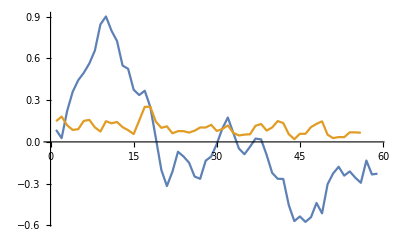

```mathematica
movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]],4]
```

```mathematica
ListLinePlot[{Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]],movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]],4]}]
```

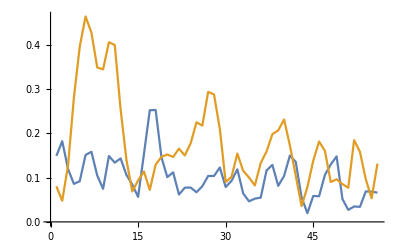

```mathematica
ListLinePlot[{movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]],4],movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[22]]][[16]]],4]}]
```

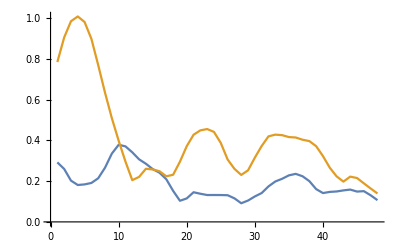

```mathematica
ListLinePlot[{movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]],12],movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[22]]][[16]]],12]}]
```

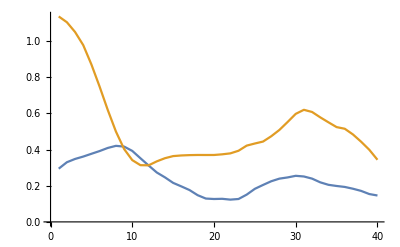

```mathematica
ListLinePlot[{movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]],20],movingSD[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[22]]][[16]]],20]}]
```

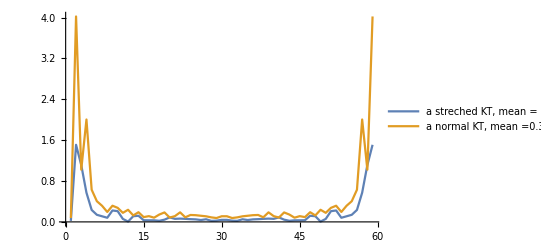

```mathematica
ListLinePlot[{Abs[Fourier[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]]]],Abs[Fourier[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[22]]][[16]]]]]},PlotRange->All,PlotLegends->{"a streched KT, mean = 0.56um","a normal KT, mean =0.39um"}]
```

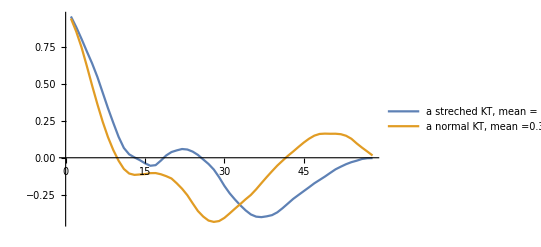

```mathematica
ListLinePlot[{Table[CorrelationFunction[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]],i],{i,Length[
Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[21]]][[16]]]
]-1}],Table[CorrelationFunction[Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[22]]][[16]]],i],{
i,
Length[
Transpose[Transpose[GatherBy[Select[exportcompleteStrechMove,Length[#]==Length[exportcompleteStrechMove[[1]]]&],#[[{1,2,3,4}]]&][[22]]][[16]]]]-1
}]},PlotRange->All,PlotLegends->{"a streched KT, mean = 0.56um","a normal KT, mean =0.39um"}]
```

```mathematica
data2[[All,3]]=Rescale[data2[[All,3]]];
```

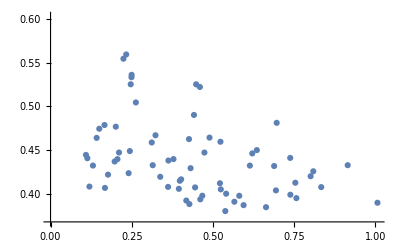

```mathematica
ListPlot[Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]]}&,widthandlocdata]]
```

```mathematica
widthandlocdata
```

{{{0.412428,0.420902,0.443646,0.457867,0.426513,0.331305,0.359767,0.359929,0.325912,0.360091,0.352997,0.381533,0.360722,0.346719,0.425867,0.411514,0.402212,0.581529,0.411301,0.457736,0.474769,0.449096,0.477842,0.46449},{-0.83079,-1.279,-1.59258,-1.9328,-1.87704,-1.21728,-0.695215,-0.362966,-0.211438,0.0950014,0.305652,0.433028,0.516935,0.844824,1.03617,1.33456,1.28874,1.12712,0.870247,0.767858,0.486329,0.262901,0.207159,0.110019}},{{0.386991,0.356171,0.375382,0.455188,0.4439,0.433457,0.444535,0.479825,0.473709,0.440718,0.419948,0.445654,0.389868,0.394856,0.415773,0.422013,0.42494,0.381571,0.475555,0.422909,0.381913,0.426446,0.44671,0.43497},{-0.864892,-0.775425,-0.870996,-0.951716,-0.910509,-0.909692,-0.748459,-0.646103,-0.544546,-0.417999,-0.208173,0.0287613,0.201633,0.42992,0.51579,0.692001,0.676461,0.620665,0.664194,0.743926,0.656735,0.566631,0.672793,0.700847}},{{0.360377,0.394534,0.425847,0.466598,0.444883,0.431627,0.40013,0.399323,0.402629,0.39516,0.399492,0.420331,0.396206,0.401046,0.408392,0.385392,0.422083,0.425598,0.397448,0.377429,0.518288,0.497621,0.455624,0.507051},{-1.24551,-1.12016,-1.00292,-0.923035,-0.788176,-0.711515,-0.502097,-0.454511,-0.473355,-0.373579,-0.199688,-0.0458802,-0.00589806,0.19208,0.283303,0.473986,0.533041,0.623759,0.76745,1.04345,0.85945,0.76745,0.76745,0.76745}},{{0.380717,0.374864,0.428686,0.419409,0.388374,0.40945,0.408621,0.406122,0.393544,0.447811,0.400207,0.435203,0.416524,0.432722,0.415464,0.41169,0.390007,0.415656,0.383613,0.435892,0.428782,0.432461,0.436456,0.47218},{-1.33657,-1.02787,-0.677517,-0.365717,-0.0118333,0.279744,0.611602,0.175413,-0.227031,-0.296674,-0.247798,-0.209151,-0.254666,-0.0333417,-0.0280765,0.161045,0.161118,0.194187,0.279666,0.473117,0.437993,0.349619,0.470783,0.469683}},{{0.400822,0.391449,0.392586,0.423822,0.404132,0.394037,0.387286,0.382427,0.381293,0.372123,0.440988,0.430066,0.43369,0.442416,0.421846,0.412472,0.413587,0.400186,0.395795,0.456356,0.424316,0.400414,0.382414,0.421337},{-0.144059,-0.0996781,-0.0119577,0.0523671,0.182602,0.109636,0.233683,0.156449,0.0551242,0.00663868,-0.0116774,-0.0223911,-0.0453576,-0.125781,-0.0986965,0.10202,0.0421924,-0.194316,-0.137161,0.0753575,0.00677149,-0.0692173,0.114458,-0.0172084}},{{0.42196,0.403082,0.426208,0.453209,0.402599,0.460354,0.427221,0.424931,0.433684,0.424694,0.445741,0.44662,0.427147,0.417078,0.411114,0.475188,0.416625,0.420357,0.428586,0.421481,0.4397,0.447466,0.449346,0.457408},{-0.278586,-0.162478,-0.0284944,0.0159234,0.0823537,0.0204606,0.0543684,-0.0451212,-0.0137736,-0.00714394,0.0479246,0.0612271,-0.0411403,-0.186764,-0.222922,0.0679972,0.0517802,0.089565,0.104225,0.17217,0.13365,0.058076,0.112102,0.0352384}},{{0.440552,0.460428,0.474558,0.433268,0.429017,0.443606,0.462944,0.39966,0.477908,0.511244,0.478027,0.48779,0.477131,0.451111,0.423716,0.40321,0.424388,0.439105,0.450683,0.410356,0.438232,0.41339,0.417866,0.42499},{0.490567,0.369719,0.313192,0.192562,0.181616,0.0756862,0.17434,0.136993,-0.0777067,-0.0938571,-0.110065,-0.160233,-0.195418,-0.236644,-0.191789,-0.00669276,-0.1001,-0.314572,-0.224183,-0.0270337,-0.129258,-0.189208,0.040515,0.038549}},{{0.475046,0.408236,0.416352,0.42505,0.463314,0.445753,0.438322,0.47908,0.423148,0.509685,0.458015,0.463508,0.460002,0.432091,0.406528,0.432903,0.427436,0.442312,0.455924,0.482123,0.442408,0.40025,0.419112,0.376341},{0.353692,0.276574,0.317566,0.331799,0.309542,0.171084,0.228441,0.110137,0.0758167,0.045032,0.0552887,-0.0300704,-0.185767,-0.240694,-0.240549,-0.0712784,-0.141829,-0.317636,-0.31081,-0.132517,-0.218166,-0.268654,-0.0201258,-0.0293541}},{{0.565925,0.618897,0.615353,0.52815,0.524672,0.567414,0.521434,0.580661,0.600784,0.629869,0.641534,0.644533,0.640457,0.556722,0.514356,0.480909,0.481265,0.496783,0.488333,0.477561,0.557738,0.52001,0.499861},{-1.25503,-1.12312,-0.908256,-0.93494,-0.799763,-0.733482,-0.530858,-0.523784,-0.417388,-0.194195,0.0843223,0.176322,0.176322,0.268322,0.360322,0.360322,0.360322,0.452322,0.636322,0.62935,0.620352,0.844491,1.01054}},{{0.390501,0.391213,0.381271,0.423858,0.423874,0.420036,0.463774,0.420776,0.407407,0.40781,0.386897,0.404055,0.390645,0.402474,0.374649,0.41898,0.446911,0.415523,0.381527,0.400117,0.388514,0.405632,0.412506,0.41112},{-1.06403,-1.02505,-0.981268,-0.8745,-0.771047,-0.730953,-0.640339,-0.522216,-0.535336,-0.465507,-0.313833,-0.146862,-0.0380799,0.14592,0.14592,0.32992,0.42192,0.567733,0.676184,0.988611,0.790299,0.745382,1.02746,1.0644}},{{0.404778,0.401262,0.454677,0.560192,0.406454,0.396462,0.418097,0.369397,0.359844,0.324597,0.359136,0.356794,0.350634,0.362926,0.3445,0.369827,0.33899,0.37353,0.35847,0.417016,0.367511,0.378464,0.383396,0.378,0.380097,0.357155,0.386766,0.35677,0.433111,0.395938,0.391239,0.377007,0.385662,0.407666,0.45279,0.368742,0.364534,0.359937,0.353549,0.378485,0.383591,0.378776,0.392367,0.398031,0.398408,0.378107,0.386574,0.38206,0.434688,0.404013,0.400851,0.405195,0.362098,0.379955,0.38678,0.380486,0.411014,0.384591,0.423901},{-1.02813,-1.38597,-1.62372,-1.52714,-0.979955,-0.495341,-0.0452401,0.284133,0.454815,0.578407,0.803476,1.05714,1.19472,1.26612,1.33032,1.40192,1.43507,1.49948,1.41775,1.1691,0.824079,0.486065,0.327196,0.151519,0.0335531,-0.0972056,0.0194007,0.0571515,0.0413034,0.162125,0.0614005,-0.209312,-0.339712,-0.534259,-0.546459,-0.277798,0.0211846,0.0416924,-0.0376811,-0.310092,-0.558411,-0.39849,-0.158894,-0.326154,-0.525836,-0.722454,-0.76179,-0.431862,-0.237838,-0.0224262,-0.214441,-0.338461,-0.437933,-0.430211,-0.424705,-0.222539,-0.081951,-0.0613028,-0.0966565}},{{0.343257,0.393775,0.401538,0.387011,0.370382,0.347184,0.362641,0.404855,0.343159,0.348558,0.380651,0.410404,0.369653,0.376991,0.336641,0.346701,0.33699,0.382753,0.446148,0.387516,0.368467,0.391242,0.359553,0.374961,0.354783,0.374683,0.360473,0.353083,0.347522,0.408367,0.359865,0.360044,0.349506,0.359249,0.329951,0.372576,0.359106,0.374281,0.400757,0.695838,0.443893,0.610967,0.592645,0.696948,0.438469,0.403234,0.718741,0.465775,0.453023,0.406349,0.365764,0.379604,0.443086,0.35745,0.384701,0.428523,0.431651,0.402944,0.40158},{-1.1233,-1.25363,-1.28148,-1.1737,-1.07579,-0.967023,-0.756441,-0.664548,-0.588276,-0.236049,0.0805854,0.379525,0.652349,0.915703,1.13123,1.29386,1.22747,0.924675,0.622292,0.381434,0.307332,0.298315,0.344017,0.330576,0.150694,-0.0310115,-0.0790527,-0.10088,-0.125158,-0.0321804,-0.0720493,-0.132381,-0.177912,-0.299669,-0.279497,-0.235365,-0.123479,-0.16293,-0.218054,-0.151964,-0.0259741,0.156581,0.296577,0.316327,0.32894,0.222178,0.242553,0.223971,0.124112,0.120826,-0.0154646,0.0591708,0.0698398,0.225166,0.198385,0.0845316,0.0116449,-0.101439,-0.172729}},{{0.467231,0.475256,0.464893,0.5095,0.492917,0.491737,0.529503,0.53093,0.566716,0.51373,0.489864,0.471977,0.50822,0.515416,0.408527,0.497837,0.494311,0.470152,0.478235,0.464411,0.427382,0.419911,0.469125,0.445615,0.426063,0.397453,0.415346,0.428937,0.423934,0.39489,0.418039,0.400612,0.441839,0.433349,0.388226,0.389645,0.425122,0.418735,0.377667,0.359336,0.368955,0.402407,0.375146,0.391014,0.402246,0.459613,0.416599,0.431557,0.433249,0.482567,0.399934,0.459218,0.486627,0.476114,0.451697,0.502127,0.438456,0.519309,0.457959},{0.577395,0.393395,0.577395,0.669395,0.617294,0.686622,0.733656,0.823938,0.911482,0.982254,0.781557,0.689949,0.536689,0.374721,0.228779,0.282687,0.376943,0.329051,0.163876,-0.121024,-0.273705,-0.223464,-0.177238,-0.26156,-0.30778,-0.369957,-0.309243,-0.187522,-0.213541,-0.2006,-0.266945,-0.136725,-0.14512,-0.216848,-0.177658,-0.0482344,-0.102024,-0.106987,-0.247074,-0.308701,-0.293206,-0.262846,-0.415373,-0.5762,-0.564777,-0.646661,-0.547726,-0.551908,-0.719353,-0.546215,-0.367766,-0.241809,-0.22317,-0.123178,-0.126546,-0.0395873,-0.0187274,-0.117207,-0.0268492}},{{0.347003,0.361316,0.347476,0.342866,0.357385,0.376527,0.358862,0.395103,0.362966,0.376255,0.363145,0.365559,0.357458,0.379321,0.657978,0.375004,0.437618,0.401431,0.367338,0.368623,0.384338,0.446407,0.449327,0.426716,0.496653,0.457655,0.429572,0.428691,0.434505,0.449887,0.422748,0.483557,0.41476,0.436776,0.432858,0.408394,0.432543,0.38904,0.4205,0.503844,0.403832,0.419402,0.396097,0.400588,0.465955,0.449438,0.437716,0.435269,0.409365,0.411469,0.382989,0.394389,0.419919,0.441778,0.591664,0.523853,0.437472,0.447087,0.447925},{-0.085006,-0.179304,-0.0873042,0.241845,0.483203,0.76196,1.00372,1.15077,1.14727,1.08926,0.928701,0.841033,0.689509,0.650211,0.389635,0.375773,0.48104,0.43571,0.321555,0.133407,0.00746331,0.0863783,0.16084,0.0693796,-0.0762056,-0.201197,-0.195148,-0.0779428,-0.166817,-0.179402,-0.195656,-0.0421603,-0.151224,-0.257142,-0.340277,-0.291841,-0.27613,-0.371989,-0.378355,-0.434447,-0.424164,-0.404811,-0.557786,-0.626394,-0.56791,-0.615347,-0.597015,-0.617757,-0.69564,-0.465779,-0.325717,-0.133562,-0.0626073,-0.164054,-0.313447,-0.207479,-0.0362997,-0.235733,-0.198236}},{{0.40037,0.436029,0.402967,0.403715,0.400227,0.370906,0.379975,0.379754,0.376656,0.402255,0.392262,0.418359,0.4045,0.38567,0.398224,0.394956,0.383767,0.381763,0.403729,0.439053,0.437345,0.397401,0.382694,0.41602,0.416056,0.467902,0.386367,0.431002,0.406193,0.401958,0.381162,0.383859,0.376712,0.371045,0.331176,0.43024,0.399894,0.425239,0.394575,0.381359,0.401499,0.364251,0.380092,0.396711,0.400893,0.397462,0.393924,0.397083,0.388367,0.396316,0.404148,0.397444,0.411853,0.409061,0.395701,0.40973,0.411956,0.403749,0.357654},{-1.74219,-1.89136,-1.92809,-1.35636,-1.01811,-0.760093,-0.507581,-0.344292,-0.250522,-0.106467,0.0706604,0.251951,0.30531,0.400177,0.518142,0.465708,0.443846,0.145216,-0.247963,-0.61499,-0.688775,-0.664443,-0.389739,-0.0273269,0.162731,0.299674,0.606202,0.86316,0.991467,1.13665,1.14472,1.1698,1.05523,0.693511,0.36349,0.0331729,-0.126678,-0.232084,-0.346783,-0.284297,-0.0832002,0.0529704,0.173089,0.0331494,-0.0065498,0.0658224,0.205995,0.366108,0.355728,0.441858,0.531098,0.556083,0.600511,0.514551,0.319394,0.00819272,-0.149422,-0.281606,-0.627008}},{{0.332041,0.354532,0.358159,0.364704,0.351433,0.379245,0.431714,0.401745,0.353395,0.379346,0.371262,0.386368,0.3873,0.382928,0.372058,0.363401,0.357099,0.377821,0.361863,0.352103,0.382643,0.354438,0.361488,0.363653,0.388987,0.386272,0.397135,0.379344,0.41862,0.430785,0.370395,0.414375,0.400092,0.427082,0.361022,0.37901,0.405781,0.417947,0.378612,0.381071,0.419826,0.376139,0.39417,0.432199,0.409986,0.384968,0.409335,0.368086,0.372601,0.357559,0.385208,0.37869,0.362829,0.3716,0.4116,0.429789,0.413019,0.407169,0.416895},{-1.59136,-1.64937,-1.62421,-1.53075,-1.46493,-1.28341,-0.726025,-0.106856,0.352492,0.733136,1.00471,1.11804,1.0971,0.632778,0.202199,-0.130606,-0.244936,-0.220962,-0.364255,-0.515794,-0.610573,-0.659645,-0.582102,-0.204047,0.117505,0.315258,0.76197,1.08982,1.39714,1.58071,1.47813,1.09271,0.630304,0.2144,0.0460439,-0.235977,-0.39022,-0.578865,-0.837373,-0.889731,-0.816322,-0.641335,-0.501115,-0.432029,-0.17971,0.163211,0.495126,0.72395,0.915603,1.07378,0.950526,0.92759,0.798523,0.652933,0.465385,0.0251871,-0.243861,-0.473896,-0.67399}},{{0.351533,0.36511,0.353966,0.351353,0.399998,0.39255,0.420311,0.455183,0.403077,0.428592,0.426124,0.392275,0.330877,0.390226,0.411838,0.44853,0.374206,0.410406,0.398287,0.379613,0.453208,0.467802,0.446239,0.483221,0.390313,0.386591,0.372899,0.436832,0.394768,0.368396,0.395703,0.417217,0.39518,0.453372,0.411367,0.392352,0.375729,0.394718,0.386752,0.359295,0.375191,0.389825,0.420584,0.371984,0.40802,0.376421,0.382831,0.393971,0.368962,0.412445,0.411548,0.441632,0.413319,0.391104},{1.3242,1.20779,1.29299,1.17173,0.672534,0.314763,-0.199457,-0.585382,-0.528529,-0.322941,-0.218054,-0.12686,0.0679669,0.240802,0.540456,0.594715,0.771444,1.01417,1.17381,1.11457,1.01587,0.654697,0.554349,0.355154,0.150998,0.25145,0.138712,-0.103038,-0.335983,-0.451773,-0.462274,-0.357108,-0.479183,-0.625636,-0.844548,-0.747629,-0.500514,-0.46857,-0.532872,-0.582844,-0.583404,-0.434382,-0.454918,-0.469698,-0.369852,-0.318509,-0.289331,-0.289354,-0.373007,-0.597835,-0.690095,-0.569414,-0.50902,-0.36675}},{{0.41662,0.402594,0.366431,0.35891,0.352026,0.354762,0.366625,0.36396,0.350729,0.367227,0.360943,0.400306,0.358053,0.355093,0.374112,0.388449,0.376514,0.376027,0.354496,0.348902,0.383311,0.421097,0.381094,0.551937,0.390909,0.358651,0.355671,0.384122,0.371189,0.375667,0.37819,0.345767,0.357957,0.374345,0.357492,0.357112,0.363787,0.360696,0.373049,0.712602,0.718925,0.678811,0.700843,0.712249,0.38962,0.389954,0.362605,0.385928,0.369395,0.340557,0.374508,0.428948,0.38319,0.460373,0.419814,0.453909,0.387556,0.386188,0.394098},{0.482199,0.309235,0.216017,0.245728,0.228755,0.245595,0.22354,0.210147,0.073564,0.0384178,-0.0219107,-0.277298,-0.519281,-0.53816,-0.571929,-0.438363,-0.258324,0.0192896,0.350093,0.494167,0.769677,1.03649,1.32456,1.38915,1.10021,0.760447,0.54164,0.415903,0.257043,0.150373,-0.026542,-0.0689457,-0.209485,-0.4412,-0.499921,-0.612848,-0.565497,-0.648472,-0.729522,-0.715045,-0.576158,-0.411711,-0.252095,-0.222731,-0.145942,-0.0604392,-0.0402602,0.00464438,0.0633501,0.137677,0.0563024,0.0167839,0.00274251,-0.0563689,-0.25113,-0.430804,-0.416406,-0.477466,-0.454413}},{{0.376255,0.370015,0.379844,0.415628,0.382232,0.395054,0.393067,0.381005,0.417727,0.38946,0.410872,0.420959,0.39698,0.388899,0.415552,0.396487,0.383867,0.408187,0.423257,0.438507,0.432128,0.423985,0.380505,0.3701,0.445372,0.417516,0.404205,0.425961,0.444443,0.460524,0.509012,0.4921,0.484765,0.550545,0.533464,0.489719,0.431461,0.474302,0.410324,0.398556,0.450103,0.49058,0.482022,0.434948,0.492784,0.466915,0.438812,0.474194,0.517625,0.536525,0.48902,0.483781,0.485502,0.506612,0.48512,0.464292,0.444719,0.427969,0.420318},{-0.0838502,-0.160629,-0.0181496,0.224161,0.324061,0.439724,0.534272,0.642934,0.752463,0.803374,0.729364,0.743982,0.657167,0.627252,0.395813,0.446472,0.502466,0.48195,0.404688,0.232706,0.0718628,0.0805852,0.114161,0.0192951,-0.12022,-0.134676,-0.103954,0.0734632,0.144143,0.0899327,0.0499404,0.105281,-0.0161809,-0.153289,-0.120274,-0.114935,-0.101803,-0.140325,-0.229385,-0.244947,-0.260298,-0.263134,-0.437981,-0.477828,-0.4314,-0.417525,-0.450266,-0.392745,-0.48265,-0.359956,-0.25749,-0.214954,-0.225874,-0.297082,-0.467947,-0.435972,-0.416763,-0.57314,-0.543381}},{{0.692847,0.68679,0.727618,0.583817,0.692664,0.745102,0.663464,0.749553,0.611904,0.542805,0.563126,0.45557,0.495234,0.503628,0.44763,0.468107,0.428609,0.520667,0.480394,0.670187,0.612294,0.528349,0.62246,0.644326,0.55223,0.512236,0.566353,0.489135,0.48793,0.542293,0.491876,0.492709,0.514728,0.510477,0.589808,0.624842,0.538496,0.676903,0.560291,0.496162,0.435855,0.483337,0.569369,0.464681,0.506377,0.564166,0.547413,0.506994,0.496086,0.465769,0.486503,0.587805,0.562002,0.542967,0.562483,0.611079,0.578941,0.626814,0.61907},{0.0864845,0.02693,0.222826,0.360367,0.443369,0.496427,0.563316,0.656024,0.843798,0.901185,0.79883,0.724559,0.548569,0.525032,0.375109,0.336575,0.367513,0.251945,0.028352,-0.201733,-0.317089,-0.213721,-0.0708233,-0.104789,-0.149361,-0.248647,-0.265212,-0.134897,-0.104541,-0.0148151,0.0954722,0.175034,0.0628293,-0.0480163,-0.0885023,-0.0345932,0.0236377,0.0180293,-0.0937914,-0.222744,-0.264967,-0.26645,-0.454531,-0.56903,-0.535581,-0.574676,-0.541239,-0.438779,-0.513167,-0.303991,-0.226365,-0.178597,-0.242413,-0.212005,-0.257017,-0.293697,-0.134033,-0.233585,-0.228411}},{{0.37517,0.406327,0.400693,0.364753,0.367324,0.350772,0.41313,0.378199,0.36673,0.400958,0.391863,0.407016,0.398192,0.352884,0.343803,0.37528,0.370591,0.364386,0.363193,0.382087,0.378261,0.395064,0.391331,0.394686,0.430811,0.353993,0.362821,0.357426,0.392293,0.369638,0.354124,0.487782,0.400963,0.358017,0.393719,0.387875,0.414611,0.406165,0.415999,0.381616,0.371686,0.40182,0.422442,0.361864,0.399642,0.385938,0.364001,0.407483,0.367429,0.401585,0.402688,0.444318,0.431285,0.503773,0.386363,0.366275,0.368823,0.366388,0.374366},{1.77586,1.89106,1.88404,1.97139,1.86238,1.6695,1.33204,0.964039,0.596039,0.357254,0.153359,-0.216614,-0.558496,-0.754006,-0.756189,-0.898804,-0.824534,-0.680409,-0.664145,-0.714977,-0.432154,-0.443786,-0.374837,-0.13032,-0.124603,-0.397895,-0.463674,-0.668524,-0.878409,-1.1492,-1.31819,-1.32647,-1.1902,-1.11769,-0.95635,-0.966191,-0.87843,-0.788941,-0.655334,-0.514898,-0.326443,-0.186151,0.0327465,0.0181018,0.0157042,0.0923172,0.182194,0.336941,0.505,0.522584,0.388496,0.321139,0.378347,0.504675,0.736595,0.649232,0.611099,0.648093,0.375761}},{{0.41107,0.476859,0.49673,0.414186,0.425345,0.416773,0.426195,0.381564,0.343819,0.349593,0.371479,0.337251,0.351719,0.356698,0.331147,0.329303,0.359893,0.342747,0.357935,0.38152,0.380691,0.354314,0.378165,0.374127,0.336634,0.387414,0.370183,0.368053,0.454089,0.445562,0.508067,0.487767,0.440956,0.412484,0.394581,0.397515,0.395322,0.39821,0.389919,0.414666,0.439977,0.442858,0.442278,0.424101,0.384772,0.393081,0.377968,0.366046,0.387474,0.361097,0.379693,0.371542,0.387828,0.385457,0.402512,0.406755,0.357564,0.386085,0.4017},{2.17073,2.3473,2.28679,1.7522,1.46505,1.35829,1.26629,1.08229,0.714285,0.530285,0.254285,-0.205715,-0.573715,-0.849715,-0.941509,-1.08859,-1.0863,-1.01943,-0.971286,-0.927661,-0.638385,-0.403851,-0.254824,0.110314,0.159565,0.000744295,-0.229242,-0.509043,-0.694215,-0.852024,-1.00091,-1.10359,-1.14477,-1.18314,-1.00901,-1.07646,-0.899203,-0.623684,-0.622797,-0.469046,-0.342107,-0.270846,0.0638204,0.0651928,0.0405563,0.107642,0.160894,0.228298,0.315703,0.39244,0.312376,0.22648,0.225284,0.336172,0.602183,0.471475,0.419808,0.460549,0.348858}},{{0.423521,0.432169,0.452996,0.46543,0.455912,0.527315,0.525972,0.353329,0.434819,0.462447,0.526697,0.465294,0.567859,0.517963,0.466408,0.600375,0.582139,0.501139,0.48605,0.50291,0.542969,0.508517,0.437496,0.558187,0.603902,0.569446,0.488719,0.485911,0.4813,0.505838,0.493018,0.563709,0.412221,0.42563,0.501698,0.556982,0.580303,0.498488,0.540766,0.49976,0.580492,0.586305,0.694417,0.81672,0.70221,0.635341,0.685094,0.701427,0.484634,0.58843,0.598305,0.513579,0.605768,0.614602,0.620033,0.610309,0.582243,0.49847,0.506256},{1.479,1.46926,1.29256,1.34828,1.39483,1.48073,1.57648,1.47075,1.22426,1.15965,0.895424,0.975832,1.03386,1.07863,1.30588,1.21591,1.04039,0.934804,0.860324,0.750639,0.689605,0.625174,0.379666,0.159842,0.138727,0.0320488,0.039027,0.0888896,-0.022789,-0.227584,-0.140673,-0.107124,-0.156447,-0.195631,-0.206748,-0.449735,-0.384539,-0.48014,-0.444527,-0.630576,-0.686065,-0.593539,-0.583211,-0.736816,-0.944014,-0.822014,-0.920241,-0.942188,-0.746977,-0.652911,-0.740721,-0.915604,-1.03435,-1.12784,-1.38636,-1.56489,-1.80603,-1.9987,-2.2031}},{{0.445261,0.399046,0.472075,0.541323,0.499768,0.437488,0.458811,0.412157,0.480447,0.520624,0.506888,0.466643,0.483654,0.4453,0.408243,0.434303,0.450417,0.430978,0.411627,0.501908,0.45659,0.411109,0.435377,0.442773,0.4595,0.42978,0.449974,0.449103,0.46102,0.481677,0.457597,0.489088,0.485127,0.426237,0.463253,0.465278,0.500971,0.445952,0.484504,0.433841,0.413378,0.458897,0.452774,0.494266,0.441571,0.467544,0.465398,0.47267,0.52668,0.450892,0.434919,0.453501,0.466583,0.517475,0.472235,0.449723,0.458459,0.432088},{2.18093,2.29034,2.32308,2.35472,2.24699,2.04521,1.61539,1.17355,0.780301,0.779933,1.19175,1.46242,1.45642,1.4399,1.28468,1.3316,1.25802,1.29719,1.07413,1.02227,0.831739,0.577438,0.341907,0.287403,0.209657,0.188276,0.0874917,-0.0604399,-0.208483,-0.106354,-0.105816,-0.273003,-0.200717,-0.205822,-0.601239,-0.695517,-0.769642,-0.754159,-0.899372,-0.955559,-0.963833,-1.02446,-1.07491,-1.04821,-1.02439,-1.07384,-1.19878,-1.2156,-1.1671,-1.30752,-1.62951,-1.66475,-1.61419,-1.72907,-1.76439,-1.71841,-1.89423,-2.0632}},{{0.406131,0.444984,0.411203,0.514623,0.605317,0.610816,0.422159,0.457008,0.421233,0.431278,0.423563,0.430139,0.506805,0.60382,0.450816,0.444818,0.427589,0.521502,0.475288,0.470155,0.448193,0.458465,0.551675,0.52622,0.457857,0.420418,0.409033,0.552387,0.492849,0.460924,0.392681,0.401853,0.4109,0.408137,0.421904,0.489519,0.403747,0.434209,0.40114,0.392213,0.443281,0.425809,0.439281,0.417936,0.414611,0.395087,0.404706,0.400753,0.464845,0.448578,0.472171,0.41559,0.454961,0.461211,0.393883,0.418072,0.479343,0.425131,0.374849},{0.331099,0.38579,0.610047,1.10831,1.27332,1.36275,0.795229,0.219758,-0.133265,-0.286295,-0.518817,-0.529589,-0.314317,-0.209022,-0.176764,-0.0613438,0.0436353,0.212374,0.435203,0.547144,0.247098,0.0499924,-0.0612666,-0.0936093,0.11331,0.209961,0.575957,0.596987,0.293541,0.0262136,-0.0383006,-0.0873522,-0.139221,-0.127602,-0.116371,-0.190087,-0.165112,-0.0522575,0.0331471,0.0359406,-0.166748,-0.146056,-0.045573,0.179981,0.246669,0.236997,0.209661,0.0461534,-0.0129463,0.0948874,-0.192016,-0.344598,-0.484856,-0.491551,-0.66178,-0.702936,-0.73342,-0.883742,-1.05961}},{{0.415241,0.426131,0.510803,0.462581,0.538379,0.466199,0.381335,0.415715,0.503576,0.463179,0.465268,0.462295,0.424357,0.420138,0.426455,0.383926,0.426403,0.388245,0.420578,0.425307,0.408726,0.412563,0.392327,0.434311,0.45467,0.457068,0.451865,0.438069,0.465472,0.481173,0.479344,0.471041,0.445169,0.439538,0.490059,0.46223,0.473069,0.480366,0.432753,0.511107,0.464113,0.464611,0.459642,0.435796,0.434325,0.408129,0.437047,0.46683,0.47951,0.497611,0.461664,0.417745,0.442444,0.428353,0.435164,0.403048,0.439012,0.418698,0.49764},{0.910302,0.896095,0.903078,1.00378,0.915127,1.27319,1.31591,1.10196,0.752698,0.314443,-0.0605032,-0.177466,-0.241827,-0.165788,-0.185681,-0.0340552,0.0114686,0.142055,0.17267,0.265777,0.0664903,-0.0108529,-0.144644,-0.120176,0.0131112,-0.0488042,0.200938,0.319558,0.309231,0.19751,0.16244,0.133336,-0.0919403,-0.0866174,0.0337199,-0.0184217,-0.00446402,0.0889725,0.078266,-0.0129101,-0.150817,-0.100833,-0.0774011,0.0323062,-0.0634737,-0.136177,-0.0168208,-0.174115,-0.397654,-0.432637,-0.428138,-0.539994,-0.733395,-0.823779,-0.928762,-1.05258,-1.07846,-1.00744,-1.01393}},{{0.398243,0.38309,0.398667,0.366136,0.368049,0.34883,0.437398,0.397915,0.413806,0.38821,0.386557,0.353081,0.370075,0.373787,0.357699,0.390538,0.384625,0.343358,0.394092,0.368105,0.391019,0.410983,0.476617,0.425891,0.392363,0.423059,0.373598,0.402582,0.393528,0.458748,0.412189,0.439522,0.39331,0.395018,0.428786,0.423153,0.398131,0.385474,0.401722,0.373667,0.381218,0.404487,0.419828,0.409177,0.407942,0.387628,0.375863,0.389104,0.385591,0.414776,0.40305,0.414164,0.454385,0.502562,0.465078,0.509002,0.516332,0.40594,0.381636},{2.51912,2.17218,1.80588,1.62464,2.11477,2.71727,3.06312,3.05833,2.57789,1.99531,1.39757,1.1532,1.00513,0.836484,0.645896,0.39545,0.142937,0.244704,0.650703,1.01306,1.24535,1.14955,0.87871,0.671637,0.524199,0.232707,0.236931,0.108684,0.0438763,0.0543979,0.0803341,-0.00859381,-0.157363,-0.258409,-0.402186,-0.504523,-0.58035,-0.65126,-0.804437,-1.047,-1.33206,-1.3922,-1.432,-1.40774,-1.58092,-1.61862,-1.58877,-1.70697,-1.63834,-1.52848,-1.60638,-1.82416,-1.84229,-1.70351,-1.68934,-1.62124,-1.56128,-1.58977,-1.60461}},{{0.544301,0.427748,0.578306,0.585144,0.512087,0.611656,0.647431,0.514845,0.511614,0.500292,0.605609,0.500732,0.422254,0.464401,0.48046,0.46585,0.459613,0.424591,0.466216,0.439226,0.411952,0.38761,0.419364,0.417081,0.394867,0.379661,0.383911,0.397439,0.393475,0.396934,0.472225,0.439912,0.40207,0.399267,0.390073,0.435919,0.455752,0.460838,0.387752,0.456754,0.494578,0.408031,0.430464,0.458999,0.425486,0.422324,0.415942,0.447896,0.4252,0.420414,0.389561,0.409389,0.392121,0.378525,0.397146,0.385755,0.396524,0.385651,0.410204},{3.22711,3.0043,2.19077,1.90927,1.91513,2.29474,2.50379,2.44695,2.31528,1.944,1.61681,1.71167,1.54971,1.18625,1.34009,0.840775,0.839548,0.864082,0.844335,0.748722,0.696729,0.631866,0.533411,0.31572,0.457237,0.392667,0.506486,0.472463,0.476648,0.203575,-0.0606062,-0.0599189,0.043646,-0.0606988,-0.32207,-0.673586,-0.678239,-0.735702,-0.841564,-1.25631,-1.59736,-1.64888,-1.40379,-1.24956,-1.43419,-1.43956,-1.40342,-1.60847,-1.80445,-1.76493,-1.8095,-1.91783,-2.01949,-1.95162,-2.19185,-2.13941,-2.00419,-1.91909,-2.07192}},{{0.444379,0.443494,0.476494,0.538883,0.537195,0.492665,0.431209,0.475685,0.515177,0.45869,0.432172,0.463718,0.507266,0.436825,0.549857,0.538423,0.555271,0.52565,0.515769,0.515667,0.490112,0.445346,0.457743,0.423577,0.445647,0.414736,0.507855,0.486303,0.472713,0.465581,0.447379,0.492824,0.494791,0.498142,0.479799,0.477993,0.498401,0.494173,0.479764,0.491881,0.461329,0.504126,0.432719,0.424491,0.462676,0.443608,0.477711,0.462237,0.478765,0.460406,0.438127,0.438789,0.472635},{1.17259,1.13463,1.07899,1.04752,1.08651,1.05792,1.07921,0.961224,0.942645,0.911003,0.770655,0.769535,0.837826,0.696111,0.710168,0.772013,0.625989,0.438178,0.382983,0.179085,0.157939,0.0839093,-0.0026583,-0.0400087,0.066779,0.0563853,0.0875848,0.0968231,-0.0644923,-0.120842,0.0631585,0.0631585,-0.120842,-0.120842,-0.212842,-0.304842,-0.396842,-0.488842,-0.396842,-0.488842,-0.764842,-0.856842,-0.856842,-1.04084,-1.13284,-0.948842,-0.948842,-0.948842,-1.04084,-1.04084,-1.13284,-1.31684,-1.22484}},{{0.549371,0.619566,0.559562,0.470378,0.494211,0.494637,0.565801,0.48074,0.533052,0.394162,0.468401,0.574962,0.512366,0.563665,0.430032,0.467789,0.407926,0.41119,0.499336,0.582411,0.490474,0.486066,0.428853,0.382476,0.434522,0.372202,0.411804,0.400662,0.443039,0.427232,0.401486,0.379401,0.423052,0.425165,0.466919,0.399332,0.396311,0.432013,0.485198,0.45187,0.42694,0.409332,0.456141,0.403258,0.416523,0.404807,0.4459,0.504851,0.480442,0.4956,0.470738,0.515853,0.489701,0.451825},{1.89981,1.81967,1.58107,1.32707,1.12294,0.754962,0.717647,0.852353,0.903345,0.859304,0.682469,0.946248,1.03426,0.986364,0.966672,0.847889,0.834983,0.539584,0.228468,-0.15957,0.0628319,0.15453,-0.0892982,-0.0687209,-0.0753832,-0.167383,0.0166168,0.108617,-0.0753832,-0.0753832,0.0166168,0.0166168,-0.351383,-0.443383,-0.351383,-0.535383,-0.535383,-0.535383,-0.627383,-0.903383,-0.995383,-0.995383,-0.903383,-0.995383,-1.08738,-1.17938,-1.08738,-1.17938,-0.995383,-0.811383,-0.811383,-0.811383,-0.811383,-0.811383}},{{0.39941,0.415251,0.430745,0.411772,0.404636,0.449908,0.424383,0.436234,0.380143,0.420711,0.49688,0.529211,0.473956,0.49127,0.451296,0.479573,0.450033,0.407252,0.407238,0.388969,0.396362,0.409222,0.430576,0.451605,0.416822,0.446929,0.515354,0.405388,0.429678,0.37512,0.363888,0.420033,0.384164,0.396257,0.413464,0.380124,0.342339,0.381753,0.370819,0.408246,0.369042,0.368572,0.368517,0.354478,0.362006,0.41374,0.384167,0.381743,0.351046,0.388981,0.365587,0.375031,0.395248,0.427169,0.418175,0.428979,0.499,0.435204,0.390974},{3.5266,3.59432,3.16795,2.35076,1.76862,1.63379,1.50975,1.41904,1.4844,1.79669,1.84627,2.10156,1.72202,1.29407,1.01058,0.789844,0.425796,0.128787,0.0904921,0.558674,0.987016,1.048,1.20785,0.830832,0.417003,0.0517359,-0.144251,-0.363785,-0.646509,-0.739434,-0.599691,-0.111835,0.298304,0.707537,0.395605,-0.194617,-0.425797,-0.745314,-0.991946,-1.34535,-1.64206,-1.76078,-1.66656,-1.33025,-1.0368,-0.809595,-0.644864,-1.10623,-1.39346,-1.36804,-1.40713,-1.62991,-1.94233,-1.87916,-2.04613,-2.03621,-2.01675,-2.15923,-1.94461}},{{0.408989,0.444989,0.549624,0.400966,0.436007,0.407375,0.525205,0.504331,0.467716,0.489735,0.520536,0.471407,0.545768,0.441022,0.490996,0.459025,0.418493,0.52474,0.500028,0.53553,0.575903,0.606901,0.731241,0.598468,0.565015,0.45808,0.525327,0.509888,0.594083,0.566708,0.470568,0.490823,0.531014,0.519605,0.455691,0.395739,0.44423,0.455606,0.454468,0.499774,0.529986,0.501631,0.451854,0.486097,0.477662,0.52521,0.50123,0.519402,0.456333,0.452078,0.403319,0.431205,0.421283,0.398892,0.459377,0.467262,0.510998,0.487343,0.456543},{3.44677,3.12993,2.7396,2.66647,2.14024,2.27112,2.2477,2.01239,1.79091,1.7103,1.58995,1.75012,1.81486,1.75839,1.47617,1.23577,1.04288,0.777339,0.856578,0.695693,0.850234,0.719545,0.517707,0.427292,0.374188,-0.0562699,-0.555988,-0.634205,-0.560924,-0.605027,-0.418996,-0.37578,-0.353217,-0.160837,-0.0918599,-0.127071,-0.11247,-0.277135,-0.3473,-0.701596,-1.16933,-1.34935,-1.52125,-1.66115,-1.61444,-1.46178,-1.28846,-1.34284,-1.47026,-1.52103,-1.69079,-1.93104,-2.0925,-2.04946,-2.26474,-2.18771,-2.15626,-2.00876,-1.97004}},{{0.553598,0.611765,0.588315,0.620641,0.612462,0.5703,0.669885,0.590051,0.652451,0.724438,0.665479,0.630473,0.563418,0.598941,0.628567,0.57472,0.559512,0.607916,0.606506,0.593111,0.57993,0.610352,0.549302,0.523165,0.501952,0.530484,0.44159,0.491485,0.57046,0.495633,0.499567,0.540154,0.50732,0.584761,0.853924,0.881376,0.942203,0.96627,0.556136,0.963535,0.858932,0.607609,0.735539,0.905936,0.684483,0.702362,0.815376,0.874559,0.828017,0.804263,0.878864,0.858667,0.907198,0.880096,0.94705,0.831477,0.544604,1.08055,1.03345},{1.11252,0.993939,1.08219,1.0822,0.935209,0.955194,0.842799,0.965242,0.909583,0.998509,1.00466,1.1028,0.98169,1.0316,0.969528,1.01038,0.961534,0.948922,0.955502,0.96794,0.915072,0.869516,0.804002,0.67117,0.577153,0.390474,0.435289,0.413283,0.142592,0.143094,0.0441058,-0.0589423,-0.125448,-0.14136,-0.152575,-0.190358,-0.176744,-0.342307,-0.492946,-0.704429,-0.771095,-0.817552,-1.01148,-1.08585,-1.12637,-0.995543,-1.08246,-1.26496,-1.28895,-1.36359,-1.43767,-1.42474,-1.40114,-1.325,-1.22825,-1.05995,-0.974002,-1.06651,-0.985722}},{{0.439668,0.440101,0.424904,0.475898,0.462042,0.472775,0.482628,0.48481,0.477665,0.459361,0.470147,0.633231,0.475498,0.480273,0.429438,0.493214,0.462954,0.453963,0.489464,0.463887,0.486012,0.474738,0.45176,0.483529,0.487959,0.510102,0.517864,0.507568,0.499267,0.497761,0.443932,0.446149,0.479405,0.485938,0.481631,0.44779,0.480984,0.487145,0.485992,0.455363,0.496552,0.462142,0.461594,0.496105,0.462806,0.483653,0.481268,0.507349,0.458792,0.494427,0.466705,0.494984,0.489578,0.452786,0.439029,0.427862,0.462603,0.427095,0.452807},{0.780268,0.531557,0.51149,0.527377,0.25804,0.314794,0.24885,0.395597,0.386935,0.492817,0.460989,0.577429,0.520808,0.631966,0.557605,0.672491,0.566173,0.588938,0.593358,0.550501,0.521445,0.449748,0.44523,0.414622,0.450295,0.333622,0.396246,0.338086,0.080063,0.0895251,0.12544,0.0363931,0.0944839,0.0395615,-0.112921,-0.232382,-0.232849,-0.238774,-0.410945,-0.467658,-0.428565,-0.475606,-0.498232,-0.478409,-0.557101,-0.500933,-0.577304,-0.674557,-0.625186,-0.742649,-0.839345,-0.959801,-0.958529,-0.872701,-0.74763,-0.573915,-0.504382,-0.41153,-0.380789}},{{0.429511,0.431863,0.476485,0.446367,0.464061,0.491752,0.485583,0.453891,0.507223,0.460481,0.497425,0.408711,0.401267,0.408014,0.418071,0.411028,0.412727,0.414765,0.408424,0.425381,0.407043,0.419884,0.410383,0.431348,0.412468,0.422829,0.446455,0.449886,0.433639,0.420936,0.45192,0.449822,0.471281,0.477237,0.434643,0.401958,0.443219,0.397225,0.414398,0.417303,0.402265,0.441077,0.442298,0.385587,0.415774,0.401286,0.419013,0.421985,0.425724,0.428851,0.423449,0.423986,0.433291,0.468714,0.421634,0.457505,0.385672,0.425101,0.428423},{0.380446,0.404252,0.438199,0.47428,0.314594,0.131699,-0.144731,-0.320391,-0.566501,-0.637193,-0.749276,-0.0689884,0.323295,0.787416,1.12442,1.34363,1.43474,1.56736,1.60209,1.75518,1.66705,1.74241,1.66818,1.45588,1.08163,0.617105,0.350439,0.103592,-0.266147,-0.683461,-1.00016,-1.22669,-1.41176,-1.48651,-1.06814,-0.920996,-0.810521,-0.698538,-0.586546,-0.5519,-0.46693,-0.535445,-0.521146,-0.433853,-0.385292,-0.306492,-0.0657847,-0.0566822,0.00334543,-0.131382,-0.190178,-0.263247,-0.310777,-0.272355,-0.353586,-0.520627,-0.56363,-0.595089,-0.775292}},{{0.535871,0.505378,0.511003,0.516382,0.558497,0.63497,0.641306,0.631906,0.5854,0.659441,0.586036,0.59482,0.550112,0.498073,0.510225,0.607395,0.617345,0.546983,0.553289,0.552089,0.503505,0.521373,0.572095,0.587033,0.536143,0.548151,0.446654,0.510399,0.553459,0.592796,0.66656,0.575931,0.580766,0.619494,0.614436,0.592376,0.579866,0.536605,0.555985,0.502325,0.517061,0.510287,0.478609,0.473958,0.471615,0.506305,0.470726,0.434767,0.461724,0.435197,0.46121,0.487294,0.447932,0.448283,0.445014,0.457346,0.486709,0.451195,0.431126},{-0.071957,-0.0734162,-0.0583808,0.00165858,0.166382,0.347609,0.505872,0.686368,0.599434,0.680067,0.522943,0.765681,0.714678,0.818355,0.927699,0.994954,1.03794,1.10304,1.06041,1.12401,0.996413,1.071,0.955698,0.789125,0.604651,0.504988,0.525348,0.540524,0.358861,0.143155,-0.083639,-0.110136,-0.290048,-0.352219,-0.503517,-0.619199,-0.672109,-0.696823,-0.756235,-0.821088,-0.851551,-0.803486,-0.837386,-0.751178,-0.693057,-0.65603,-0.410913,-0.431159,-0.518756,-0.624675,-0.579764,-0.672737,-0.67355,-0.58736,-0.631994,-0.801059,-0.82614,-0.688344,-0.714917}},{{0.494795,0.545714,0.583601,0.458879,0.448264,0.429068,0.432109,0.451553,0.40454,0.400562,0.429756,0.427292,0.456502,0.47997,0.444037,0.416246,0.421697,0.411548,0.426542,0.425848,0.43412,0.419111,0.408431,0.401735,0.409454,0.393741,0.417821,0.424134,0.432513,0.481746,0.457388,0.450448,0.474599,0.452546,0.42738,0.461329,0.438506,0.420811,0.398008,0.421273,0.420929,0.421537,0.414538,0.41898,0.468396,0.523007,0.466306,0.419633,0.428655,0.43361,0.460199,0.384671,0.459292,0.437654,0.406392,0.437192,0.460775,0.447444,0.43471},{0.0132121,0.0580797,0.494797,0.826743,0.968583,1.31705,1.37463,1.49918,1.43434,1.59968,1.52627,1.57227,1.50651,1.59643,1.59791,1.73939,1.73148,1.79936,1.74109,1.84463,1.68532,1.69222,1.65307,1.61819,1.42931,1.06171,0.940513,0.762059,0.451819,0.184953,-0.110061,-0.294061,-0.478061,-0.294061,-0.110061,-0.0180611,-0.202061,-0.110061,-0.110061,-0.386061,-0.662061,-1.03006,-1.31997,-1.50693,-1.72215,-1.77435,-1.86986,-1.92469,-1.74583,-1.76606,-1.84867,-2.04206,-2.25492,-2.22606,-2.04206,-2.04206,-2.13406,-2.04206,-1.80835}},{{0.436867,0.426869,0.389457,0.490959,0.415057,0.419172,0.430758,0.440018,0.439365,0.419022,0.409415,0.378607,0.447617,0.496507,0.565229,0.579137,0.619374,0.525981,0.502315,0.444036,0.475302,0.476589,0.491418,0.62465,0.67485,0.719864,0.647977,0.670153,0.602753,0.602346,0.560396,0.652545,0.605693,0.631437,0.594454,0.544258,0.626147,0.622416,0.663457,0.5125,0.505938,0.498156,0.461938,0.438347,0.472801,0.475957,0.481636,0.552075,0.630203,0.449898,0.596461,0.558669,0.561593,0.536944,0.493632,0.504983,0.479347,0.491987},{1.37724,1.06841,0.852382,0.64075,0.619197,0.453735,0.509955,0.508241,0.676377,0.744867,0.999829,1.31212,1.74782,2.04403,2.26574,2.26523,2.00766,1.82604,1.74014,1.54797,1.51888,1.52856,1.54457,1.45318,1.34881,1.38416,1.22342,0.970312,0.600792,0.248458,0.154717,0.0297659,-0.122614,-0.288981,-0.490931,-0.603154,-0.616399,-0.736438,-0.893399,-0.933084,-1.13179,-1.24967,-1.22343,-1.34408,-1.21765,-1.0501,-1.12207,-1.36703,-1.62619,-1.81019,-1.96933,-2.24532,-2.33709,-2.26852,-2.19936,-2.13702,-2.09474,-2.02247}},{{0.446994,0.419923,0.540425,0.584649,0.516125,0.506947,0.524507,0.573795,0.526164,0.490564,0.534183,0.510544,0.52016,0.53151,0.561827,0.543169,0.503865,0.529676,0.511072,0.483114,0.509981,0.606693,0.657167,0.587048,0.524585,0.443057,0.55719,0.454113,0.428728,0.447499,0.554126,0.491548,0.495477,0.460995,0.50186,0.456883,0.469111,0.512352,0.561207,0.521817,0.516864,0.451929,0.47726,0.500414,0.538185,0.521921,0.46301,0.501462,0.442126,0.438247,0.421207,0.459685,0.475891,0.449035,0.489658,0.508856},{2.18074,2.07806,1.94793,1.89454,1.63399,1.44268,1.25075,1.19596,1.0326,1.10549,0.922674,1.00451,0.875287,0.967287,0.84127,0.787486,0.679369,0.54813,0.399736,0.382532,0.189489,0.151986,0.0168043,-0.0550406,0.120644,0.199253,0.507287,0.599287,0.691287,0.599287,0.323287,0.323287,0.323287,0.139287,-0.228713,-0.320713,-0.504713,-0.688713,-0.927176,-1.13119,-1.11503,-1.22186,-1.28926,-1.19547,-1.26881,-1.23288,-1.33008,-1.40128,-1.50855,-1.54885,-1.49311,-1.42524,-1.38261,-1.44178,-1.53323,-1.56138}},{{0.443387,0.417464,0.410323,0.410419,0.418654,0.438467,0.484941,0.402178,0.465976,0.465523,0.447067,0.450491,0.448991,0.445638,0.468788,0.523354,0.444013,0.445948,0.426998,0.426039,0.407321,0.428223,0.418818,0.441429,0.428473,0.393179,0.416514,0.42177,0.443726,0.462132,0.44413,0.439061,0.466741,0.432265,0.416959,0.413425,0.419854,0.418109,0.396518,0.429447,0.418856,0.415849,0.414706,0.404041,0.378643,0.440338,0.412814,0.486953,0.418688,0.430963,0.395083,0.387073,0.39403,0.423191,0.419314,0.399834,0.428763,0.42349},{2.95771,2.64209,2.30032,1.92821,1.58839,1.39274,1.13186,1.13512,1.14594,1.40911,1.29396,1.32562,1.18024,1.12199,0.991333,0.951108,0.832906,0.72588,0.560108,0.451926,0.31968,0.358623,0.206311,0.0923922,0.0243936,-0.0676064,-0.0676064,0.116394,0.116394,0.208394,0.300394,0.300394,0.208394,0.208394,0.116394,-0.0676064,-0.159606,-0.159606,-0.343606,-0.527606,-0.803606,-0.987606,-1.07961,-1.18266,-1.16032,-1.11335,-1.2534,-1.31766,-1.53961,-1.63701,-1.77569,-1.80066,-1.82414,-1.76931,-1.76027,-1.83152,-1.83007,-1.90086}},{{0.39174,0.41206,0.443449,0.444906,0.464925,0.448037,0.466957,0.430006,0.441016,0.391175,0.39516,0.428448,0.401916,0.393289,0.391623,0.411123,0.403871,0.402637,0.368825,0.410238,0.409545,0.459641,0.528538,0.429933,0.41353,0.422908,0.39065,0.371916,0.358316,0.390431,0.404958,0.449666,0.454624,0.480059,0.504989,0.483996,0.56962,0.570191,0.523549,0.420852,0.474859,0.456272,0.407674,0.421699,0.370751,0.384024,0.40216,0.384036,0.453318,0.413021,0.414138,0.427429,0.424209,0.447364,0.461848,0.440546,0.439256,0.478135,0.411001},{1.53107,1.89786,2.427,2.74556,2.96611,2.89192,2.31894,1.77327,1.19914,0.807726,0.520824,0.298908,-0.0604896,-0.378495,-0.529326,-0.550365,-0.650582,-0.620623,-0.280817,0.0356617,0.343462,0.669378,0.716928,0.353618,-0.17115,-0.482939,-0.76311,-0.991457,-0.958602,-0.996317,-0.80011,-0.230988,0.00972397,0.209175,0.568524,0.949259,0.940146,0.706036,0.219442,-0.159524,-0.365197,-0.671103,-0.852025,-0.869578,-1.08442,-1.04527,-1.16487,-1.26803,-1.49231,-1.40031,-1.44482,-1.43789,-1.34918,-1.13075,-0.8895,-0.69406,-0.531338,-0.364969,-0.195056}},{{0.469051,0.375653,0.407799,0.41764,0.468903,0.442319,0.375863,0.424006,0.396499,0.420648,0.419418,0.628413,0.497532,0.535764,0.483404,0.494788,0.454853,0.541671,0.512749,0.41788,0.510409,0.429273,0.49458,0.439541,0.446985,0.445789,0.473353,0.432234,0.404916,0.432511,0.442233,0.437725,0.442929,0.566154,0.578966,0.756591,0.495916,0.625811,0.543405,0.439121,0.416366,0.407502,0.414228,0.390616,0.396001,0.48822,0.510271,0.495802,0.413392,0.439256,0.409563,0.414686,0.391581,0.424413,0.455802,0.446134,0.492377,0.485389,0.471216},{0.0542047,0.0497047,0.103395,0.149847,0.222789,0.250754,0.444201,0.515556,0.397631,0.323565,0.275503,0.300115,0.213181,0.0142437,-0.0502236,0.011876,-0.0143772,-0.08288,-0.142254,-0.0820544,-0.109017,0.00125744,0.0488928,-0.0210419,-0.0534489,-0.0677706,-0.0243321,-0.00276064,0.249618,0.288086,0.134149,0.189603,-0.00586389,-0.121695,-0.0036377,0.0960588,0.117388,-0.00325532,-0.0426657,-0.105361,-0.103928,-0.181307,-0.174099,-0.128194,-0.212367,-0.0730219,-0.0366768,-0.0865904,-0.261039,-0.213375,-0.269956,-0.311125,-0.213466,-0.253056,-0.170196,-0.0873259,-0.17923,-0.173203,-0.196064}},{{0.355161,0.384447,0.389756,0.409568,0.412876,0.389849,0.406771,0.355856,0.371343,0.402151,0.372659,0.440642,0.399469,0.46647,0.460923,0.48917,0.416412,0.430173,0.408005,0.400526,0.407958,0.417787,0.416815,0.381364,0.42195,0.434752,0.467321,0.415824,0.423494,0.50739,0.466449,0.406716,0.397845,0.387704,0.424849,0.470853,0.459538,0.46013,0.461032,0.473699,0.497204,0.469701,0.432162,0.371128,0.404346,0.370035,0.378945,0.418565,0.368012,0.435352,0.358491,0.462913,0.373226,0.396682,0.395481,0.377339,0.427699,0.3958,0.394759},{0.62915,0.49217,0.456817,0.246358,0.228396,0.0426212,-0.0327344,-0.171049,-0.204298,-0.376018,-0.318626,-0.31758,-0.291407,-0.295772,-0.243877,0.0862107,0.45082,0.701005,0.827238,0.941143,1.08511,1.25475,1.22978,0.891259,0.524436,0.280449,-0.00878074,-0.0558732,-0.0802567,-0.216917,-0.449662,-0.508195,-0.576155,-0.609658,-0.358429,-0.105787,0.196727,0.367615,0.72701,1.07493,1.25707,1.21776,0.959564,0.680361,0.458997,0.250443,-0.15358,-0.254132,-0.609746,-0.886336,-0.869299,-0.931306,-0.941934,-1.12509,-1.16681,-1.22454,-1.13478,-1.16495,-1.07546}},{{0.428714,0.48271,0.449939,0.402281,0.478363,0.456947,0.374306,0.469892,0.400172,0.39708,0.412917,0.397284,0.46626,0.501535,0.41547,0.429424,0.468134,0.381276,0.373863,0.443199,0.443283,0.389245,0.38568,0.4133,0.406558,0.42039,0.432892,0.409799,0.507687,0.496966,0.436916,0.399976,0.395868,0.424269,0.42087,0.458073,0.38154,0.383037,0.383422,0.439094,0.387805,0.427799,0.453651,0.399042,0.36005,0.388496,0.392309,0.388983,0.354012,0.3865,0.359715,0.364899,0.366395,0.498922,0.469944,0.437353,0.410386,0.417076,0.47962},{1.00989,0.845294,0.706222,0.549186,0.370079,0.337835,0.367136,0.233311,0.0597049,-0.0581625,-0.0974566,-0.190172,-0.227105,-0.238087,-0.273305,-0.339815,-0.182935,-0.0828005,-0.011987,-0.0211244,0.0821687,0.137891,0.119262,0.0372313,-0.013848,-0.152517,-0.314863,-0.453416,-0.280693,-0.148211,-0.182443,-0.0421144,-0.0408642,0.1225,0.325161,0.34371,0.440224,0.453662,0.602553,0.762892,0.862122,0.958432,0.98852,0.946207,0.735613,0.402529,-0.0840132,-0.508333,-1.1441,-1.39487,-1.54272,-1.68822,-1.78742,-1.88459,-1.01315,-0.428604,0.055925,0.353659,0.713074}},{{0.604801,0.577895,0.633784,0.661461,0.97341,0.542482,0.758843,0.744822,0.619028,0.598325,0.598778,0.693605,0.900565,0.788182,0.816975,0.699018,0.596896,0.490114,0.533225,0.590194,0.705085,0.581961,0.590981,0.447391,0.447476,0.42226,0.427182,0.455475,0.432116,0.498772,0.437668,0.473256,0.516982,0.53405,0.423503,0.477636,0.445438,0.417221,0.446883,0.501725,0.425274,0.416018,0.402429,0.406219,0.390719,0.372487,0.393072,0.367869,0.361879,0.397384,0.410303,0.424652,0.428071,0.407035,0.45711,0.432305,0.456914,0.398887,0.358663},{-1.48544,-1.54989,-1.67002,-2.01935,-1.83201,-1.51267,-1.14673,-1.11085,-1.09734,-0.76473,-0.632469,-0.488617,-0.0445897,0.0481652,0.0405155,-0.143843,-0.379284,-0.460991,-0.532293,-0.490985,-0.40481,-0.39928,-0.5648,-0.723829,-0.776879,-0.708773,-0.560371,-0.270745,0.163961,0.283721,0.266861,0.465639,0.515986,0.557794,0.670816,0.725987,0.960979,0.979403,1.16622,1.36006,1.46611,1.45107,1.33859,1.00746,0.745222,0.588379,0.398996,0.232915,-0.294891,-0.387506,-0.0457075,0.253655,0.812666,1.08045,1.3278,1.24438,0.896786,0.609156,0.472528}},{{0.407972,0.39292,0.369053,0.355965,0.348938,0.432344,0.416846,0.425099,0.38908,0.454492,0.373161,0.360595,0.390494,0.379599,0.401615,0.399989,0.395385,0.374455,0.359567,0.376761,0.349246,0.350894,0.41425,0.457587,0.363794,0.367866,0.372262,0.361156,0.370452,0.369079,0.379572,0.387972,0.485735,0.402721,0.4122,0.397703,0.362209,0.386287,0.391858,0.437204,0.436246,0.408633,0.456087,0.362548,0.37965,0.400678,0.387477,0.373711,0.407951,0.373278,0.376424,0.373814,0.393688,0.417209,0.359376,0.367708,0.405913,0.390184},{-1.69866,-1.28549,-1.09133,-0.85819,-0.547367,-0.236742,-0.2116,-0.1969,-0.22015,-0.0291145,-0.000267076,-0.0209504,0.0516312,0.121718,0.116836,-0.0283261,-0.442692,-0.952787,-1.30396,-1.5403,-1.71551,-2.02595,-2.12092,-1.63246,-1.21449,-0.756717,-0.361397,0.12119,0.387982,0.426741,0.575605,0.560287,0.631488,0.878127,1.10063,1.22377,1.18595,1.18972,1.27438,1.25577,0.916575,0.623006,0.455839,0.0129389,-0.252684,-0.579159,-0.639719,-0.422608,-0.0382428,0.400653,0.639741,0.905484,0.903326,1.10045,1.26068,1.25203,1.11975,0.997189}},{{0.77538,0.415977,0.513136,0.515098,0.50713,0.479007,0.47787,0.419429,0.412989,0.474788,0.437716,0.468715,0.458372,0.424694,0.360773,0.430761,0.437312,0.381253,0.406749,0.367282,0.364094,0.402605,0.405908,0.37215,0.414203,0.364243,0.388624,0.437053,0.430285,0.48506,0.447364,0.433905,0.447678,0.493654,0.490741,0.41668,0.433126,0.437864,0.379927,0.418554,0.432541,0.408146,0.438994,0.418084,0.438986,0.443474,0.344953,0.43099,0.450702,0.491879,0.506172,0.41324,0.383357},{0.254466,0.0587613,0.448595,0.430998,0.496215,0.516153,0.619009,0.647372,0.829749,0.958331,1.08983,1.07262,0.979484,0.792372,0.704981,0.550176,0.157649,-0.0995696,-0.336052,-0.520866,-0.555354,-0.275949,-0.0477982,0.0487357,0.00259368,0.109325,0.0443585,-0.0284198,-0.046098,-0.204519,-0.272771,-0.42714,-0.606368,-0.65047,-0.508076,-0.436902,-0.295111,-0.120624,-0.105268,0.009021,-0.0360087,-0.0876045,-0.290946,-0.353277,-0.442334,-0.648211,-0.666338,-0.669775,-0.54594,-0.518804,-0.523004,-0.506466,-0.47347}},{{0.390285,0.38881,0.421086,0.384309,0.398138,0.415825,0.409272,0.401882,0.415658,0.427648,0.432629,0.482123,0.618062,0.525455,0.433088,0.434931,0.40132,0.368952,0.358653,0.438608,0.392818,0.376798,0.407823,0.402048,0.442934,0.451658,0.445554,0.381995,0.471553,0.509696,0.521219,0.451587,0.41326,0.492282,0.505278,0.460997,0.424541,0.425184,0.424753,0.436633,0.433887,0.401715,0.382022,0.417933,0.371252,0.441358,0.401579,0.397937,0.386716,0.396697,0.418061,0.409785,0.391528,0.355443,0.44078},{-0.437695,-0.692326,-0.715064,-0.735786,-0.390385,0.155733,0.794443,1.23625,1.65951,1.86843,2.12582,2.22774,1.81702,1.12052,0.420824,-0.0445743,-0.493968,-0.708355,-0.713168,-0.273189,0.167985,0.511769,0.863605,1.19648,1.39915,1.01525,0.30343,0.0746042,-0.373419,-0.73026,-0.926127,-0.931578,-0.92621,-0.938352,-0.802651,-0.568939,-0.148202,0.0548312,0.386697,0.61864,0.630403,0.0186232,-0.535422,-0.8909,-1.272,-1.50943,-1.53793,-1.38121,-1.05007,-0.641591,-0.156662,0.172738,0.304338,0.0427429,-0.192468}},{{0.425194,0.531943,0.475559,0.528631,0.514641,0.558374,0.509197,0.502056,0.44408,0.536459,0.538925,0.472034,0.523663,0.552415,0.633686,0.539647,0.477881,0.46894,0.45857,0.4289,0.422036,0.439562,0.451199,0.533284,0.483929,0.568323,0.611023,0.625836,0.58874,0.563473,0.600925,0.607089,0.589272,0.51922,0.582514,0.585267,0.577845,0.507459,0.463958,0.535968,0.51984,0.482255,0.577804,0.55667},{0.112791,0.107879,0.172892,0.22989,0.294591,0.374959,0.334981,0.160817,0.370478,0.409312,0.394552,0.38008,0.617719,0.657507,0.39486,0.191367,0.0903655,0.162993,0.0777591,-0.108838,-0.318154,-0.372754,-0.477461,-0.504606,-0.503949,-0.433003,-0.374881,-0.296932,-0.0246929,0.201662,0.258127,0.37264,0.217162,0.0773588,-0.0398602,0.000743992,-0.246958,-0.401604,-0.387151,-0.392125,-0.469195,-0.534396,-0.377417,-0.210361}},{{0.469684,0.516877,0.483213,0.508693,0.471546,0.432294,0.452994,0.462095,0.46428,0.566665,0.617462,0.488267,0.563101,0.590097,0.57733,0.489058,0.449687,0.457538,0.480832,0.402613,0.447656,0.488333,0.47479,0.423055,0.414488,0.400278,0.467106,0.46715,0.52332,0.442469,0.46893,0.502764,0.477461,0.417347,0.405666,0.385665,0.388922,0.430486,0.400772,0.431976,0.479118,0.429892,0.411722,0.430527},{-0.452588,-0.569879,-0.612347,-0.736138,-0.331997,-0.106752,0.0786468,0.127412,0.396762,0.237501,0.412412,0.550327,0.777104,0.815842,0.600152,0.487504,0.422055,0.304028,0.262762,0.103235,-0.168416,-0.417331,-0.428726,-0.253318,-0.175908,-0.126506,-0.145779,-0.10464,-0.079667,0.0173921,0.049855,0.164735,0.154228,0.0935863,0.132799,0.183445,0.110773,-0.124193,-0.0508268,-0.102426,-0.304577,-0.335246,-0.338125,-0.27963}},{{0.376783,0.488157,0.363157,0.345954,0.368232,0.392479,0.371476,0.329172,0.348222,0.360653,0.357483,0.385766,0.371805,0.332277,0.377096,0.365858,0.381417,0.4041,0.400326,0.438359,0.382493,0.404875,0.415941,0.469873,0.536222,0.526262,0.442995,0.57227,0.579919,0.587339,0.529808,0.519522,0.486755,0.570525,0.562018,0.588999,0.493048,0.522333,0.491372,0.464354,0.432847,0.470518,0.380928,0.426978},{-2.02806,-1.85866,-1.13534,-0.531033,-0.0439617,0.220407,0.340661,0.387793,0.427304,0.581372,0.626828,0.660991,0.881035,0.865915,0.619025,0.171739,-0.285262,-0.466459,-0.622348,-0.51044,-0.327241,-0.352425,-0.520048,-0.47718,-0.393066,-0.443009,-0.351009,0.0169914,0.108991,0.384991,0.384991,0.476991,0.384991,0.476991,0.476991,0.568991,0.476991,0.476991,0.292991,0.292991,0.200991,0.200991,-0.167009,-0.234385}},{{0.393667,0.40439,0.430608,0.410621,0.416364,0.400821,0.361698,0.351561,0.357772,0.344372,0.445859,0.450541,0.420011,0.412744,0.392175,0.389236,0.384108,0.364337,0.406249,0.378915,0.403772,0.377922,0.365097,0.394105,0.421716,0.414553,0.385103,0.380005,0.377613,0.398395,0.393982,0.388965,0.422158,0.414381,0.458352,0.49155,0.410919,0.410952,0.403465,0.397495,0.381867,0.388539,0.364464,0.354208},{-0.901365,-0.494077,0.129268,0.484851,0.251886,-0.124507,-0.279475,-0.270672,0.131108,0.751234,1.13416,1.26136,0.924724,0.61151,0.398985,0.101723,-0.065362,-0.266425,-0.492441,-0.58673,-0.684051,-0.759877,-0.960274,-0.868274,-0.868274,-0.868274,-0.408274,0.0517256,0.419726,0.695726,0.327726,0.235726,0.235726,0.327726,0.235726,0.327726,0.511726,0.419726,0.327726,0.143726,-0.00179137,-0.0402744,-0.316274,-0.500274}},{{0.374539,0.371759,0.363027,0.358603,0.455302,0.431625,0.405095,0.404605,0.450775,0.424101,0.445936,0.438824,0.451313,0.444619,0.438586,0.439003,0.414445,0.424189,0.429975,0.466801,0.450546,0.469338,0.484778,0.411499,0.353126,0.442199,0.389203,0.432364,0.369556,0.36335,0.402865,0.408357,0.395731,0.330385,0.40208,0.39763,0.377958,0.361242,0.381143,0.379597,0.396006,0.380227,0.374768,0.347916},{-1.74263,-1.81028,-1.51631,-1.18136,-0.674837,-0.448421,-0.128596,0.11583,0.0958832,0.14735,0.297929,0.245605,0.293781,0.190492,0.242018,0.155646,0.314419,0.314297,0.0849512,0.0121995,-0.137141,-0.275981,-0.285923,0.201067,0.271167,0.0411,-0.0450171,-0.0384856,0.178477,0.361511,0.108249,0.0219903,0.0698073,0.409666,0.483108,0.690097,0.465738,0.296871,0.312023,0.235627,0.141483,0.314127,0.339089,0.454487}},{{0.405152,0.387131,0.469302,0.424335,0.38928,0.366953,0.416201,0.370643,0.35773,0.379398,0.370149,0.3657,0.405381,0.429146,0.41521,0.360323,0.368299,0.378685,0.376789,0.364386,0.380031,0.427272,0.370692,0.361815,0.426619,0.405451,0.485814,0.362365,0.40076,0.386901,0.416385,0.406511,0.433676,0.358927,0.402167,0.385374,0.389808,0.361779,0.36022,0.374882,0.387119,0.371478,0.364101,0.345427},{-2.24215,-2.58128,-2.82482,-2.29063,-1.26717,-0.491069,-0.0252529,0.415005,0.669276,0.659259,0.319625,0.0386777,-0.0723903,-0.0959088,0.248485,0.573735,0.541943,0.157011,-0.266216,-0.355961,-0.00965629,0.216084,0.139134,0.0919005,-0.15934,-0.270422,-0.306711,0.0645965,0.335128,0.481883,0.588235,0.685591,0.670694,0.659354,0.602619,0.968028,1.13125,0.891044,0.393522,0.0773472,-0.0929951,0.405632,0.40989,0.548413}},{{0.374615,0.368458,0.380638,0.350729,0.353361,0.35504,0.344298,0.372126,0.393297,0.393509,0.395418,0.401386,0.406929,0.37512,0.392016,0.393269,0.372709,0.403893,0.406816,0.412254,0.452578,0.360041,0.387348,0.41773,0.378793,0.385986,0.38848,0.406475,0.362713,0.344595,0.39387,0.365191,0.37197,0.370145,0.403236,0.39317,0.332603,0.403195,0.375383,0.378705,0.47973,0.490591,0.511581,0.512433,0.521516,0.447216,0.427033,0.542418,0.504071,0.447814,0.467494,0.40423,0.41869,0.398552},{0.116873,0.365077,0.796729,0.961762,0.947842,0.655564,0.129773,-0.149585,-0.669198,-1.10831,-1.40849,-1.79423,-2.26522,-2.46411,-2.71777,-2.9839,-2.65522,-2.35712,-2.13442,-1.77268,-1.44958,-1.04534,-0.761677,-0.231861,0.20216,0.565917,0.726591,0.762815,0.858215,0.375309,0.0295776,-0.081712,-0.15767,-0.505575,-0.684758,-0.265119,0.109987,0.189697,0.105737,0.192492,0.768846,1.00564,1.21277,1.23545,1.07347,0.525708,0.28168,0.200645,0.593261,0.545013,0.593018,1.00546,0.986756,0.934095}},{{0.354699,0.377645,0.340003,0.356223,0.361498,0.355673,0.345668,0.360382,0.416304,0.446388,0.453057,0.419578,0.41109,0.3597,0.379202,0.35449,0.362726,0.334366,0.350032,0.354512,0.394973,0.373405,0.391379,0.360924,0.398426,0.426524,0.494211,0.411353,0.336449,0.479553,0.537668,0.473868,0.355522,0.337594,0.388173,0.41572,0.389914,0.38711,0.406875,0.375733,0.438372,0.474374,0.416904,0.382083,0.378612,0.419706,0.380333,0.434352,0.466581,0.415647,0.416793,0.489978,0.419875},{-0.104145,-0.158552,-0.595568,-1.00571,-1.27247,-1.74388,-2.33507,-2.6463,-2.95115,-3.07356,-2.99062,-2.71573,-2.10053,-1.4331,-0.916756,-0.694993,-0.535319,0.0075238,0.198863,0.461331,0.630702,0.772875,0.812984,0.581484,0.0852267,0.0232423,-0.122839,-0.2593,-0.274159,-0.0654213,-0.129091,-0.184305,-0.0876274,0.549889,1.42175,1.61233,1.53354,1.3269,0.957149,0.590899,0.314899,0.222899,0.406899,0.314899,0.314899,0.866899,1.2349,1.4189,1.46091,1.5109,1.90961,2.3389,2.43119}},{{0.418173,0.418997,0.413074,0.407039,0.390777,0.389435,0.397475,0.378359,0.438136,0.454914,0.389568,0.373637,0.395191,0.360697,0.349936,0.377035,0.354465,0.352907,0.351483,0.338906,0.34437,0.306312,0.352856,0.359585,0.353197,0.333491,0.340503,0.365122,0.366669,0.378138,0.357416,0.387437,0.379705,0.393078,0.409228,0.397024,0.413183,0.394092,0.432895,0.418314,0.396205,0.411119,0.377676,0.400129,0.397509,0.371778,0.380788,0.363287,0.35848,0.37191,0.405151,0.358204,0.37047,0.380026,0.387338,0.360434,0.37191},{-0.96224,-0.540313,-0.488653,-0.37651,-0.173271,-0.092609,-0.538947,-0.945397,-0.943197,-0.956263,-0.913904,-0.892895,-0.874756,-1.12669,-0.905476,-0.874123,-1.04099,-1.09327,-0.792868,-0.771295,-0.839508,-0.817271,-0.75398,-0.801133,-0.772489,-0.454364,-0.219897,-0.203997,0.141031,0.540201,1.09048,1.18519,1.25814,1.35163,1.17073,0.643131,0.505327,0.603701,0.747691,0.551162,0.477085,0.308089,0.334689,0.475416,0.363267,0.384586,0.434041,0.269983,0.3003,0.551766,0.369268,0.315066,0.589335,0.838729,1.29873,1.20673,1.03532}},{{0.698775,0.589421,0.637436,0.977246,0.695546,0.698207,0.751862,0.861492,0.755194,0.547083,0.60218,0.641888,0.667397,0.74879,0.663625,0.621518,0.572407,0.595882,0.699654,0.619901,0.675093,0.642308,0.622086,0.570999,0.601281,0.684854,0.630954,0.66777,0.572145,0.595991,0.622916,0.632812,0.649286,0.59256,0.647731,0.63573,0.549205,0.546508,0.613686,0.646154,0.707865,0.591267,0.591823,0.602964,0.552735,0.54289,0.607535,0.696152,0.637732,0.556246,0.547317,0.58827,0.580038,0.589339,0.515484,0.51785,0.51673,0.515705},{-2.10084,-2.10084,-1.91684,-1.91684,-1.91684,-1.82484,-1.64084,-1.36484,-1.27284,-1.18084,-0.996837,-0.996837,-0.812837,-0.812837,-0.812837,-0.996837,-0.628837,-0.444837,-0.536837,-0.720837,-0.444837,-0.444837,-0.628837,-0.586049,-0.448231,-0.343303,-0.263581,0.0213835,0.236401,0.136664,0.187758,0.362333,0.705419,0.86175,0.943812,1.10267,1.18804,1.06696,0.948978,0.936402,1.0171,0.944246,0.998307,0.88793,0.888831,0.914441,0.762486,0.782541,0.895141,0.837434,0.875408,1.10691,0.974296,0.70719,0.745323,0.839111,1.18959,1.25391}},{{0.520925,0.522823,0.532868,0.580592,0.598405,0.659548,0.608484,0.551543,0.451522,0.510351,0.602709,0.518566,0.409857,0.424069,0.406647,0.41928,0.461755,0.509077,0.453066,0.423076,0.408244,0.433562,0.38373,0.41241,0.415215,0.381365,0.41273,0.431737,0.514199,0.355679,0.40642,0.479168,0.520888,0.472939,0.463496,0.486485,0.446985,0.471206,0.491084,0.456053,0.425802,0.405267,0.467769,0.49472,0.439698,0.481848,0.450259,0.408488,0.417507,0.473444,0.444895,0.436621,0.421606,0.409985,0.380408,0.457093,0.494192,0.457853,0.429088},{-3.14104,-3.02192,-2.86468,-2.84998,-2.95445,-3.05017,-2.71675,-2.26192,-1.89293,-1.59069,-1.11598,-0.934044,-0.977829,-1.06125,-1.23364,-1.32012,-1.09031,-1.005,-0.993758,-1.0415,-0.733034,-0.460621,-0.361515,0.0650221,0.424804,0.529233,0.634619,0.906599,0.933624,0.384481,0.220042,0.30934,0.506842,0.400171,0.190144,0.336863,0.380913,0.366294,0.361733,0.596158,0.938745,0.925055,0.99754,1.01587,1.00031,1.24943,1.30028,1.41298,1.58501,1.61498,1.53425,1.57282,1.53073,1.74155,1.87932,2.079,2.36551,2.27242,2.13028}},{{0.436431,0.460755,0.530994,0.558705,0.502166,0.596554,0.442387,0.41918,0.454693,0.383176,0.384736,0.404631,0.377314,0.443992,0.475813,0.426968,0.491406,0.472341,0.412637,0.417315,0.394389,0.392523,0.38558,0.399182,0.377753,0.384329,0.392168,0.387206,0.373714,0.374143,0.405697,0.403017,0.430463,0.463507,0.517034,0.416043,0.378998,0.397943,0.390385,0.417011,0.439117,0.431606,0.404435,0.414731,0.401533,0.370661,0.450782,0.464206,0.472858,0.413254,0.426573,0.449477,0.425553,0.525272,0.440085,0.491944,0.386043,0.451537,0.513151},{-2.70939,-2.99668,-3.30713,-3.50853,-3.78635,-3.82208,-3.06157,-2.25091,-1.74065,-1.31372,-0.89505,-0.725178,-0.517461,-0.593414,-1.19781,-1.74174,-1.89625,-2.02051,-1.94588,-1.47634,-0.898989,-0.445431,-0.354101,-0.116632,0.184128,0.465314,0.644643,0.907049,1.09701,0.56672,0.214093,0.168776,0.092409,-0.0384569,-0.130457,0.421543,0.881543,0.881543,0.973543,0.973543,1.15754,0.973543,0.881543,0.881543,1.06554,1.52554,1.52554,1.70954,1.89354,1.98554,1.98554,1.98554,1.98554,1.89354,2.07754,2.26154,2.35354,2.44554,2.35354}},{{0.358295,0.36342,0.38146,0.397226,0.398969,0.404913,0.453704,0.437194,0.476832,0.527095,0.522723,0.500015,0.524202,0.49011,0.452921,0.395677,0.402538,0.416395,0.402782,0.384223,0.405867,0.427531,0.392643,0.394524,0.462602,0.405206,0.44529,0.47161,0.43743,0.444773,0.497026,0.485804,0.540955,0.499007,0.471184,0.452378,0.511492,0.493215,0.478933,0.484623,0.462644,0.39747,0.452705,0.44479,0.458255,0.46037,0.423321,0.475086,0.466859,0.451643,0.465305,0.431388,0.458476,0.439093,0.42582,0.455804,0.441713,0.454171,0.441905},{0.862699,0.862699,0.678699,0.586699,0.586699,0.494699,0.310699,0.310699,0.126699,-0.0478921,-0.149301,-0.37805,-0.241301,-0.425301,-0.609301,-0.609301,-0.793301,-0.793301,-0.793301,-0.701301,-0.517301,-0.333301,-0.517301,-0.517301,-0.517301,-0.517301,-0.425301,-0.333301,-0.333301,-0.241301,-0.0573014,-0.0573014,-0.0573014,-0.149301,-0.0573014,-0.101878,-0.0628991,-0.0467788,-0.149301,-0.0573014,0.0346986,0.126699,0.253351,0.340534,0.412611,0.31355,0.0957425,0.069522,0.283485,0.223064,0.355646,0.412704,0.362703,0.440323,0.395674,0.449201,0.388698,0.340177,0.222122}},{{1.05278,1.04598,1.11363,1.17226,0.87312,1.05914,0.853155,0.81694,0.928849,0.791256,1.05087,0.964073,0.969399,0.963316,0.63809,1.05395,1.0095,0.937468,0.843437,0.85135,0.869255,0.889154,1.00852,0.678593,0.732962,0.692083,0.939175,0.927164,0.852009,0.72065,0.651333,0.735509,0.785431,0.787241,0.887208,0.817493,0.795256,0.777411,0.74347,0.702531,0.750095,0.68388,0.702136,0.777456,0.641546,0.568983,0.656857,0.677296,0.651551,0.718357,0.650012,0.58181,0.577892,0.580613,0.587737,0.61503,0.616172,0.531322,0.613425},{0.645747,0.726972,0.638532,0.462519,0.494525,0.427739,0.359763,0.318213,0.228228,0.205823,0.202092,-0.0483978,0.0596847,-0.184538,-0.42795,-0.507231,-0.731875,-0.462423,-0.588237,-0.50445,-0.54193,-0.254792,-0.381168,-0.179128,-0.255838,-0.265863,-0.40903,-0.342132,-0.278705,-0.103095,0.0746307,-0.0207057,0.0043314,-0.0915151,-0.0759178,-0.13017,-0.162308,-0.140881,-0.23888,-0.215167,-0.137651,-0.0363531,0.0844578,0.175569,0.353638,0.359241,0.196062,0.2,0.281384,0.20214,0.242343,0.141212,0.1674,0.101234,0.1422,0.183471,0.191732,0.0484885,-0.136349}},{{0.447966,0.446246,0.448156,0.434995,0.475224,0.503412,0.486018,0.431794,0.382366,0.418683,0.425395,0.448144,0.403686,0.415793,0.412356,0.452238,0.461979,0.393304,0.441504,0.438607,0.388414,0.43823,0.40362,0.447915,0.453374,0.480598,0.417113,0.453349,0.432077,0.455306,0.434787,0.468438,0.421228,0.422682,0.409303,0.391795,0.380716,0.437241,0.434226,0.422675,0.409584,0.513706,0.459769,0.422049,0.408874,0.438648,0.396143,0.433239,0.458767,0.422525,0.439154,0.401967,0.393564,0.406833,0.416733,0.421434,0.451156,0.456428,0.433245},{-1.98131,-2.14287,-2.264,-2.264,-2.54,-2.54,-2.448,-2.172,-1.896,-1.62569,-1.52391,-1.25508,-1.16,-1.10883,-1.09373,-0.976002,-0.792002,-0.608002,-0.332002,-0.240002,-0.148002,0.144631,0.275035,0.295625,0.368142,0.129994,0.00505099,0.0919298,0.0114863,0.0351809,0.315018,0.406978,0.46989,0.489219,0.553403,0.749031,0.897973,1.2444,1.36977,1.53483,1.58099,1.39834,1.23414,1.13034,1.15404,1.16662,1.04358,1.10771,1.26571,1.40739,1.29616,1.1673,1.10105,1.07925,1.14887,0.95022,0.798481,0.512187,0.583487}},{{0.360516,0.361613,0.384859,0.503149,0.409587,0.377889,0.366838,0.365797,0.363595,0.382796,0.386298,0.408612,0.391176,0.373999,0.392075,0.466432,0.400128,0.386212,0.460608,0.425102,0.409891,0.361742,0.361473,0.357277,0.380519,0.351672,0.367142,0.372956,0.427122,0.397307,0.375964,0.418026,0.338713,0.404117,0.387826,0.402772,0.42409,0.405573,0.396909,0.372822,0.362671,0.343545,0.358677,0.403194,0.538333,0.360748,0.353884,0.391027,0.363435,0.385362,0.375753,0.371637,0.386391,0.390587,0.39008,0.407409,0.445457,0.453965,0.402899},{-2.85227,-3.07606,-3.16251,-3.10464,-2.94549,-2.48054,-2.08736,-1.91373,-1.71058,-1.50895,-1.25719,-1.23195,-1.22228,-1.15483,-1.00592,-0.788197,-0.696197,-0.420197,-0.328197,-0.236197,-0.0521967,0.0081404,0.011333,0.210902,0.254494,0.0808679,-0.104197,-0.103172,-0.11011,0.145707,0.616591,0.740042,0.843813,0.877341,0.751593,0.83719,1.09948,1.46386,1.49151,1.57482,1.73003,1.64667,1.37389,1.16745,1.15828,1.30012,1.11833,1.06272,1.21392,1.40085,1.34373,1.32461,1.1447,1.05605,1.08968,0.945397,0.861189,0.559037,0.598508}},{{0.48073,0.530684,0.530647,0.420823,0.398064,0.437352,0.455124,0.491508,0.47916,0.419762,0.392241,0.421439,0.487128,0.503745,0.512574,0.54518,0.574377,0.480668,0.495718,0.450334,0.393869,0.362813,0.374117,0.409581,0.463387,0.449409,0.453555,0.3873,0.441397,0.5005,0.413623,0.431894,0.416626,0.406992,0.376491,0.415036,0.414776,0.450024,0.455983,0.455894,0.385655,0.409533,0.364349,0.35422,0.366549,0.376213,0.362716,0.345396,0.360228,0.38683,0.386963,0.445253,0.466023,0.478071,0.44869,0.559717,0.444207,0.413922,0.459599},{-0.538983,-0.413942,-0.626943,-0.657358,-0.550417,-0.609574,-0.511384,-0.630823,-0.618318,-0.638132,-0.560264,-0.580834,-0.384249,-0.439747,-0.49311,-0.334258,-0.353192,-0.250788,-0.274726,-0.181529,-0.354073,-0.459561,-0.575214,-0.592871,-0.483378,-0.453138,-0.53588,-0.450637,-0.355236,-0.217196,0.000167458,0.0616833,0.115096,0.103558,0.284887,0.29718,0.333791,0.456285,0.418826,0.428221,0.601523,0.792707,0.943843,0.990698,1.00001,0.954831,0.859357,0.858569,1.0197,0.906849,0.797299,0.668451,0.461649,0.343406,0.156006,0.20038,0.226672,0.103509,-0.0791866}},{{0.63159,0.542757,0.680869,0.589927,0.523737,0.591451,0.510851,0.518623,0.502215,0.468917,0.495889,0.41257,0.431689,0.423158,0.479719,0.436496,0.48542,0.49564,0.524171,0.474101,0.483628,0.481145,0.478286,0.48381,0.404491,0.450569,0.467822,0.473235,0.497774,0.479322,0.473286,0.504944,0.436752,0.466254,0.407562,0.42174,0.421649,0.416935,0.392824,0.413113,0.418202,0.395112,0.400201,0.401619,0.410178,0.418043,0.431897,0.417779,0.425899,0.39877,0.443437,0.43883,0.390146,0.395907,0.431336,0.429533,0.371584,0.395792,0.387172},{-1.07821,-0.95014,-0.920329,-0.986369,-0.872236,-0.757667,-0.623623,-0.513159,-0.565029,-0.654789,-0.675556,-0.746504,-0.393517,-0.109461,-0.054424,-0.073395,-0.174762,-0.151818,-0.243164,-0.295578,-0.385352,-0.25972,-0.301123,-0.196379,0.0591703,-0.026979,-0.12645,-0.0727521,-0.107488,-0.0178204,0.0408216,0.137158,0.215711,0.217764,0.30745,0.179464,0.153757,0.160132,0.156319,0.219129,0.324539,0.55849,0.740965,0.938687,1.1236,1.171,0.950495,0.803018,0.876366,0.701832,0.601156,0.452531,0.377342,0.377993,0.365566,0.372728,0.174781,-0.00794079,-0.176708}},{{0.376478,0.383861,0.372168,0.339703,0.376009,0.370636,0.372263,0.356496,0.400858,0.372017,0.382058,0.331128,0.330755,0.369475,0.380266,0.375658,0.364818,0.377746,0.360312,0.377161,0.336236,0.387892,0.393785,0.457027,0.485831,0.355812,0.408662,0.390288,0.392539,0.436282,0.582963,0.516031,0.550312,0.566323,0.499169,0.456289,0.43997,0.436619,0.379104,0.431955,0.437526,0.417104,0.466875,0.451665,0.388099,0.419302,0.436951,0.416318,0.488989,0.424974,0.436306,0.400426,0.389063,0.384166,0.368222,0.382314,0.38741,0.342648,0.358083},{0.296762,0.214848,-0.281327,-0.97471,-1.75436,-2.10526,-2.5137,-2.80891,-2.62216,-2.04166,-1.54532,-1.32722,-0.98678,-0.584459,-0.225765,0.146757,0.370905,0.712674,1.00965,0.973582,0.924997,0.923988,0.839184,0.762655,0.641694,0.28235,-0.129908,-0.225322,-0.379884,-0.344899,-0.195947,0.0661204,0.232671,0.328557,0.258168,0.362198,0.6003,0.828891,0.878856,0.968367,1.112,1.15075,1.01141,0.845416,0.764792,0.573746,0.199188,0.0986727,0.216435,0.330777,0.354404,0.3617,0.409511,0.379027,0.406819,0.35381,0.215102,-0.0887756,-0.0436163}},{{0.357319,0.396776,0.443497,0.395607,0.377252,0.407793,0.402673,0.426017,0.429552,0.39549,0.35672,0.367374,0.403236,0.39702,0.361528,0.368422,0.363994,0.40217,0.395312,0.372778,0.38678,0.341884,0.347834,0.355546,0.372567,0.393153,0.409449,0.38546,0.370194,0.423599,0.362641,0.389254,0.396372,0.422774,0.384408,0.389661,0.441506,0.408423,0.432511,0.444082,0.387722,0.412416,0.396315,0.353472,0.377876,0.388067,0.433255,0.393214,0.442079,0.440737,0.423883,0.382403,0.406897,0.384122,0.382271,0.402083,0.423183,0.427579,0.393474},{-0.234738,-0.489196,-0.671658,-0.893969,-1.34775,-1.62376,-1.80697,-1.96041,-2.06788,-2.12314,-2.14457,-1.78485,-1.07239,-0.481011,0.0446094,0.631716,0.907716,1.27572,1.36772,0.943474,0.723716,0.539716,0.447716,0.539716,0.608735,0.386812,0.0570968,-0.00546327,-0.101377,-0.115343,-0.140929,-0.185797,-0.133972,0.0290169,0.327763,0.640899,1.08359,1.43675,1.50943,1.56256,1.22404,0.871518,0.499387,0.36473,0.245224,0.116014,-0.126948,-0.196284,0.0797163,0.427286,0.573969,0.539716,0.447716,0.263716,0.263716,0.0996184,-0.114835,-0.377935,-0.426577}},{{0.55661,0.539722,0.419502,0.454587,0.422795,0.38807,0.459974,0.40516,0.434531,0.400529,0.484399,0.426682,0.491743,0.422389,0.426316,0.45795,0.435429,0.408078,0.438219,0.456502,0.497381,0.554967,0.498824,0.537851,0.496319,0.495623,0.468323,0.455831,0.487422,0.507572,0.460642,0.555699,0.473627,0.468782,0.459731,0.447088,0.47363,0.43308,0.476539,0.463011,0.46383,0.460815,0.520996,0.479787,0.497316,0.514425,0.503004,0.53797,0.572095,0.518581,0.548022,0.494423,0.547498,0.450296,0.555787,0.540056,0.513412,0.442708,0.448629},{-0.201511,-0.340485,-0.498532,-0.556372,-0.751807,-0.718125,-0.744244,-0.754442,-0.687572,-0.552071,-0.538509,-0.615905,-0.515757,-0.429934,-0.437007,-0.18277,-0.141225,-0.15579,-0.234435,-0.279036,-0.361335,-0.336454,-0.353929,-0.310965,-0.187026,-0.179779,-0.230625,-0.0227417,0.0249023,0.171457,0.303728,0.297407,0.296307,0.115578,0.0761224,-0.011341,-0.00308241,0.143125,0.100788,0.109562,0.220854,0.361032,0.386254,0.318357,0.388091,0.469777,0.389632,0.36418,0.377783,0.4205,0.312429,0.38291,0.388296,0.512977,0.689848,0.799235,0.75566,0.647001,0.728035}},{{0.351108,0.357377,0.367851,0.387379,0.579765,0.386946,0.388918,0.41987,0.48366,0.386408,0.370594,0.33855,0.351316,0.366546,0.342471,0.374714,0.607696,0.508763,0.425719,0.414592,0.506699,0.757098,0.476386,0.452264,0.466813,0.637493,0.515384,0.457052,0.420909,0.643247,0.422743,0.621301,0.731231,0.61482,0.695412,0.633172,0.662125,0.538326,0.406763,0.461364,0.484623,0.413693,0.432092,0.605891,0.500927,0.462374,0.41737,0.430745,0.581059,0.485706,0.464733,0.455058,0.456963,0.478723,0.509892,0.521168,0.439745,0.461369,0.466802},{0.998636,0.593583,-0.0020803,-0.62287,-1.10291,-1.41725,-1.6946,-1.7613,-1.14388,-0.600356,-0.10152,0.0159989,0.140184,0.190756,0.39243,0.495559,0.0956126,-0.261053,-0.75449,-1.22271,-1.43897,-1.22009,-0.759505,-0.315019,0.0473327,0.227544,0.235411,0.267344,0.166671,0.27594,0.236058,-0.0661834,-0.332572,-0.599918,-0.658635,-0.23906,0.102713,0.217917,0.273968,0.268953,0.376661,0.244846,0.0139314,-0.248341,0.238435,0.405754,0.199816,0.14795,0.548267,0.634695,0.77325,0.727552,0.637428,0.739023,0.754113,1.0174,1.01312,0.877562,0.96667}}}

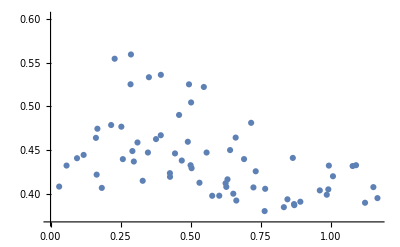

```mathematica
ListPlot[Map[{Max[movingSD[#[[2]],12]]-Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata]]
```

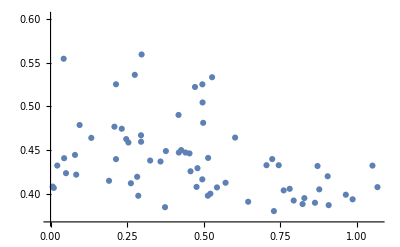

```mathematica
ListPlot[Map[{Max[movingSD[#[[2]],20]]-Min[movingSD[#[[2]],20]],Mean[#[[1]]]}&,widthandlocdata]]
```

```mathematica
Re
```

```mathematica
ListPlot[Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]]}&,widthandlocdata]]
```

-Graphics-

```mathematica
ListPlot[Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]]}&,widthandlocdataandtail]]
```

-Graphics-

```mathematica
Length[Select[widthandlocdataandtail[[1]][[3]],#==="True"&]]
```

0

```mathematica
widthandlocdataandtail[[1]][[3]][[1]]
```

False

```mathematica
ListPlot[Style[#[[;;2]],ColorData["Rainbow"][



Length[Select[#[[3]],#==="True"&]]





]]&/@data2,AspectRatio->1,Frame->True]
```

```mathematica
Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]]}&,widthandlocdataandtail]
```

```mathematica
Style[#[[;;2]],ColorData["Rainbow"][



Length[Select[#[[3]],#==="True"&]]





]]&/@data2
```

```mathematica
Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail]
```

{{0.521485,0.412362,0},{0.240402,0.423875,0},{0.176984,0.422213,0},{0.398036,0.415186,0},{0.119698,0.408577,0},{0.130542,0.432575,0},{0.109032,0.444716,3},{0.1134,0.440956,0},{0.224392,0.554488,0},{0.167488,0.407086,0},{0.594315,0.387388,1},{0.395024,0.406042,1},{0.244155,0.449108,1},{0.337723,0.419732,3},{0.467198,0.398156,0},{0.663373,0.385067,0},{0.540572,0.400442,1},{0.361845,0.408219,4},{0.205989,0.43991,0},{0.232937,0.559345,3},{0.427492,0.388622,0},{0.461039,0.394056,0},{0.249606,0.536106,5},{0.523058,0.459737,3},{0.635055,0.450232,0},{0.473752,0.447431,2},{0.693856,0.404227,0},{0.621041,0.446431,2},{0.200893,0.476922,1},{0.426267,0.462769,0},{0.753562,0.412961,1},{0.441536,0.490327,5},{0.216279,0.687986,15},{0.149996,0.474592,0},{0.613644,0.432518,0},{0.249172,0.53337,1},{0.378517,0.439958,0},{0.448261,0.525268,4},{0.262679,0.504579,1},{0.431119,0.429576,0},{0.68832,0.432052,0},{0.141901,0.464171,3},{0.402114,0.41684,0},{0.800642,0.420366,0},{0.459719,0.52225,5},{0.565909,0.391292,0},{0.362923,0.438296,2},{0.808855,0.426037,0},{0.246811,0.525325,6},{0.323134,0.467141,0},{0.737818,0.441295,2},{0.580936,0.398082,0},{0.444964,0.407613,0},{1.00642,0.390131,0},{0.524129,0.405397,0},{0.738279,0.399287,0},{0.538073,0.380618,0},{0.271493,0.629371,10},{0.489408,0.464497,0},{0.914771,0.432985,0},{0.210761,0.447451,3},{0.228985,0.799376,40},{0.314588,0.432962,1},{0.417891,0.392648,0},{0.197384,0.437198,0},{0.311565,0.458921,2},{0.833258,0.407956,0},{0.756898,0.395418,0},{0.166106,0.478827,4},{0.696195,0.481352,9}}

```mathematica
Transpose[Transpose[Select[Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]>1&]][[{1,2}]]]
```

{{0.109032,0.444716},{0.337723,0.419732},{0.361845,0.408219},{0.232937,0.559345},{0.249606,0.536106},{0.523058,0.459737},{0.473752,0.447431},{0.621041,0.446431},{0.441536,0.490327},{0.216279,0.687986},{0.448261,0.525268},{0.141901,0.464171},{0.459719,0.52225},{0.362923,0.438296},{0.246811,0.525325},{0.737818,0.441295},{0.271493,0.629371},{0.210761,0.447451},{0.228985,0.799376},{0.311565,0.458921},{0.166106,0.478827},{0.696195,0.481352}}

```mathematica
Transpose[Transpose[Select[Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]<=1&]][[{1,2}]]]
```

{{0.521485,0.412362},{0.240402,0.423875},{0.176984,0.422213},{0.398036,0.415186},{0.119698,0.408577},{0.130542,0.432575},{0.1134,0.440956},{0.224392,0.554488},{0.167488,0.407086},{0.594315,0.387388},{0.395024,0.406042},{0.244155,0.449108},{0.467198,0.398156},{0.663373,0.385067},{0.540572,0.400442},{0.205989,0.43991},{0.427492,0.388622},{0.461039,0.394056},{0.635055,0.450232},{0.693856,0.404227},{0.200893,0.476922},{0.426267,0.462769},{0.753562,0.412961},{0.149996,0.474592},{0.613644,0.432518},{0.249172,0.53337},{0.378517,0.439958},{0.262679,0.504579},{0.431119,0.429576},{0.68832,0.432052},{0.402114,0.41684},{0.800642,0.420366},{0.565909,0.391292},{0.808855,0.426037},{0.323134,0.467141},{0.580936,0.398082},{0.444964,0.407613},{1.00642,0.390131},{0.524129,0.405397},{0.738279,0.399287},{0.538073,0.380618},{0.489408,0.464497},{0.914771,0.432985},{0.314588,0.432962},{0.417891,0.392648},{0.197384,0.437198},{0.833258,0.407956},{0.756898,0.395418}}

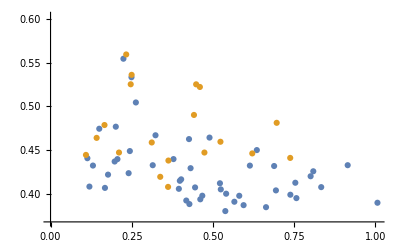

```mathematica
ListPlot[{Transpose[Transpose[Select[Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]<=1&]][[{1,2}]]],Transpose[Transpose[Select[Map[{Max[movingSD[#[[2]],4]]-Min[movingSD[#[[2]],4]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]>1&]][[{1,2}]]]}]
```

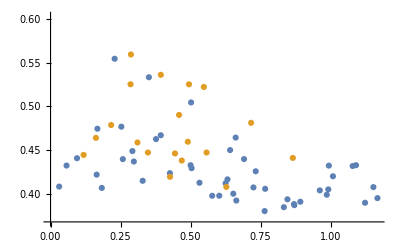

```mathematica
ListPlot[{Transpose[Transpose[Select[Map[{Max[movingSD[#[[2]],12]]-Min[movingSD[#[[2]],12]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]<=1&]][[{1,2}]]],Transpose[Transpose[Select[Map[{Max[movingSD[#[[2]],12]]-Min[movingSD[#[[2]],12]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]>1&]][[{1,2}]]]}]
```

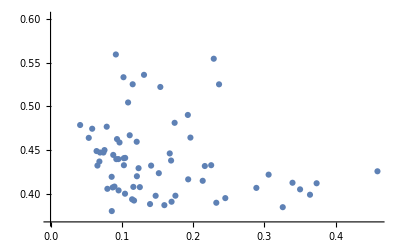

```mathematica
ListPlot[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata]]
```

```mathematica
ListPlot[Map[{Min[movingSD[#[[2]],4]],Mean[#[[1]]]}&,widthandlocdata]]
```

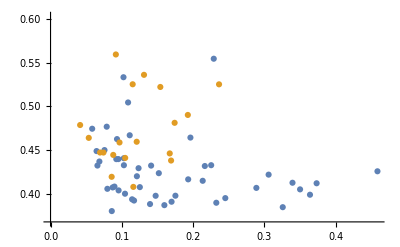

```mathematica
ListPlot[{Transpose[Transpose[Select[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]<=1&]][[{1,2}]]],Transpose[Transpose[Select[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]],Length[Select[#[[3]],#==="True"&]]}&,widthandlocdataandtail],#[[3]]>1&]][[{1,2}]]]}]
```

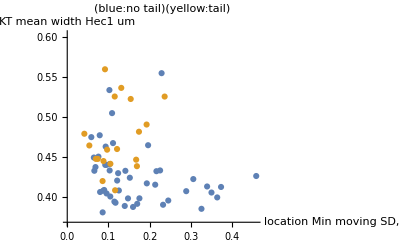

```mathematica
Show[%199,AxesLabel->{RawBoxes[RowBox[{RowBox[{"location"," ","Min"," ","moving"," ","SD"}],","," ",RowBox[{"window"," ","3"," ","min"," ",RowBox[{"(","um",")"}]}]}]],HoldForm[KT mean width Hec1 um]},PlotLabel->HoldForm[(blue:no tail)[yellow:tail]],LabelStyle->{GrayLevel[0]}]
```

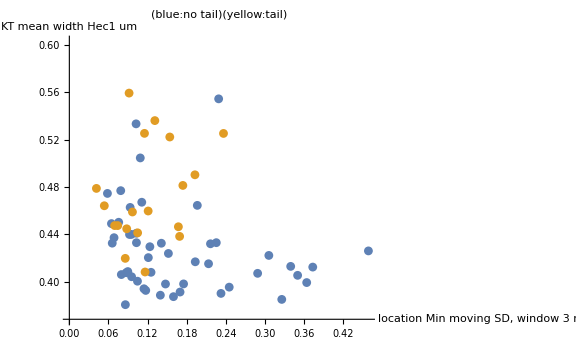

```mathematica
Show[%219,ImageSize->Large]
```

```mathematica
LinearModelFit[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata],x,x]
```

FittedModel[0.485778-0.229722 x]

```mathematica
FittedModel[0.4857778451355421-0.22972178474462107 x]["RSquared"]
```

0.0854175

```mathematica
x=Transpose[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata]][[1]];
y=Transpose[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata]][[2]];

(*Calculate Pearson correlation coefficient*)
r=Correlation[x,y]
```

-0.284112

```mathematica
(*Perform hypothesis test for negative correlation*)
test=HypothesisTestData[x,y,"PearsonCorrelation"]
```

```mathematica
PearsonCorrelationTest[x,y,"TestDataTable"]
```

PearsonCorrelationTest::nortst: At least one of the p-values in {1.46848×10^-8,0}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | -0.292263 | 0.0140854

```mathematica
PearsonCorrelationTest[x,y]
```

PearsonCorrelationTest::nortst: At least one of the p-values in {1.46848×10^-8,0}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

0.0140854

```mathematica
pValue=test["TestConclusion","TestSignificanceLevel"->0.05,"Tail"->"Left"];
```

Join::heads: Heads List and Statistics`HypothesisTestingUtilitiesDump`$TestSpecificProperties at positions 1 and 4 are expected to be the same.

Complement::heads: Heads Join and List at positions 2 and 1 are expected to be the same.

Message::name: Message name MessageName[{0.373263,0.151899,0.305928,0.213462,0.0896822,«20»,0.0879635,0.102823,0.228972,0.28874,«60»},invprp] is not of the form symbol::name or symbol::name::language.

Join::heads: Heads List and Statistics`HypothesisTestingUtilitiesDump`$TestSpecificProperties at positions 1 and 4 are expected to be the same.

Complement::heads: Heads Join and List at positions 2 and 1 are expected to be the same.

Message::name: Message name MessageName[{0.373263,0.151899,0.305928,0.213462,0.0896822,«20»,0.0879635,0.102823,0.228972,0.28874,«60»},invprp] is not of the form symbol::name or symbol::name::language.

```mathematica
tStatistic=test["TestStatistic"];
```

```mathematica
spearmanRho=SpearmanRho[x,y]

(*Perform a hypothesis test for Spearman's rank correlation*)
spearmanTest=HypothesisTestData[x,y,"SpearmanRankCorrelation"];
```

-0.371429

```mathematica
Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata]
```

```mathematica
Drop[Map[{Transpose[#][[10]],Transpose[#][[16]]}&,gathedata],1]
```

```mathematica
Table[Join[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata][[i]],Transpose[Flatten[Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1][[i]],1]][[1]]],{i,Length[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata]]}]
```

{{0.373263,0.412362,1,2,3,1},{0.151899,0.423875,1,2,3,2},{0.305928,0.422213,1,2,5,1},{0.213462,0.415186,1,2,5,2},{0.0896822,0.408577,1,2,7,1},{0.0657924,0.432575,1,2,7,2},{0.0879635,0.444716,1,2,9,1},{0.102823,0.440956,1,2,9,2},{0.228972,0.554488,1,2,11,1},{0.28874,0.407086,1,2,11,2},{0.159697,0.387388,1,3,3,1},{0.0797326,0.406042,1,3,3,2},{0.0645744,0.449108,1,3,5,1},{0.0857484,0.419732,1,3,5,2},{0.175176,0.398156,1,3,7,1},{0.32575,0.385067,1,3,7,2},{0.104465,0.400442,1,3,9,1},{0.11616,0.408219,1,3,9,2},{0.0922793,0.43991,1,3,11,1},{0.0916162,0.559345,1,3,11,2},{0.139573,0.388622,1,3,13,1},{0.114428,0.394056,1,3,13,2},{0.13111,0.536106,1,4,3,1},{0.12087,0.459737,1,4,3,2},{0.0756909,0.450232,1,4,5,1},{0.0742062,0.447431,1,4,5,2},{0.095466,0.404227,1,4,7,1},{0.167214,0.446431,1,4,7,2},{0.0788047,0.476922,1,4,9,1},{0.0932455,0.462769,1,4,9,2},{0.339433,0.412961,1,4,11,1},{0.192606,0.490327,1,4,11,2},{0.0480047,0.687986,1,5,3,1},{0.058421,0.474592,1,5,3,2},{0.141094,0.432518,1,5,5,1},{0.102334,0.53337,1,5,5,2},{0.0951698,0.439958,1,5,7,1},{0.236389,0.525268,1,5,7,2},{0.10878,0.504579,1,5,9,1},{0.123481,0.429576,1,5,9,2},{0.216437,0.432052,1,6,3,1},{0.053619,0.464171,1,6,3,2},{0.193096,0.41684,1,6,5,1},{0.121139,0.420366,1,6,5,2},{0.154025,0.52225,1,6,7,1},{0.169773,0.391292,1,6,7,2},{0.169109,0.438296,1,6,9,1},{0.458622,0.426037,1,6,9,2},{0.115226,0.525325,1,7,3,1},{0.111066,0.467141,1,7,3,2},{0.104713,0.441295,1,7,5,1},{0.147435,0.398082,1,7,5,2},{0.0871639,0.407613,1,7,7,1},{0.23254,0.390131,1,7,7,2},{0.350057,0.405397,1,8,3,1},{0.363973,0.399287,1,8,3,2},{0.0859281,0.380618,1,8,5,1},{0.0763304,0.629371,1,8,5,2},{0.196233,0.464497,1,8,9,1},{0.225353,0.432985,1,8,9,2},{0.0694616,0.447451,1,9,2,1},{0.0615932,0.799376,1,9,2,2},{0.102916,0.432962,1,9,5,1},{0.117156,0.392648,1,9,5,2},{0.0685435,0.437198,1,9,7,1},{0.0967624,0.458921,1,9,7,2},{0.125271,0.407956,1,9,9,1},{0.245168,0.395418,1,9,9,2},{0.0415116,0.478827,1,9,11,1},{0.174074,0.481352,1,9,11,2}}

```mathematica
Export["3minMovingSD.csv",Table[Join[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata][[i]],Transpose[Flatten[Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1][[i]],1]][[1]]],{i,Length[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata]]}]]
```

3minMovingSD.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["3minMovingSD.csv"]]]
```

```mathematica
Map[{Transpose[#][[Range[5]]]}&,gathedata][[1]]
```

{{{condition},{Cell index},{KT pairs},{KT},{Time}}}

```mathematica
Map[{Transpose[#][[Range[18]]]}&,gathedata][[1]]
```

{{{condition},{Cell index},{KT pairs},{KT},{Time},{move X},{move Y},{move Z},{move interval},{WidthX Ch1},{tail or not ch1},{tail direction ch1},{WidthX Ch2},{tail or not ch2},{tail direction ch2},{location X},{location Y},{location Z}}}

```mathematica
Join[Map[{Min[movingSD[#[[2]],12]],Mean[#[[1]]]}&,widthandlocdata][[1]],Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1][[1]]]
```

{0.373263,0.412362,{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1]
```

{{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}},68,{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9},{11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}
 |  |  |  |

```mathematica
Transpose[Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1][[2]]][[1]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1][[2]]
```

{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}

```mathematica
Flatten[Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1][[2]],1]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2},{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}

```mathematica
Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata]
```

{{{{condition},{Cell index},{KT pairs},{KT}}},69,{{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,5,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9},1,{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}}
 |  |  |  |

```mathematica
Transpose[Drop[Map[{Transpose[#][[{1,2,3,4}]]}&,gathedata],1][[2]]][[1]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}